InterpolatingFunction::dmval: Input value {2800} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{14.1978,140},{7.25557,160},{6.81277,180},{6.47771,200},{7.56937,220},{16.4677,240},{6.01221,260},{5.91275,280},{5.82746,300},{5.753,320},{5.68656,340},{5.62662,360},{5.57181,380},{5.52115,400},{5.47348,420},{5.42827,440},{5.3847,460},{5.34199,480},{5.29949,500},{5.25612,520},{5.21068,540},{5.16171,560},{5.10639,580},{4.23352,600}}

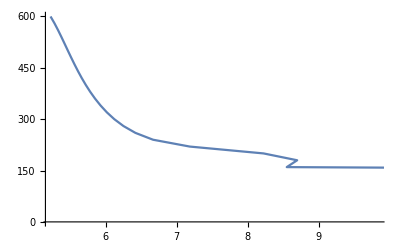

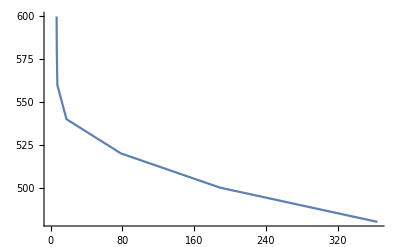

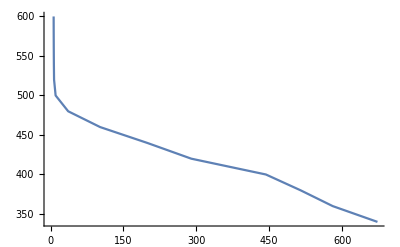

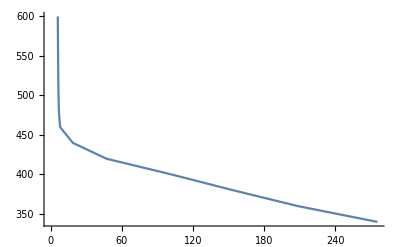

```mathematica
TPHS={{{0.05,0.,2501.5,26.618},{0.05,0.00061343,2501.,9.1544},{0.05,0.00061343,0.16941,0.00061788},{0.05,0.5,0.67788,0.00065099},{0.05,1.,1.1866,0.00068316},{0.05,1.5,1.6949,0.00071437},{0.05,2.,2.2028,0.00074463},{0.05,2.5,2.7104,0.00077393},{0.05,3.,3.2175,0.00080228},{0.05,3.5,3.7243,0.00082968},{0.05,4.,4.2307,0.00085614},{0.05,4.5,4.7367,0.00088165},{0.05,5.,5.2423,0.00090623},{0.05,5.5,5.7475,0.00092988},{0.05,6.,6.2524,0.00095259},{0.05,6.5,6.7569,0.00097439},{0.05,7.,7.261,0.00099525},{0.05,7.5,7.7647,0.0010152},{0.05,8.,8.268,0.0010342},{0.05,8.5,8.771,0.0010524},{0.05,9.,9.2736,0.0010696},{0.05,9.5,9.7759,0.0010859},{0.05,10.,10.278,0.0011013},{0.05,10.5,10.779,0.0011158},{0.05,11.,11.28,0.0011294},{0.05,11.5,11.781,0.0011422},{0.05,12.,12.282,0.001154},{0.05,12.5,12.782,0.0011649},{0.05,13.,13.281,0.001175},{0.05,13.5,13.781,0.0011842},{0.05,14.,14.28,0.0011925},{0.05,14.5,14.778,0.0012},{0.05,15.,15.276,0.0012066},{0.05,15.5,15.774,0.0012123},{0.05,16.,16.272,0.0012172},{0.05,16.5,16.769,0.0012212},{0.05,17.,17.266,0.0012243},{0.05,17.5,17.762,0.0012267},{0.05,18.,18.258,0.0012281},{0.05,18.5,18.754,0.0012287},{0.05,19.,19.25,0.0012285},{0.05,19.5,19.745,0.0012274},{0.05,20.,20.239,0.0012256},{0.05,20.5,20.734,0.0012228},{0.05,21.,21.228,0.0012193},{0.05,21.5,21.721,0.0012149},{0.05,22.,22.215,0.0012097},{0.05,22.5,22.708,0.0012037},{0.05,23.,23.2,0.0011969},{0.05,23.5,23.693,0.0011892},{0.05,24.,24.185,0.0011808},{0.05,24.5,24.676,0.0011716},{0.05,25.,25.168,0.0011615},{0.05,25.5,25.659,0.0011507},{0.05,26.,26.149,0.001139},{0.05,26.5,26.64,0.0011266},{0.05,27.,27.13,0.0011134},{0.05,27.5,27.619,0.0010994},{0.05,28.,28.109,0.0010846},{0.05,28.5,28.598,0.001069},{0.05,29.,29.086,0.0010527},{0.05,29.5,29.575,0.0010356},{0.05,30.,30.063,0.0010177},{0.05,30.5,30.55,0.00099904},{0.05,31.,31.038,0.00097963},{0.05,31.5,31.525,0.00095945},{0.05,32.,32.011,0.00093852},{0.05,32.5,32.498,0.00091684},{0.05,33.,32.984,0.0008944},{0.05,33.5,33.47,0.00087121},{0.05,34.,33.955,0.00084728},{0.05,34.5,34.44,0.00082261},{0.05,35.,34.925,0.0007972},{0.05,35.5,35.409,0.00077105},{0.05,36.,35.894,0.00074416},{0.05,36.5,36.378,0.00071655},{0.05,37.,36.861,0.00068821},{0.05,37.5,37.344,0.00065914},{0.05,38.,37.827,0.00062935},{0.05,38.5,38.31,0.00059885},{0.05,39.,38.792,0.00056762},{0.05,39.5,39.274,0.00053569},{0.05,40.,39.756,0.00050304},{0.05,40.5,40.237,0.00046969},{0.05,41.,40.718,0.00043563},{0.05,41.5,41.199,0.00040087},{0.05,42.,41.68,0.00036541},{0.05,42.5,42.16,0.00032925},{0.05,43.,42.64,0.00029241},{0.05,43.5,43.119,0.00025487},{0.05,44.,43.599,0.00021664},{0.05,44.5,44.078,0.00017773},{0.05,45.,44.556,0.00013814},{0.05,45.5,45.035,0.000097867},{0.05,46.,45.513,0.000056919},{0.05,46.5,45.991,0.000015297},{0.05,47.,46.468,-0.000026995},{0.05,47.5,46.945,-0.000069956},{0.05,48.,47.422,-0.00011358},{0.05,48.5,47.899,-0.00015787},{0.05,49.,48.375,-0.00020282},{0.05,49.5,48.851,-0.00024843},{0.05,50.,49.327,-0.00029469},{0.05,50.5,49.803,-0.0003416},{0.05,51.,50.278,-0.00038916},{0.05,51.5,50.753,-0.00043737},{0.05,52.,51.227,-0.00048622},{0.05,52.5,51.702,-0.00053572},{0.05,53.,52.176,-0.00058585},{0.05,53.5,52.65,-0.00063662},{0.05,54.,53.123,-0.00068802},{0.05,54.5,53.597,-0.00074005},{0.05,55.,54.069,-0.00079271},{0.05,55.5,54.542,-0.00084599},{0.05,56.,55.015,-0.0008999},{0.05,56.5,55.487,-0.00095443},{0.05,57.,55.959,-0.0010096},{0.05,57.5,56.43,-0.0010653},{0.05,58.,56.901,-0.0011217},{0.05,58.5,57.372,-0.0011787},{0.05,59.,57.843,-0.0012363},{0.05,59.5,58.314,-0.0012945},{0.05,60.,58.784,-0.0013533},{0.05,60.5,59.254,-0.0014127},{0.05,61.,59.724,-0.0014727},{0.05,61.5,60.193,-0.0015333},{0.05,62.,60.662,-0.0015945},{0.05,62.5,61.131,-0.0016562},{0.05,63.,61.6,-0.0017186},{0.05,63.5,62.068,-0.0017815},{0.05,64.,62.536,-0.0018451},{0.05,64.5,63.004,-0.0019092},{0.05,65.,63.472,-0.0019739},{0.05,65.5,63.939,-0.0020391},{0.05,66.,64.406,-0.002105},{0.05,66.5,64.873,-0.0021714},{0.05,67.,65.339,-0.0022383},{0.05,67.5,65.806,-0.0023059},{0.05,68.,66.272,-0.002374},{0.05,68.5,66.737,-0.0024426},{0.05,69.,67.203,-0.0025118},{0.05,69.5,67.668,-0.0025816},{0.05,70.,68.133,-0.002652},{0.05,70.5,68.598,-0.0027228},{0.05,71.,69.063,-0.0027943},{0.05,71.5,69.527,-0.0028662},{0.05,72.,69.991,-0.0029388},{0.05,72.5,70.455,-0.0030118},{0.05,73.,70.918,-0.0030854},{0.05,73.5,71.381,-0.0031596},{0.05,74.,71.844,-0.0032342},{0.05,74.5,72.307,-0.0033094},{0.05,75.,72.77,-0.0033852},{0.05,75.5,73.232,-0.0034614},{0.05,76.,73.694,-0.0035382},{0.05,76.5,74.156,-0.0036155},{0.05,77.,74.617,-0.0036934},{0.05,77.5,75.079,-0.0037717},{0.05,78.,75.54,-0.0038506},{0.05,78.5,76.001,-0.00393},{0.05,79.,76.461,-0.0040099},{0.05,79.5,76.921,-0.0040903},{0.05,80.,77.382,-0.0041712},{0.05,80.5,77.841,-0.0042526},{0.05,81.,78.301,-0.0043346},{0.05,81.5,78.761,-0.004417},{0.05,82.,79.22,-0.0044999},{0.05,82.5,79.679,-0.0045833},{0.05,83.,80.137,-0.0046673},{0.05,83.5,80.596,-0.0047517},{0.05,84.,81.054,-0.0048366},{0.05,84.5,81.512,-0.004922},{0.05,85.,81.97,-0.0050078},{0.05,85.5,82.427,-0.0050942},{0.05,86.,82.885,-0.005181},{0.05,86.5,83.342,-0.0052683},{0.05,87.,83.799,-0.0053561},{0.05,87.5,84.255,-0.0054444},{0.05,88.,84.712,-0.0055332},{0.05,88.5,85.168,-0.0056224},{0.05,89.,85.624,-0.0057121},{0.05,89.5,86.08,-0.0058022},{0.05,90.,86.535,-0.0058929},{0.05,90.5,86.99,-0.0059839},{0.05,91.,87.446,-0.0060755},{0.05,91.5,87.9,-0.0061675},{0.05,92.,88.355,-0.0062599},{0.05,92.5,88.809,-0.0063529},{0.05,93.,89.264,-0.0064462},{0.05,93.5,89.718,-0.0065401},{0.05,94.,90.171,-0.0066343},{0.05,94.5,90.625,-0.006729},{0.05,95.,91.078,-0.0068242},{0.05,95.5,91.531,-0.0069198},{0.05,96.,91.984,-0.0070159},{0.05,96.5,92.437,-0.0071123},{0.05,97.,92.889,-0.0072093},{0.05,97.5,93.342,-0.0073066},{0.05,98.,93.794,-0.0074044},{0.05,98.5,94.246,-0.0075026},{0.05,99.,94.697,-0.0076013},{0.05,99.5,95.149,-0.0077004},{0.05,100.,95.6,-0.0077999}},{{20.,0.,2538.7,26.716},{20.,0.0023393,2537.4,8.666},{20.,0.0023393,83.914,0.29648},{20.,0.5,84.382,0.29638},{20.,1.,84.853,0.29628},{20.,1.5,85.323,0.29617},{20.,2.,85.793,0.29607},{20.,2.5,86.262,0.29596},{20.,3.,86.732,0.29586},{20.,3.5,87.201,0.29575},{20.,4.,87.67,0.29564},{20.,4.5,88.138,0.29554},{20.,5.,88.607,0.29543},{20.,5.5,89.075,0.29532},{20.,6.,89.543,0.29522},{20.,6.5,90.011,0.29511},{20.,7.,90.479,0.295},{20.,7.5,90.946,0.29489},{20.,8.,91.414,0.29478},{20.,8.5,91.881,0.29467},{20.,9.,92.348,0.29457},{20.,9.5,92.814,0.29446},{20.,10.,93.281,0.29435},{20.,10.5,93.747,0.29423},{20.,11.,94.213,0.29412},{20.,11.5,94.679,0.29401},{20.,12.,95.144,0.2939},{20.,12.5,95.61,0.29379},{20.,13.,96.075,0.29368},{20.,13.5,96.54,0.29357},{20.,14.,97.005,0.29345},{20.,14.5,97.469,0.29334},{20.,15.,97.934,0.29323},{20.,15.5,98.398,0.29311},{20.,16.,98.862,0.293},{20.,16.5,99.326,0.29288},{20.,17.,99.789,0.29277},{20.,17.5,100.25,0.29265},{20.,18.,100.72,0.29254},{20.,18.5,101.18,0.29242},{20.,19.,101.64,0.29231},{20.,19.5,102.1,0.29219},{20.,20.,102.57,0.29207},{20.,20.5,103.03,0.29196},{20.,21.,103.49,0.29184},{20.,21.5,103.95,0.29172},{20.,22.,104.41,0.29161},{20.,22.5,104.87,0.29149},{20.,23.,105.34,0.29137},{20.,23.5,105.8,0.29125},{20.,24.,106.26,0.29113},{20.,24.5,106.72,0.29101},{20.,25.,107.18,0.29089},{20.,25.5,107.64,0.29077},{20.,26.,108.1,0.29065},{20.,26.5,108.56,0.29053},{20.,27.,109.02,0.29041},{20.,27.5,109.48,0.29029},{20.,28.,109.94,0.29017},{20.,28.5,110.4,0.29005},{20.,29.,110.85,0.28992},{20.,29.5,111.31,0.2898},{20.,30.,111.77,0.28968},{20.,30.5,112.23,0.28956},{20.,31.,112.69,0.28943},{20.,31.5,113.15,0.28931},{20.,32.,113.6,0.28918},{20.,32.5,114.06,0.28906},{20.,33.,114.52,0.28894},{20.,33.5,114.97,0.28881},{20.,34.,115.43,0.28869},{20.,34.5,115.89,0.28856},{20.,35.,116.34,0.28844},{20.,35.5,116.8,0.28831},{20.,36.,117.26,0.28818},{20.,36.5,117.71,0.28806},{20.,37.,118.17,0.28793},{20.,37.5,118.62,0.2878},{20.,38.,119.08,0.28768},{20.,38.5,119.54,0.28755},{20.,39.,119.99,0.28742},{20.,39.5,120.45,0.28729},{20.,40.,120.9,0.28716},{20.,40.5,121.35,0.28703},{20.,41.,121.81,0.28691},{20.,41.5,122.26,0.28678},{20.,42.,122.72,0.28665},{20.,42.5,123.17,0.28652},{20.,43.,123.62,0.28639},{20.,43.5,124.08,0.28626},{20.,44.,124.53,0.28613},{20.,44.5,124.98,0.28599},{20.,45.,125.44,0.28586},{20.,45.5,125.89,0.28573},{20.,46.,126.34,0.2856},{20.,46.5,126.79,0.28547},{20.,47.,127.25,0.28534},{20.,47.5,127.7,0.2852},{20.,48.,128.15,0.28507},{20.,48.5,128.6,0.28494},{20.,49.,129.05,0.2848},{20.,49.5,129.5,0.28467},{20.,50.,129.95,0.28454},{20.,50.5,130.4,0.2844},{20.,51.,130.86,0.28427},{20.,51.5,131.31,0.28413},{20.,52.,131.76,0.284},{20.,52.5,132.21,0.28386},{20.,53.,132.66,0.28373},{20.,53.5,133.11,0.28359},{20.,54.,133.56,0.28345},{20.,54.5,134.01,0.28332},{20.,55.,134.45,0.28318},{20.,55.5,134.9,0.28304},{20.,56.,135.35,0.28291},{20.,56.5,135.8,0.28277},{20.,57.,136.25,0.28263},{20.,57.5,136.7,0.28249},{20.,58.,137.15,0.28236},{20.,58.5,137.59,0.28222},{20.,59.,138.04,0.28208},{20.,59.5,138.49,0.28194},{20.,60.,138.94,0.2818},{20.,60.5,139.38,0.28166},{20.,61.,139.83,0.28152},{20.,61.5,140.28,0.28138},{20.,62.,140.73,0.28124},{20.,62.5,141.17,0.2811},{20.,63.,141.62,0.28096},{20.,63.5,142.07,0.28082},{20.,64.,142.51,0.28068},{20.,64.5,142.96,0.28054},{20.,65.,143.4,0.2804},{20.,65.5,143.85,0.28025},{20.,66.,144.29,0.28011},{20.,66.5,144.74,0.27997},{20.,67.,145.19,0.27983},{20.,67.5,145.63,0.27968},{20.,68.,146.07,0.27954},{20.,68.5,146.52,0.2794},{20.,69.,146.96,0.27925},{20.,69.5,147.41,0.27911},{20.,70.,147.85,0.27897},{20.,70.5,148.3,0.27882},{20.,71.,148.74,0.27868},{20.,71.5,149.18,0.27853},{20.,72.,149.63,0.27839},{20.,72.5,150.07,0.27824},{20.,73.,150.51,0.2781},{20.,73.5,150.96,0.27795},{20.,74.,151.4,0.27781},{20.,74.5,151.84,0.27766},{20.,75.,152.29,0.27751},{20.,75.5,152.73,0.27737},{20.,76.,153.17,0.27722},{20.,76.5,153.61,0.27707},{20.,77.,154.05,0.27693},{20.,77.5,154.5,0.27678},{20.,78.,154.94,0.27663},{20.,78.5,155.38,0.27648},{20.,79.,155.82,0.27633},{20.,79.5,156.26,0.27619},{20.,80.,156.7,0.27604},{20.,80.5,157.14,0.27589},{20.,81.,157.58,0.27574},{20.,81.5,158.02,0.27559},{20.,82.,158.47,0.27544},{20.,82.5,158.91,0.27529},{20.,83.,159.35,0.27514},{20.,83.5,159.79,0.27499},{20.,84.,160.23,0.27484},{20.,84.5,160.66,0.27469},{20.,85.,161.1,0.27454},{20.,85.5,161.54,0.27439},{20.,86.,161.98,0.27424},{20.,86.5,162.42,0.27409},{20.,87.,162.86,0.27394},{20.,87.5,163.3,0.27378},{20.,88.,163.74,0.27363},{20.,88.5,164.18,0.27348},{20.,89.,164.61,0.27333},{20.,89.5,165.05,0.27317},{20.,90.,165.49,0.27302},{20.,90.5,165.93,0.27287},{20.,91.,166.37,0.27272},{20.,91.5,166.8,0.27256},{20.,92.,167.24,0.27241},{20.,92.5,167.68,0.27225},{20.,93.,168.12,0.2721},{20.,93.5,168.55,0.27195},{20.,94.,168.99,0.27179},{20.,94.5,169.43,0.27164},{20.,95.,169.86,0.27148},{20.,95.5,170.3,0.27133},{20.,96.,170.73,0.27117},{20.,96.5,171.17,0.27102},{20.,97.,171.61,0.27086},{20.,97.5,172.04,0.27071},{20.,98.,172.48,0.27055},{20.,98.5,172.91,0.27039},{20.,99.,173.35,0.27024},{20.,99.5,173.78,0.27008},{20.,100.,174.22,0.26992}},{{40.,0.,2576.,26.809},{40.,0.0073849,2573.5,8.2555},{40.,0.0073849,167.53,0.5724},{40.,0.5,167.97,0.57221},{40.,1.,168.41,0.57202},{40.,1.5,168.86,0.57182},{40.,2.,169.3,0.57163},{40.,2.5,169.74,0.57143},{40.,3.,170.18,0.57124},{40.,3.5,170.63,0.57104},{40.,4.,171.07,0.57085},{40.,4.5,171.51,0.57066},{40.,5.,171.95,0.57046},{40.,5.5,172.39,0.57027},{40.,6.,172.84,0.57007},{40.,6.5,173.28,0.56988},{40.,7.,173.72,0.56968},{40.,7.5,174.16,0.56949},{40.,8.,174.6,0.56929},{40.,8.5,175.04,0.5691},{40.,9.,175.48,0.5689},{40.,9.5,175.92,0.56871},{40.,10.,176.36,0.56851},{40.,10.5,176.81,0.56832},{40.,11.,177.25,0.56812},{40.,11.5,177.69,0.56793},{40.,12.,178.13,0.56773},{40.,12.5,178.57,0.56754},{40.,13.,179.01,0.56734},{40.,13.5,179.45,0.56715},{40.,14.,179.89,0.56695},{40.,14.5,180.33,0.56676},{40.,15.,180.77,0.56656},{40.,15.5,181.21,0.56637},{40.,16.,181.65,0.56617},{40.,16.5,182.08,0.56598},{40.,17.,182.52,0.56578},{40.,17.5,182.96,0.56559},{40.,18.,183.4,0.56539},{40.,18.5,183.84,0.5652},{40.,19.,184.28,0.565},{40.,19.5,184.72,0.56481},{40.,20.,185.16,0.56461},{40.,20.5,185.59,0.56441},{40.,21.,186.03,0.56422},{40.,21.5,186.47,0.56402},{40.,22.,186.91,0.56383},{40.,22.5,187.35,0.56363},{40.,23.,187.78,0.56344},{40.,23.5,188.22,0.56324},{40.,24.,188.66,0.56304},{40.,24.5,189.1,0.56285},{40.,25.,189.53,0.56265},{40.,25.5,189.97,0.56246},{40.,26.,190.41,0.56226},{40.,26.5,190.85,0.56206},{40.,27.,191.28,0.56187},{40.,27.5,191.72,0.56167},{40.,28.,192.16,0.56148},{40.,28.5,192.59,0.56128},{40.,29.,193.03,0.56108},{40.,29.5,193.46,0.56089},{40.,30.,193.9,0.56069},{40.,30.5,194.34,0.5605},{40.,31.,194.77,0.5603},{40.,31.5,195.21,0.5601},{40.,32.,195.64,0.55991},{40.,32.5,196.08,0.55971},{40.,33.,196.51,0.55951},{40.,33.5,196.95,0.55932},{40.,34.,197.39,0.55912},{40.,34.5,197.82,0.55892},{40.,35.,198.26,0.55873},{40.,35.5,198.69,0.55853},{40.,36.,199.13,0.55833},{40.,36.5,199.56,0.55814},{40.,37.,199.99,0.55794},{40.,37.5,200.43,0.55774},{40.,38.,200.86,0.55755},{40.,38.5,201.3,0.55735},{40.,39.,201.73,0.55715},{40.,39.5,202.17,0.55696},{40.,40.,202.6,0.55676},{40.,40.5,203.03,0.55656},{40.,41.,203.47,0.55636},{40.,41.5,203.9,0.55617},{40.,42.,204.33,0.55597},{40.,42.5,204.77,0.55577},{40.,43.,205.2,0.55558},{40.,43.5,205.63,0.55538},{40.,44.,206.07,0.55518},{40.,44.5,206.5,0.55498},{40.,45.,206.93,0.55479},{40.,45.5,207.36,0.55459},{40.,46.,207.8,0.55439},{40.,46.5,208.23,0.55419},{40.,47.,208.66,0.554},{40.,47.5,209.09,0.5538},{40.,48.,209.53,0.5536},{40.,48.5,209.96,0.5534},{40.,49.,210.39,0.55321},{40.,49.5,210.82,0.55301},{40.,50.,211.25,0.55281},{40.,50.5,211.69,0.55261},{40.,51.,212.12,0.55241},{40.,51.5,212.55,0.55222},{40.,52.,212.98,0.55202},{40.,52.5,213.41,0.55182},{40.,53.,213.84,0.55162},{40.,53.5,214.27,0.55142},{40.,54.,214.7,0.55123},{40.,54.5,215.13,0.55103},{40.,55.,215.56,0.55083},{40.,55.5,216.,0.55063},{40.,56.,216.43,0.55043},{40.,56.5,216.86,0.55023},{40.,57.,217.29,0.55004},{40.,57.5,217.72,0.54984},{40.,58.,218.15,0.54964},{40.,58.5,218.58,0.54944},{40.,59.,219.01,0.54924},{40.,59.5,219.44,0.54904},{40.,60.,219.86,0.54885},{40.,60.5,220.29,0.54865},{40.,61.,220.72,0.54845},{40.,61.5,221.15,0.54825},{40.,62.,221.58,0.54805},{40.,62.5,222.01,0.54785},{40.,63.,222.44,0.54765},{40.,63.5,222.87,0.54745},{40.,64.,223.3,0.54726},{40.,64.5,223.73,0.54706},{40.,65.,224.15,0.54686},{40.,65.5,224.58,0.54666},{40.,66.,225.01,0.54646},{40.,66.5,225.44,0.54626},{40.,67.,225.87,0.54606},{40.,67.5,226.3,0.54586},{40.,68.,226.72,0.54566},{40.,68.5,227.15,0.54546},{40.,69.,227.58,0.54526},{40.,69.5,228.01,0.54506},{40.,70.,228.43,0.54487},{40.,70.5,228.86,0.54467},{40.,71.,229.29,0.54447},{40.,71.5,229.72,0.54427},{40.,72.,230.14,0.54407},{40.,72.5,230.57,0.54387},{40.,73.,231.,0.54367},{40.,73.5,231.42,0.54347},{40.,74.,231.85,0.54327},{40.,74.5,232.28,0.54307},{40.,75.,232.7,0.54287},{40.,75.5,233.13,0.54267},{40.,76.,233.55,0.54247},{40.,76.5,233.98,0.54227},{40.,77.,234.41,0.54207},{40.,77.5,234.83,0.54187},{40.,78.,235.26,0.54167},{40.,78.5,235.68,0.54147},{40.,79.,236.11,0.54127},{40.,79.5,236.54,0.54107},{40.,80.,236.96,0.54087},{40.,80.5,237.39,0.54067},{40.,81.,237.81,0.54047},{40.,81.5,238.24,0.54027},{40.,82.,238.66,0.54007},{40.,82.5,239.09,0.53987},{40.,83.,239.51,0.53967},{40.,83.5,239.94,0.53947},{40.,84.,240.36,0.53927},{40.,84.5,240.78,0.53907},{40.,85.,241.21,0.53887},{40.,85.5,241.63,0.53867},{40.,86.,242.06,0.53847},{40.,86.5,242.48,0.53827},{40.,87.,242.91,0.53807},{40.,87.5,243.33,0.53787},{40.,88.,243.75,0.53766},{40.,88.5,244.18,0.53746},{40.,89.,244.6,0.53726},{40.,89.5,245.02,0.53706},{40.,90.,245.45,0.53686},{40.,90.5,245.87,0.53666},{40.,91.,246.29,0.53646},{40.,91.5,246.72,0.53626},{40.,92.,247.14,0.53606},{40.,92.5,247.56,0.53586},{40.,93.,247.99,0.53566},{40.,93.5,248.41,0.53546},{40.,94.,248.83,0.53525},{40.,94.5,249.25,0.53505},{40.,95.,249.68,0.53485},{40.,95.5,250.1,0.53465},{40.,96.,250.52,0.53445},{40.,96.5,250.94,0.53425},{40.,97.,251.37,0.53405},{40.,97.5,251.79,0.53385},{40.,98.,252.21,0.53364},{40.,98.5,252.63,0.53344},{40.,99.,253.05,0.53324},{40.,99.5,253.47,0.53304},{40.,100.,253.9,0.53284}},{{60.,0.,2613.4,26.896},{60.,0.019946,2608.8,7.9081},{60.,0.019946,251.18,0.83129},{60.,0.5,251.58,0.83104},{60.,1.,252.,0.83077},{60.,1.5,252.42,0.83051},{60.,2.,252.84,0.83024},{60.,2.5,253.26,0.82998},{60.,3.,253.68,0.82971},{60.,3.5,254.1,0.82945},{60.,4.,254.52,0.82918},{60.,4.5,254.94,0.82892},{60.,5.,255.36,0.82865},{60.,5.5,255.78,0.82839},{60.,6.,256.2,0.82812},{60.,6.5,256.62,0.82786},{60.,7.,257.04,0.8276},{60.,7.5,257.46,0.82733},{60.,8.,257.88,0.82707},{60.,8.5,258.29,0.82681},{60.,9.,258.71,0.82654},{60.,9.5,259.13,0.82628},{60.,10.,259.55,0.82602},{60.,10.5,259.97,0.82575},{60.,11.,260.39,0.82549},{60.,11.5,260.81,0.82523},{60.,12.,261.23,0.82497},{60.,12.5,261.65,0.82471},{60.,13.,262.06,0.82444},{60.,13.5,262.48,0.82418},{60.,14.,262.9,0.82392},{60.,14.5,263.32,0.82366},{60.,15.,263.74,0.8234},{60.,15.5,264.16,0.82314},{60.,16.,264.57,0.82288},{60.,16.5,264.99,0.82262},{60.,17.,265.41,0.82236},{60.,17.5,265.83,0.8221},{60.,18.,266.25,0.82184},{60.,18.5,266.66,0.82158},{60.,19.,267.08,0.82132},{60.,19.5,267.5,0.82106},{60.,20.,267.92,0.8208},{60.,20.5,268.34,0.82054},{60.,21.,268.75,0.82028},{60.,21.5,269.17,0.82002},{60.,22.,269.59,0.81976},{60.,22.5,270.01,0.8195},{60.,23.,270.42,0.81925},{60.,23.5,270.84,0.81899},{60.,24.,271.26,0.81873},{60.,24.5,271.68,0.81847},{60.,25.,272.09,0.81821},{60.,25.5,272.51,0.81795},{60.,26.,272.93,0.8177},{60.,26.5,273.34,0.81744},{60.,27.,273.76,0.81718},{60.,27.5,274.18,0.81693},{60.,28.,274.6,0.81667},{60.,28.5,275.01,0.81641},{60.,29.,275.43,0.81615},{60.,29.5,275.85,0.8159},{60.,30.,276.26,0.81564},{60.,30.5,276.68,0.81539},{60.,31.,277.1,0.81513},{60.,31.5,277.51,0.81487},{60.,32.,277.93,0.81462},{60.,32.5,278.35,0.81436},{60.,33.,278.76,0.81411},{60.,33.5,279.18,0.81385},{60.,34.,279.59,0.81359},{60.,34.5,280.01,0.81334},{60.,35.,280.43,0.81308},{60.,35.5,280.84,0.81283},{60.,36.,281.26,0.81257},{60.,36.5,281.67,0.81232},{60.,37.,282.09,0.81207},{60.,37.5,282.51,0.81181},{60.,38.,282.92,0.81156},{60.,38.5,283.34,0.8113},{60.,39.,283.75,0.81105},{60.,39.5,284.17,0.81079},{60.,40.,284.58,0.81054},{60.,40.5,285.,0.81029},{60.,41.,285.42,0.81003},{60.,41.5,285.83,0.80978},{60.,42.,286.25,0.80953},{60.,42.5,286.66,0.80927},{60.,43.,287.08,0.80902},{60.,43.5,287.49,0.80877},{60.,44.,287.91,0.80851},{60.,44.5,288.32,0.80826},{60.,45.,288.74,0.80801},{60.,45.5,289.15,0.80776},{60.,46.,289.57,0.80751},{60.,46.5,289.98,0.80725},{60.,47.,290.4,0.807},{60.,47.5,290.81,0.80675},{60.,48.,291.23,0.8065},{60.,48.5,291.64,0.80625},{60.,49.,292.05,0.80599},{60.,49.5,292.47,0.80574},{60.,50.,292.88,0.80549},{60.,50.5,293.3,0.80524},{60.,51.,293.71,0.80499},{60.,51.5,294.13,0.80474},{60.,52.,294.54,0.80449},{60.,52.5,294.95,0.80424},{60.,53.,295.37,0.80399},{60.,53.5,295.78,0.80374},{60.,54.,296.2,0.80349},{60.,54.5,296.61,0.80323},{60.,55.,297.02,0.80298},{60.,55.5,297.44,0.80273},{60.,56.,297.85,0.80248},{60.,56.5,298.27,0.80223},{60.,57.,298.68,0.80199},{60.,57.5,299.09,0.80174},{60.,58.,299.51,0.80149},{60.,58.5,299.92,0.80124},{60.,59.,300.33,0.80099},{60.,59.5,300.75,0.80074},{60.,60.,301.16,0.80049},{60.,60.5,301.57,0.80024},{60.,61.,301.99,0.79999},{60.,61.5,302.4,0.79974},{60.,62.,302.81,0.79949},{60.,62.5,303.22,0.79925},{60.,63.,303.64,0.799},{60.,63.5,304.05,0.79875},{60.,64.,304.46,0.7985},{60.,64.5,304.88,0.79825},{60.,65.,305.29,0.79801},{60.,65.5,305.7,0.79776},{60.,66.,306.11,0.79751},{60.,66.5,306.53,0.79726},{60.,67.,306.94,0.79701},{60.,67.5,307.35,0.79677},{60.,68.,307.76,0.79652},{60.,68.5,308.18,0.79627},{60.,69.,308.59,0.79603},{60.,69.5,309.,0.79578},{60.,70.,309.41,0.79553},{60.,70.5,309.82,0.79528},{60.,71.,310.24,0.79504},{60.,71.5,310.65,0.79479},{60.,72.,311.06,0.79455},{60.,72.5,311.47,0.7943},{60.,73.,311.88,0.79405},{60.,73.5,312.29,0.79381},{60.,74.,312.71,0.79356},{60.,74.5,313.12,0.79331},{60.,75.,313.53,0.79307},{60.,75.5,313.94,0.79282},{60.,76.,314.35,0.79258},{60.,76.5,314.76,0.79233},{60.,77.,315.18,0.79209},{60.,77.5,315.59,0.79184},{60.,78.,316.,0.79159},{60.,78.5,316.41,0.79135},{60.,79.,316.82,0.7911},{60.,79.5,317.23,0.79086},{60.,80.,317.64,0.79061},{60.,80.5,318.05,0.79037},{60.,81.,318.46,0.79013},{60.,81.5,318.87,0.78988},{60.,82.,319.28,0.78964},{60.,82.5,319.7,0.78939},{60.,83.,320.11,0.78915},{60.,83.5,320.52,0.7889},{60.,84.,320.93,0.78866},{60.,84.5,321.34,0.78841},{60.,85.,321.75,0.78817},{60.,85.5,322.16,0.78793},{60.,86.,322.57,0.78768},{60.,86.5,322.98,0.78744},{60.,87.,323.39,0.7872},{60.,87.5,323.8,0.78695},{60.,88.,324.21,0.78671},{60.,88.5,324.62,0.78647},{60.,89.,325.03,0.78622},{60.,89.5,325.44,0.78598},{60.,90.,325.85,0.78574},{60.,90.5,326.26,0.78549},{60.,91.,326.67,0.78525},{60.,91.5,327.08,0.78501},{60.,92.,327.49,0.78476},{60.,92.5,327.9,0.78452},{60.,93.,328.31,0.78428},{60.,93.5,328.71,0.78404},{60.,94.,329.12,0.78379},{60.,94.5,329.53,0.78355},{60.,95.,329.94,0.78331},{60.,95.5,330.35,0.78307},{60.,96.,330.76,0.78283},{60.,96.5,331.17,0.78258},{60.,97.,331.58,0.78234},{60.,97.5,331.99,0.7821},{60.,98.,332.4,0.78186},{60.,98.5,332.8,0.78162},{60.,99.,333.21,0.78138},{60.,99.5,333.62,0.78113},{60.,100.,334.03,0.78089}},{{80.,0.,2651.,26.979},{80.,0.047414,2643.,7.6111},{80.,0.047414,335.01,1.0756},{80.,0.5,335.37,1.0753},{80.,1.,335.77,1.075},{80.,1.5,336.17,1.0746},{80.,2.,336.57,1.0743},{80.,2.5,336.96,1.074},{80.,3.,337.36,1.0736},{80.,3.5,337.76,1.0733},{80.,4.,338.16,1.073},{80.,4.5,338.56,1.0727},{80.,5.,338.95,1.0723},{80.,5.5,339.35,1.072},{80.,6.,339.75,1.0717},{80.,6.5,340.15,1.0713},{80.,7.,340.55,1.071},{80.,7.5,340.95,1.0707},{80.,8.,341.34,1.0704},{80.,8.5,341.74,1.0701},{80.,9.,342.14,1.0697},{80.,9.5,342.54,1.0694},{80.,10.,342.94,1.0691},{80.,10.5,343.33,1.0688},{80.,11.,343.73,1.0684},{80.,11.5,344.13,1.0681},{80.,12.,344.53,1.0678},{80.,12.5,344.93,1.0675},{80.,13.,345.32,1.0671},{80.,13.5,345.72,1.0668},{80.,14.,346.12,1.0665},{80.,14.5,346.52,1.0662},{80.,15.,346.92,1.0659},{80.,15.5,347.32,1.0655},{80.,16.,347.71,1.0652},{80.,16.5,348.11,1.0649},{80.,17.,348.51,1.0646},{80.,17.5,348.91,1.0643},{80.,18.,349.31,1.064},{80.,18.5,349.7,1.0636},{80.,19.,350.1,1.0633},{80.,19.5,350.5,1.063},{80.,20.,350.9,1.0627},{80.,20.5,351.3,1.0624},{80.,21.,351.7,1.0621},{80.,21.5,352.09,1.0617},{80.,22.,352.49,1.0614},{80.,22.5,352.89,1.0611},{80.,23.,353.29,1.0608},{80.,23.5,353.69,1.0605},{80.,24.,354.08,1.0602},{80.,24.5,354.48,1.0598},{80.,25.,354.88,1.0595},{80.,25.5,355.28,1.0592},{80.,26.,355.68,1.0589},{80.,26.5,356.08,1.0586},{80.,27.,356.47,1.0583},{80.,27.5,356.87,1.058},{80.,28.,357.27,1.0577},{80.,28.5,357.67,1.0573},{80.,29.,358.07,1.057},{80.,29.5,358.46,1.0567},{80.,30.,358.86,1.0564},{80.,30.5,359.26,1.0561},{80.,31.,359.66,1.0558},{80.,31.5,360.06,1.0555},{80.,32.,360.45,1.0552},{80.,32.5,360.85,1.0549},{80.,33.,361.25,1.0546},{80.,33.5,361.65,1.0542},{80.,34.,362.05,1.0539},{80.,34.5,362.44,1.0536},{80.,35.,362.84,1.0533},{80.,35.5,363.24,1.053},{80.,36.,363.64,1.0527},{80.,36.5,364.04,1.0524},{80.,37.,364.43,1.0521},{80.,37.5,364.83,1.0518},{80.,38.,365.23,1.0515},{80.,38.5,365.63,1.0512},{80.,39.,366.03,1.0509},{80.,39.5,366.42,1.0506},{80.,40.,366.82,1.0503},{80.,40.5,367.22,1.05},{80.,41.,367.62,1.0497},{80.,41.5,368.02,1.0493},{80.,42.,368.41,1.049},{80.,42.5,368.81,1.0487},{80.,43.,369.21,1.0484},{80.,43.5,369.61,1.0481},{80.,44.,370.01,1.0478},{80.,44.5,370.4,1.0475},{80.,45.,370.8,1.0472},{80.,45.5,371.2,1.0469},{80.,46.,371.6,1.0466},{80.,46.5,371.99,1.0463},{80.,47.,372.39,1.046},{80.,47.5,372.79,1.0457},{80.,48.,373.19,1.0454},{80.,48.5,373.59,1.0451},{80.,49.,373.98,1.0448},{80.,49.5,374.38,1.0445},{80.,50.,374.78,1.0442},{80.,50.5,375.18,1.0439},{80.,51.,375.57,1.0436},{80.,51.5,375.97,1.0433},{80.,52.,376.37,1.043},{80.,52.5,376.77,1.0427},{80.,53.,377.16,1.0424},{80.,53.5,377.56,1.0421},{80.,54.,377.96,1.0418},{80.,54.5,378.36,1.0415},{80.,55.,378.75,1.0412},{80.,55.5,379.15,1.0409},{80.,56.,379.55,1.0406},{80.,56.5,379.95,1.0403},{80.,57.,380.34,1.04},{80.,57.5,380.74,1.0397},{80.,58.,381.14,1.0394},{80.,58.5,381.54,1.0391},{80.,59.,381.93,1.0389},{80.,59.5,382.33,1.0386},{80.,60.,382.73,1.0383},{80.,60.5,383.13,1.038},{80.,61.,383.52,1.0377},{80.,61.5,383.92,1.0374},{80.,62.,384.32,1.0371},{80.,62.5,384.72,1.0368},{80.,63.,385.11,1.0365},{80.,63.5,385.51,1.0362},{80.,64.,385.91,1.0359},{80.,64.5,386.3,1.0356},{80.,65.,386.7,1.0353},{80.,65.5,387.1,1.035},{80.,66.,387.5,1.0347},{80.,66.5,387.89,1.0344},{80.,67.,388.29,1.0342},{80.,67.5,388.69,1.0339},{80.,68.,389.08,1.0336},{80.,68.5,389.48,1.0333},{80.,69.,389.88,1.033},{80.,69.5,390.28,1.0327},{80.,70.,390.67,1.0324},{80.,70.5,391.07,1.0321},{80.,71.,391.47,1.0318},{80.,71.5,391.86,1.0315},{80.,72.,392.26,1.0312},{80.,72.5,392.66,1.031},{80.,73.,393.05,1.0307},{80.,73.5,393.45,1.0304},{80.,74.,393.85,1.0301},{80.,74.5,394.24,1.0298},{80.,75.,394.64,1.0295},{80.,75.5,395.04,1.0292},{80.,76.,395.44,1.0289},{80.,76.5,395.83,1.0286},{80.,77.,396.23,1.0284},{80.,77.5,396.63,1.0281},{80.,78.,397.02,1.0278},{80.,78.5,397.42,1.0275},{80.,79.,397.82,1.0272},{80.,79.5,398.21,1.0269},{80.,80.,398.61,1.0266},{80.,80.5,399.01,1.0263},{80.,81.,399.4,1.0261},{80.,81.5,399.8,1.0258},{80.,82.,400.2,1.0255},{80.,82.5,400.59,1.0252},{80.,83.,400.99,1.0249},{80.,83.5,401.38,1.0246},{80.,84.,401.78,1.0243},{80.,84.5,402.18,1.0241},{80.,85.,402.57,1.0238},{80.,85.5,402.97,1.0235},{80.,86.,403.37,1.0232},{80.,86.5,403.76,1.0229},{80.,87.,404.16,1.0226},{80.,87.5,404.56,1.0224},{80.,88.,404.95,1.0221},{80.,88.5,405.35,1.0218},{80.,89.,405.74,1.0215},{80.,89.5,406.14,1.0212},{80.,90.,406.54,1.0209},{80.,90.5,406.93,1.0207},{80.,91.,407.33,1.0204},{80.,91.5,407.72,1.0201},{80.,92.,408.12,1.0198},{80.,92.5,408.52,1.0195},{80.,93.,408.91,1.0192},{80.,93.5,409.31,1.019},{80.,94.,409.7,1.0187},{80.,94.5,410.1,1.0184},{80.,95.,410.5,1.0181},{80.,95.5,410.89,1.0178},{80.,96.,411.29,1.0176},{80.,96.5,411.68,1.0173},{80.,97.,412.08,1.017},{80.,97.5,412.48,1.0167},{80.,98.,412.87,1.0164},{80.,98.5,413.27,1.0162},{80.,99.,413.66,1.0159},{80.,99.5,414.06,1.0156},{80.,100.,414.45,1.0153}},{{100.,0.,2688.7,27.057},{100.,0.10142,2675.6,7.3541},{100.,0.10142,419.17,1.3072},{100.,0.5,419.47,1.3069},{100.,1.,419.84,1.3065},{100.,1.5,420.22,1.3061},{100.,2.,420.59,1.3057},{100.,2.5,420.97,1.3053},{100.,3.,421.34,1.305},{100.,3.5,421.72,1.3046},{100.,4.,422.1,1.3042},{100.,4.5,422.47,1.3038},{100.,5.,422.85,1.3034},{100.,5.5,423.23,1.303},{100.,6.,423.6,1.3026},{100.,6.5,423.98,1.3022},{100.,7.,424.36,1.3019},{100.,7.5,424.73,1.3015},{100.,8.,425.11,1.3011},{100.,8.5,425.49,1.3007},{100.,9.,425.86,1.3003},{100.,9.5,426.24,1.2999},{100.,10.,426.62,1.2996},{100.,10.5,426.99,1.2992},{100.,11.,427.37,1.2988},{100.,11.5,427.75,1.2984},{100.,12.,428.12,1.298},{100.,12.5,428.5,1.2977},{100.,13.,428.88,1.2973},{100.,13.5,429.26,1.2969},{100.,14.,429.63,1.2965},{100.,14.5,430.01,1.2962},{100.,15.,430.39,1.2958},{100.,15.5,430.77,1.2954},{100.,16.,431.14,1.295},{100.,16.5,431.52,1.2946},{100.,17.,431.9,1.2943},{100.,17.5,432.28,1.2939},{100.,18.,432.66,1.2935},{100.,18.5,433.03,1.2932},{100.,19.,433.41,1.2928},{100.,19.5,433.79,1.2924},{100.,20.,434.17,1.292},{100.,20.5,434.55,1.2917},{100.,21.,434.92,1.2913},{100.,21.5,435.3,1.2909},{100.,22.,435.68,1.2906},{100.,22.5,436.06,1.2902},{100.,23.,436.44,1.2898},{100.,23.5,436.82,1.2894},{100.,24.,437.2,1.2891},{100.,24.5,437.57,1.2887},{100.,25.,437.95,1.2883},{100.,25.5,438.33,1.288},{100.,26.,438.71,1.2876},{100.,26.5,439.09,1.2872},{100.,27.,439.47,1.2869},{100.,27.5,439.85,1.2865},{100.,28.,440.23,1.2862},{100.,28.5,440.61,1.2858},{100.,29.,440.98,1.2854},{100.,29.5,441.36,1.2851},{100.,30.,441.74,1.2847},{100.,30.5,442.12,1.2843},{100.,31.,442.5,1.284},{100.,31.5,442.88,1.2836},{100.,32.,443.26,1.2832},{100.,32.5,443.64,1.2829},{100.,33.,444.02,1.2825},{100.,33.5,444.4,1.2822},{100.,34.,444.78,1.2818},{100.,34.5,445.16,1.2814},{100.,35.,445.54,1.2811},{100.,35.5,445.92,1.2807},{100.,36.,446.3,1.2804},{100.,36.5,446.68,1.28},{100.,37.,447.06,1.2797},{100.,37.5,447.43,1.2793},{100.,38.,447.81,1.2789},{100.,38.5,448.19,1.2786},{100.,39.,448.57,1.2782},{100.,39.5,448.95,1.2779},{100.,40.,449.33,1.2775},{100.,40.5,449.71,1.2772},{100.,41.,450.09,1.2768},{100.,41.5,450.47,1.2765},{100.,42.,450.85,1.2761},{100.,42.5,451.23,1.2758},{100.,43.,451.61,1.2754},{100.,43.5,452.,1.2751},{100.,44.,452.38,1.2747},{100.,44.5,452.76,1.2744},{100.,45.,453.14,1.274},{100.,45.5,453.52,1.2737},{100.,46.,453.9,1.2733},{100.,46.5,454.28,1.273},{100.,47.,454.66,1.2726},{100.,47.5,455.04,1.2723},{100.,48.,455.42,1.2719},{100.,48.5,455.8,1.2716},{100.,49.,456.18,1.2712},{100.,49.5,456.56,1.2709},{100.,50.,456.94,1.2705},{100.,50.5,457.32,1.2702},{100.,51.,457.7,1.2698},{100.,51.5,458.08,1.2695},{100.,52.,458.46,1.2691},{100.,52.5,458.84,1.2688},{100.,53.,459.23,1.2684},{100.,53.5,459.61,1.2681},{100.,54.,459.99,1.2678},{100.,54.5,460.37,1.2674},{100.,55.,460.75,1.2671},{100.,55.5,461.13,1.2667},{100.,56.,461.51,1.2664},{100.,56.5,461.89,1.266},{100.,57.,462.27,1.2657},{100.,57.5,462.65,1.2654},{100.,58.,463.03,1.265},{100.,58.5,463.42,1.2647},{100.,59.,463.8,1.2643},{100.,59.5,464.18,1.264},{100.,60.,464.56,1.2637},{100.,60.5,464.94,1.2633},{100.,61.,465.32,1.263},{100.,61.5,465.7,1.2626},{100.,62.,466.08,1.2623},{100.,62.5,466.47,1.262},{100.,63.,466.85,1.2616},{100.,63.5,467.23,1.2613},{100.,64.,467.61,1.2609},{100.,64.5,467.99,1.2606},{100.,65.,468.37,1.2603},{100.,65.5,468.75,1.2599},{100.,66.,469.14,1.2596},{100.,66.5,469.52,1.2593},{100.,67.,469.9,1.2589},{100.,67.5,470.28,1.2586},{100.,68.,470.66,1.2583},{100.,68.5,471.04,1.2579},{100.,69.,471.42,1.2576},{100.,69.5,471.81,1.2573},{100.,70.,472.19,1.2569},{100.,70.5,472.57,1.2566},{100.,71.,472.95,1.2563},{100.,71.5,473.33,1.2559},{100.,72.,473.71,1.2556},{100.,72.5,474.1,1.2553},{100.,73.,474.48,1.2549},{100.,73.5,474.86,1.2546},{100.,74.,475.24,1.2543},{100.,74.5,475.62,1.2539},{100.,75.,476.,1.2536},{100.,75.5,476.39,1.2533},{100.,76.,476.77,1.2529},{100.,76.5,477.15,1.2526},{100.,77.,477.53,1.2523},{100.,77.5,477.91,1.252},{100.,78.,478.3,1.2516},{100.,78.5,478.68,1.2513},{100.,79.,479.06,1.251},{100.,79.5,479.44,1.2507},{100.,80.,479.82,1.2503},{100.,80.5,480.21,1.25},{100.,81.,480.59,1.2497},{100.,81.5,480.97,1.2493},{100.,82.,481.35,1.249},{100.,82.5,481.73,1.2487},{100.,83.,482.12,1.2484},{100.,83.5,482.5,1.248},{100.,84.,482.88,1.2477},{100.,84.5,483.26,1.2474},{100.,85.,483.64,1.2471},{100.,85.5,484.03,1.2467},{100.,86.,484.41,1.2464},{100.,86.5,484.79,1.2461},{100.,87.,485.17,1.2458},{100.,87.5,485.55,1.2455},{100.,88.,485.94,1.2451},{100.,88.5,486.32,1.2448},{100.,89.,486.7,1.2445},{100.,89.5,487.08,1.2442},{100.,90.,487.46,1.2438},{100.,90.5,487.85,1.2435},{100.,91.,488.23,1.2432},{100.,91.5,488.61,1.2429},{100.,92.,488.99,1.2426},{100.,92.5,489.38,1.2422},{100.,93.,489.76,1.2419},{100.,93.5,490.14,1.2416},{100.,94.,490.52,1.2413},{100.,94.5,490.9,1.241},{100.,95.,491.29,1.2406},{100.,95.5,491.67,1.2403},{100.,96.,492.05,1.24},{100.,96.5,492.43,1.2397},{100.,97.,492.82,1.2394},{100.,97.5,493.2,1.2391},{100.,98.,493.58,1.2387},{100.,98.5,493.96,1.2384},{100.,99.,494.34,1.2381},{100.,99.5,494.73,1.2378},{100.,100.,495.11,1.2375}},{{120.,0.,2726.6,27.132},{120.,0.19867,2705.9,7.1291},{120.,0.19867,503.81,1.5279},{120.,0.5,504.02,1.5276},{120.,1.,504.38,1.5272},{120.,1.5,504.73,1.5267},{120.,2.,505.08,1.5263},{120.,2.5,505.43,1.5258},{120.,3.,505.78,1.5254},{120.,3.5,506.14,1.5249},{120.,4.,506.49,1.5245},{120.,4.5,506.84,1.524},{120.,5.,507.19,1.5236},{120.,5.5,507.55,1.5231},{120.,6.,507.9,1.5227},{120.,6.5,508.25,1.5222},{120.,7.,508.61,1.5218},{120.,7.5,508.96,1.5213},{120.,8.,509.31,1.5209},{120.,8.5,509.67,1.5205},{120.,9.,510.02,1.52},{120.,9.5,510.37,1.5196},{120.,10.,510.73,1.5191},{120.,10.5,511.08,1.5187},{120.,11.,511.44,1.5183},{120.,11.5,511.79,1.5178},{120.,12.,512.15,1.5174},{120.,12.5,512.5,1.5169},{120.,13.,512.86,1.5165},{120.,13.5,513.21,1.5161},{120.,14.,513.57,1.5156},{120.,14.5,513.92,1.5152},{120.,15.,514.28,1.5148},{120.,15.5,514.63,1.5143},{120.,16.,514.99,1.5139},{120.,16.5,515.34,1.5135},{120.,17.,515.7,1.513},{120.,17.5,516.06,1.5126},{120.,18.,516.41,1.5122},{120.,18.5,516.77,1.5117},{120.,19.,517.13,1.5113},{120.,19.5,517.48,1.5109},{120.,20.,517.84,1.5105},{120.,20.5,518.2,1.51},{120.,21.,518.55,1.5096},{120.,21.5,518.91,1.5092},{120.,22.,519.27,1.5088},{120.,22.5,519.62,1.5083},{120.,23.,519.98,1.5079},{120.,23.5,520.34,1.5075},{120.,24.,520.7,1.5071},{120.,24.5,521.05,1.5066},{120.,25.,521.41,1.5062},{120.,25.5,521.77,1.5058},{120.,26.,522.13,1.5054},{120.,26.5,522.49,1.505},{120.,27.,522.85,1.5045},{120.,27.5,523.2,1.5041},{120.,28.,523.56,1.5037},{120.,28.5,523.92,1.5033},{120.,29.,524.28,1.5029},{120.,29.5,524.64,1.5024},{120.,30.,525.,1.502},{120.,30.5,525.36,1.5016},{120.,31.,525.72,1.5012},{120.,31.5,526.07,1.5008},{120.,32.,526.43,1.5004},{120.,32.5,526.79,1.5},{120.,33.,527.15,1.4995},{120.,33.5,527.51,1.4991},{120.,34.,527.87,1.4987},{120.,34.5,528.23,1.4983},{120.,35.,528.59,1.4979},{120.,35.5,528.95,1.4975},{120.,36.,529.31,1.4971},{120.,36.5,529.67,1.4967},{120.,37.,530.03,1.4963},{120.,37.5,530.39,1.4959},{120.,38.,530.75,1.4955},{120.,38.5,531.11,1.4951},{120.,39.,531.48,1.4946},{120.,39.5,531.84,1.4942},{120.,40.,532.2,1.4938},{120.,40.5,532.56,1.4934},{120.,41.,532.92,1.493},{120.,41.5,533.28,1.4926},{120.,42.,533.64,1.4922},{120.,42.5,534.,1.4918},{120.,43.,534.36,1.4914},{120.,43.5,534.73,1.491},{120.,44.,535.09,1.4906},{120.,44.5,535.45,1.4902},{120.,45.,535.81,1.4898},{120.,45.5,536.17,1.4894},{120.,46.,536.53,1.489},{120.,46.5,536.9,1.4886},{120.,47.,537.26,1.4882},{120.,47.5,537.62,1.4878},{120.,48.,537.98,1.4874},{120.,48.5,538.34,1.487},{120.,49.,538.71,1.4866},{120.,49.5,539.07,1.4863},{120.,50.,539.43,1.4859},{120.,50.5,539.79,1.4855},{120.,51.,540.16,1.4851},{120.,51.5,540.52,1.4847},{120.,52.,540.88,1.4843},{120.,52.5,541.25,1.4839},{120.,53.,541.61,1.4835},{120.,53.5,541.97,1.4831},{120.,54.,542.34,1.4827},{120.,54.5,542.7,1.4823},{120.,55.,543.06,1.4819},{120.,55.5,543.43,1.4816},{120.,56.,543.79,1.4812},{120.,56.5,544.15,1.4808},{120.,57.,544.52,1.4804},{120.,57.5,544.88,1.48},{120.,58.,545.24,1.4796},{120.,58.5,545.61,1.4792},{120.,59.,545.97,1.4788},{120.,59.5,546.33,1.4785},{120.,60.,546.7,1.4781},{120.,60.5,547.06,1.4777},{120.,61.,547.43,1.4773},{120.,61.5,547.79,1.4769},{120.,62.,548.16,1.4765},{120.,62.5,548.52,1.4762},{120.,63.,548.88,1.4758},{120.,63.5,549.25,1.4754},{120.,64.,549.61,1.475},{120.,64.5,549.98,1.4746},{120.,65.,550.34,1.4743},{120.,65.5,550.71,1.4739},{120.,66.,551.07,1.4735},{120.,66.5,551.44,1.4731},{120.,67.,551.8,1.4727},{120.,67.5,552.17,1.4724},{120.,68.,552.53,1.472},{120.,68.5,552.9,1.4716},{120.,69.,553.26,1.4712},{120.,69.5,553.63,1.4709},{120.,70.,553.99,1.4705},{120.,70.5,554.36,1.4701},{120.,71.,554.72,1.4697},{120.,71.5,555.09,1.4694},{120.,72.,555.45,1.469},{120.,72.5,555.82,1.4686},{120.,73.,556.19,1.4682},{120.,73.5,556.55,1.4679},{120.,74.,556.92,1.4675},{120.,74.5,557.28,1.4671},{120.,75.,557.65,1.4667},{120.,75.5,558.02,1.4664},{120.,76.,558.38,1.466},{120.,76.5,558.75,1.4656},{120.,77.,559.11,1.4653},{120.,77.5,559.48,1.4649},{120.,78.,559.85,1.4645},{120.,78.5,560.21,1.4642},{120.,79.,560.58,1.4638},{120.,79.5,560.94,1.4634},{120.,80.,561.31,1.463},{120.,80.5,561.68,1.4627},{120.,81.,562.04,1.4623},{120.,81.5,562.41,1.4619},{120.,82.,562.78,1.4616},{120.,82.5,563.14,1.4612},{120.,83.,563.51,1.4608},{120.,83.5,563.88,1.4605},{120.,84.,564.24,1.4601},{120.,84.5,564.61,1.4598},{120.,85.,564.98,1.4594},{120.,85.5,565.34,1.459},{120.,86.,565.71,1.4587},{120.,86.5,566.08,1.4583},{120.,87.,566.45,1.4579},{120.,87.5,566.81,1.4576},{120.,88.,567.18,1.4572},{120.,88.5,567.55,1.4569},{120.,89.,567.91,1.4565},{120.,89.5,568.28,1.4561},{120.,90.,568.65,1.4558},{120.,90.5,569.02,1.4554},{120.,91.,569.38,1.4551},{120.,91.5,569.75,1.4547},{120.,92.,570.12,1.4543},{120.,92.5,570.49,1.454},{120.,93.,570.85,1.4536},{120.,93.5,571.22,1.4533},{120.,94.,571.59,1.4529},{120.,94.5,571.96,1.4526},{120.,95.,572.33,1.4522},{120.,95.5,572.69,1.4518},{120.,96.,573.06,1.4515},{120.,96.5,573.43,1.4511},{120.,97.,573.8,1.4508},{120.,97.5,574.17,1.4504},{120.,98.,574.53,1.4501},{120.,98.5,574.9,1.4497},{120.,99.,575.27,1.4494},{120.,99.5,575.64,1.449},{120.,100.,576.01,1.4487}},{{140.,0.,2764.6,27.204},{140.,0.36154,2733.4,6.9293},{140.,0.36154,589.16,1.7392},{140.,0.5,589.25,1.7391},{140.,1.,589.58,1.7386},{140.,1.5,589.9,1.738},{140.,2.,590.22,1.7375},{140.,2.5,590.55,1.737},{140.,3.,590.87,1.7365},{140.,3.5,591.2,1.736},{140.,4.,591.53,1.7354},{140.,4.5,591.85,1.7349},{140.,5.,592.18,1.7344},{140.,5.5,592.5,1.7339},{140.,6.,592.83,1.7334},{140.,6.5,593.16,1.7329},{140.,7.,593.48,1.7324},{140.,7.5,593.81,1.7319},{140.,8.,594.14,1.7313},{140.,8.5,594.47,1.7308},{140.,9.,594.79,1.7303},{140.,9.5,595.12,1.7298},{140.,10.,595.45,1.7293},{140.,10.5,595.78,1.7288},{140.,11.,596.11,1.7283},{140.,11.5,596.44,1.7278},{140.,12.,596.77,1.7273},{140.,12.5,597.1,1.7268},{140.,13.,597.43,1.7263},{140.,13.5,597.76,1.7258},{140.,14.,598.09,1.7253},{140.,14.5,598.42,1.7248},{140.,15.,598.75,1.7243},{140.,15.5,599.08,1.7238},{140.,16.,599.41,1.7233},{140.,16.5,599.74,1.7228},{140.,17.,600.07,1.7224},{140.,17.5,600.41,1.7219},{140.,18.,600.74,1.7214},{140.,18.5,601.07,1.7209},{140.,19.,601.4,1.7204},{140.,19.5,601.73,1.7199},{140.,20.,602.07,1.7194},{140.,20.5,602.4,1.7189},{140.,21.,602.73,1.7184},{140.,21.5,603.07,1.718},{140.,22.,603.4,1.7175},{140.,22.5,603.73,1.717},{140.,23.,604.07,1.7165},{140.,23.5,604.4,1.716},{140.,24.,604.74,1.7155},{140.,24.5,605.07,1.7151},{140.,25.,605.41,1.7146},{140.,25.5,605.74,1.7141},{140.,26.,606.08,1.7136},{140.,26.5,606.41,1.7132},{140.,27.,606.75,1.7127},{140.,27.5,607.08,1.7122},{140.,28.,607.42,1.7117},{140.,28.5,607.75,1.7113},{140.,29.,608.09,1.7108},{140.,29.5,608.43,1.7103},{140.,30.,608.76,1.7098},{140.,30.5,609.1,1.7094},{140.,31.,609.44,1.7089},{140.,31.5,609.77,1.7084},{140.,32.,610.11,1.708},{140.,32.5,610.45,1.7075},{140.,33.,610.79,1.707},{140.,33.5,611.12,1.7066},{140.,34.,611.46,1.7061},{140.,34.5,611.8,1.7056},{140.,35.,612.14,1.7052},{140.,35.5,612.48,1.7047},{140.,36.,612.81,1.7042},{140.,36.5,613.15,1.7038},{140.,37.,613.49,1.7033},{140.,37.5,613.83,1.7029},{140.,38.,614.17,1.7024},{140.,38.5,614.51,1.7019},{140.,39.,614.85,1.7015},{140.,39.5,615.19,1.701},{140.,40.,615.53,1.7006},{140.,40.5,615.87,1.7001},{140.,41.,616.21,1.6997},{140.,41.5,616.55,1.6992},{140.,42.,616.89,1.6988},{140.,42.5,617.23,1.6983},{140.,43.,617.57,1.6978},{140.,43.5,617.91,1.6974},{140.,44.,618.25,1.6969},{140.,44.5,618.59,1.6965},{140.,45.,618.93,1.696},{140.,45.5,619.28,1.6956},{140.,46.,619.62,1.6951},{140.,46.5,619.96,1.6947},{140.,47.,620.3,1.6943},{140.,47.5,620.64,1.6938},{140.,48.,620.99,1.6934},{140.,48.5,621.33,1.6929},{140.,49.,621.67,1.6925},{140.,49.5,622.01,1.692},{140.,50.,622.36,1.6916},{140.,50.5,622.7,1.6911},{140.,51.,623.04,1.6907},{140.,51.5,623.38,1.6903},{140.,52.,623.73,1.6898},{140.,52.5,624.07,1.6894},{140.,53.,624.41,1.6889},{140.,53.5,624.76,1.6885},{140.,54.,625.1,1.6881},{140.,54.5,625.45,1.6876},{140.,55.,625.79,1.6872},{140.,55.5,626.13,1.6867},{140.,56.,626.48,1.6863},{140.,56.5,626.82,1.6859},{140.,57.,627.17,1.6854},{140.,57.5,627.51,1.685},{140.,58.,627.86,1.6846},{140.,58.5,628.2,1.6841},{140.,59.,628.55,1.6837},{140.,59.5,628.89,1.6833},{140.,60.,629.24,1.6828},{140.,60.5,629.58,1.6824},{140.,61.,629.93,1.682},{140.,61.5,630.27,1.6816},{140.,62.,630.62,1.6811},{140.,62.5,630.97,1.6807},{140.,63.,631.31,1.6803},{140.,63.5,631.66,1.6798},{140.,64.,632.,1.6794},{140.,64.5,632.35,1.679},{140.,65.,632.7,1.6786},{140.,65.5,633.04,1.6781},{140.,66.,633.39,1.6777},{140.,66.5,633.74,1.6773},{140.,67.,634.08,1.6769},{140.,67.5,634.43,1.6764},{140.,68.,634.78,1.676},{140.,68.5,635.13,1.6756},{140.,69.,635.47,1.6752},{140.,69.5,635.82,1.6748},{140.,70.,636.17,1.6743},{140.,70.5,636.52,1.6739},{140.,71.,636.86,1.6735},{140.,71.5,637.21,1.6731},{140.,72.,637.56,1.6727},{140.,72.5,637.91,1.6723},{140.,73.,638.26,1.6718},{140.,73.5,638.6,1.6714},{140.,74.,638.95,1.671},{140.,74.5,639.3,1.6706},{140.,75.,639.65,1.6702},{140.,75.5,640.,1.6698},{140.,76.,640.35,1.6693},{140.,76.5,640.7,1.6689},{140.,77.,641.04,1.6685},{140.,77.5,641.39,1.6681},{140.,78.,641.74,1.6677},{140.,78.5,642.09,1.6673},{140.,79.,642.44,1.6669},{140.,79.5,642.79,1.6665},{140.,80.,643.14,1.6661},{140.,80.5,643.49,1.6657},{140.,81.,643.84,1.6652},{140.,81.5,644.19,1.6648},{140.,82.,644.54,1.6644},{140.,82.5,644.89,1.664},{140.,83.,645.24,1.6636},{140.,83.5,645.59,1.6632},{140.,84.,645.94,1.6628},{140.,84.5,646.29,1.6624},{140.,85.,646.64,1.662},{140.,85.5,646.99,1.6616},{140.,86.,647.34,1.6612},{140.,86.5,647.69,1.6608},{140.,87.,648.05,1.6604},{140.,87.5,648.4,1.66},{140.,88.,648.75,1.6596},{140.,88.5,649.1,1.6592},{140.,89.,649.45,1.6588},{140.,89.5,649.8,1.6584},{140.,90.,650.15,1.658},{140.,90.5,650.5,1.6576},{140.,91.,650.86,1.6572},{140.,91.5,651.21,1.6568},{140.,92.,651.56,1.6564},{140.,92.5,651.91,1.656},{140.,93.,652.26,1.6556},{140.,93.5,652.62,1.6552},{140.,94.,652.97,1.6548},{140.,94.5,653.32,1.6544},{140.,95.,653.67,1.654},{140.,95.5,654.02,1.6536},{140.,96.,654.38,1.6532},{140.,96.5,654.73,1.6528},{140.,97.,655.08,1.6524},{140.,97.5,655.43,1.652},{140.,98.,655.79,1.6517},{140.,98.5,656.14,1.6513},{140.,99.,656.49,1.6509},{140.,99.5,656.85,1.6505},{140.,100.,657.2,1.6501}},{{160.,0.,2802.9,27.272},{160.,0.5,2767.4,6.8656},{160.,0.61823,2757.4,6.7491},{160.,0.61823,675.47,1.9426},{160.,1.,675.7,1.9421},{160.,1.5,675.99,1.9415},{160.,2.,676.28,1.9409},{160.,2.5,676.57,1.9403},{160.,3.,676.87,1.9397},{160.,3.5,677.16,1.9391},{160.,4.,677.45,1.9385},{160.,4.5,677.75,1.9379},{160.,5.,678.04,1.9374},{160.,5.5,678.34,1.9368},{160.,6.,678.63,1.9362},{160.,6.5,678.93,1.9356},{160.,7.,679.22,1.935},{160.,7.5,679.52,1.9344},{160.,8.,679.82,1.9339},{160.,8.5,680.12,1.9333},{160.,9.,680.41,1.9327},{160.,9.5,680.71,1.9321},{160.,10.,681.01,1.9315},{160.,10.5,681.31,1.931},{160.,11.,681.61,1.9304},{160.,11.5,681.91,1.9298},{160.,12.,682.21,1.9293},{160.,12.5,682.51,1.9287},{160.,13.,682.81,1.9281},{160.,13.5,683.11,1.9275},{160.,14.,683.41,1.927},{160.,14.5,683.71,1.9264},{160.,15.,684.01,1.9259},{160.,15.5,684.31,1.9253},{160.,16.,684.62,1.9247},{160.,16.5,684.92,1.9242},{160.,17.,685.22,1.9236},{160.,17.5,685.53,1.923},{160.,18.,685.83,1.9225},{160.,18.5,686.13,1.9219},{160.,19.,686.44,1.9214},{160.,19.5,686.74,1.9208},{160.,20.,687.05,1.9203},{160.,20.5,687.35,1.9197},{160.,21.,687.66,1.9192},{160.,21.5,687.96,1.9186},{160.,22.,688.27,1.9181},{160.,22.5,688.58,1.9175},{160.,23.,688.88,1.917},{160.,23.5,689.19,1.9164},{160.,24.,689.5,1.9159},{160.,24.5,689.81,1.9153},{160.,25.,690.11,1.9148},{160.,25.5,690.42,1.9143},{160.,26.,690.73,1.9137},{160.,26.5,691.04,1.9132},{160.,27.,691.35,1.9126},{160.,27.5,691.66,1.9121},{160.,28.,691.97,1.9116},{160.,28.5,692.28,1.911},{160.,29.,692.59,1.9105},{160.,29.5,692.9,1.91},{160.,30.,693.21,1.9094},{160.,30.5,693.52,1.9089},{160.,31.,693.83,1.9084},{160.,31.5,694.14,1.9079},{160.,32.,694.46,1.9073},{160.,32.5,694.77,1.9068},{160.,33.,695.08,1.9063},{160.,33.5,695.39,1.9057},{160.,34.,695.71,1.9052},{160.,34.5,696.02,1.9047},{160.,35.,696.33,1.9042},{160.,35.5,696.65,1.9037},{160.,36.,696.96,1.9031},{160.,36.5,697.27,1.9026},{160.,37.,697.59,1.9021},{160.,37.5,697.9,1.9016},{160.,38.,698.22,1.9011},{160.,38.5,698.53,1.9005},{160.,39.,698.85,1.9},{160.,39.5,699.16,1.8995},{160.,40.,699.48,1.899},{160.,40.5,699.8,1.8985},{160.,41.,700.11,1.898},{160.,41.5,700.43,1.8975},{160.,42.,700.75,1.897},{160.,42.5,701.06,1.8964},{160.,43.,701.38,1.8959},{160.,43.5,701.7,1.8954},{160.,44.,702.01,1.8949},{160.,44.5,702.33,1.8944},{160.,45.,702.65,1.8939},{160.,45.5,702.97,1.8934},{160.,46.,703.29,1.8929},{160.,46.5,703.61,1.8924},{160.,47.,703.93,1.8919},{160.,47.5,704.24,1.8914},{160.,48.,704.56,1.8909},{160.,48.5,704.88,1.8904},{160.,49.,705.2,1.8899},{160.,49.5,705.52,1.8894},{160.,50.,705.84,1.8889},{160.,50.5,706.17,1.8884},{160.,51.,706.49,1.8879},{160.,51.5,706.81,1.8874},{160.,52.,707.13,1.8869},{160.,52.5,707.45,1.8864},{160.,53.,707.77,1.886},{160.,53.5,708.09,1.8855},{160.,54.,708.41,1.885},{160.,54.5,708.74,1.8845},{160.,55.,709.06,1.884},{160.,55.5,709.38,1.8835},{160.,56.,709.7,1.883},{160.,56.5,710.03,1.8825},{160.,57.,710.35,1.8821},{160.,57.5,710.67,1.8816},{160.,58.,711.,1.8811},{160.,58.5,711.32,1.8806},{160.,59.,711.65,1.8801},{160.,59.5,711.97,1.8796},{160.,60.,712.29,1.8792},{160.,60.5,712.62,1.8787},{160.,61.,712.94,1.8782},{160.,61.5,713.27,1.8777},{160.,62.,713.59,1.8772},{160.,62.5,713.92,1.8768},{160.,63.,714.24,1.8763},{160.,63.5,714.57,1.8758},{160.,64.,714.9,1.8753},{160.,64.5,715.22,1.8749},{160.,65.,715.55,1.8744},{160.,65.5,715.87,1.8739},{160.,66.,716.2,1.8734},{160.,66.5,716.53,1.873},{160.,67.,716.85,1.8725},{160.,67.5,717.18,1.872},{160.,68.,717.51,1.8716},{160.,68.5,717.84,1.8711},{160.,69.,718.16,1.8706},{160.,69.5,718.49,1.8702},{160.,70.,718.82,1.8697},{160.,70.5,719.15,1.8692},{160.,71.,719.47,1.8688},{160.,71.5,719.8,1.8683},{160.,72.,720.13,1.8678},{160.,72.5,720.46,1.8674},{160.,73.,720.79,1.8669},{160.,73.5,721.12,1.8665},{160.,74.,721.45,1.866},{160.,74.5,721.78,1.8655},{160.,75.,722.11,1.8651},{160.,75.5,722.44,1.8646},{160.,76.,722.77,1.8642},{160.,76.5,723.1,1.8637},{160.,77.,723.43,1.8632},{160.,77.5,723.76,1.8628},{160.,78.,724.09,1.8623},{160.,78.5,724.42,1.8619},{160.,79.,724.75,1.8614},{160.,79.5,725.08,1.861},{160.,80.,725.41,1.8605},{160.,80.5,725.74,1.8601},{160.,81.,726.07,1.8596},{160.,81.5,726.4,1.8592},{160.,82.,726.74,1.8587},{160.,82.5,727.07,1.8583},{160.,83.,727.4,1.8578},{160.,83.5,727.73,1.8574},{160.,84.,728.06,1.8569},{160.,84.5,728.4,1.8565},{160.,85.,728.73,1.856},{160.,85.5,729.06,1.8556},{160.,86.,729.39,1.8551},{160.,86.5,729.73,1.8547},{160.,87.,730.06,1.8542},{160.,87.5,730.39,1.8538},{160.,88.,730.73,1.8533},{160.,88.5,731.06,1.8529},{160.,89.,731.39,1.8525},{160.,89.5,731.73,1.852},{160.,90.,732.06,1.8516},{160.,90.5,732.39,1.8511},{160.,91.,732.73,1.8507},{160.,91.5,733.06,1.8503},{160.,92.,733.4,1.8498},{160.,92.5,733.73,1.8494},{160.,93.,734.07,1.8489},{160.,93.5,734.4,1.8485},{160.,94.,734.74,1.8481},{160.,94.5,735.07,1.8476},{160.,95.,735.41,1.8472},{160.,95.5,735.74,1.8468},{160.,96.,736.08,1.8463},{160.,96.5,736.41,1.8459},{160.,97.,736.75,1.8455},{160.,97.5,737.08,1.845},{160.,98.,737.42,1.8446},{160.,98.5,737.76,1.8442},{160.,99.,738.09,1.8437},{160.,99.5,738.43,1.8433},{160.,100.,738.76,1.8429}},{{180.,0.,2841.4,27.338},{180.,0.5,2812.4,6.9673},{180.,1.,2777.4,6.5857},{180.,1.0028,2777.2,6.584},{180.,1.0028,763.05,2.1392},{180.,1.5,763.3,2.1386},{180.,2.,763.56,2.1379},{180.,2.5,763.81,2.1372},{180.,3.,764.06,2.1365},{180.,3.5,764.32,2.1358},{180.,4.,764.57,2.1352},{180.,4.5,764.83,2.1345},{180.,5.,765.08,2.1338},{180.,5.5,765.34,2.1331},{180.,6.,765.6,2.1325},{180.,6.5,765.86,2.1318},{180.,7.,766.11,2.1311},{180.,7.5,766.37,2.1304},{180.,8.,766.63,2.1298},{180.,8.5,766.89,2.1291},{180.,9.,767.15,2.1285},{180.,9.5,767.41,2.1278},{180.,10.,767.68,2.1271},{180.,10.5,767.94,2.1265},{180.,11.,768.2,2.1258},{180.,11.5,768.46,2.1252},{180.,12.,768.73,2.1245},{180.,12.5,768.99,2.1239},{180.,13.,769.26,2.1232},{180.,13.5,769.52,2.1226},{180.,14.,769.79,2.1219},{180.,14.5,770.06,2.1213},{180.,15.,770.32,2.1206},{180.,15.5,770.59,2.12},{180.,16.,770.86,2.1194},{180.,16.5,771.13,2.1187},{180.,17.,771.39,2.1181},{180.,17.5,771.66,2.1175},{180.,18.,771.93,2.1168},{180.,18.5,772.2,2.1162},{180.,19.,772.48,2.1156},{180.,19.5,772.75,2.1149},{180.,20.,773.02,2.1143},{180.,20.5,773.29,2.1137},{180.,21.,773.56,2.113},{180.,21.5,773.84,2.1124},{180.,22.,774.11,2.1118},{180.,22.5,774.38,2.1112},{180.,23.,774.66,2.1106},{180.,23.5,774.93,2.1099},{180.,24.,775.21,2.1093},{180.,24.5,775.48,2.1087},{180.,25.,775.76,2.1081},{180.,25.5,776.04,2.1075},{180.,26.,776.31,2.1069},{180.,26.5,776.59,2.1063},{180.,27.,776.87,2.1057},{180.,27.5,777.15,2.105},{180.,28.,777.43,2.1044},{180.,28.5,777.71,2.1038},{180.,29.,777.98,2.1032},{180.,29.5,778.26,2.1026},{180.,30.,778.54,2.102},{180.,30.5,778.83,2.1014},{180.,31.,779.11,2.1008},{180.,31.5,779.39,2.1002},{180.,32.,779.67,2.0996},{180.,32.5,779.95,2.099},{180.,33.,780.24,2.0985},{180.,33.5,780.52,2.0979},{180.,34.,780.8,2.0973},{180.,34.5,781.09,2.0967},{180.,35.,781.37,2.0961},{180.,35.5,781.65,2.0955},{180.,36.,781.94,2.0949},{180.,36.5,782.22,2.0943},{180.,37.,782.51,2.0938},{180.,37.5,782.8,2.0932},{180.,38.,783.08,2.0926},{180.,38.5,783.37,2.092},{180.,39.,783.66,2.0914},{180.,39.5,783.94,2.0909},{180.,40.,784.23,2.0903},{180.,40.5,784.52,2.0897},{180.,41.,784.81,2.0891},{180.,41.5,785.1,2.0886},{180.,42.,785.39,2.088},{180.,42.5,785.68,2.0874},{180.,43.,785.97,2.0868},{180.,43.5,786.26,2.0863},{180.,44.,786.55,2.0857},{180.,44.5,786.84,2.0851},{180.,45.,787.13,2.0846},{180.,45.5,787.42,2.084},{180.,46.,787.71,2.0834},{180.,46.5,788.01,2.0829},{180.,47.,788.3,2.0823},{180.,47.5,788.59,2.0818},{180.,48.,788.88,2.0812},{180.,48.5,789.18,2.0806},{180.,49.,789.47,2.0801},{180.,49.5,789.77,2.0795},{180.,50.,790.06,2.079},{180.,50.5,790.35,2.0784},{180.,51.,790.65,2.0779},{180.,51.5,790.95,2.0773},{180.,52.,791.24,2.0768},{180.,52.5,791.54,2.0762},{180.,53.,791.83,2.0757},{180.,53.5,792.13,2.0751},{180.,54.,792.43,2.0746},{180.,54.5,792.72,2.074},{180.,55.,793.02,2.0735},{180.,55.5,793.32,2.0729},{180.,56.,793.62,2.0724},{180.,56.5,793.92,2.0719},{180.,57.,794.21,2.0713},{180.,57.5,794.51,2.0708},{180.,58.,794.81,2.0702},{180.,58.5,795.11,2.0697},{180.,59.,795.41,2.0692},{180.,59.5,795.71,2.0686},{180.,60.,796.01,2.0681},{180.,60.5,796.31,2.0676},{180.,61.,796.61,2.067},{180.,61.5,796.91,2.0665},{180.,62.,797.22,2.066},{180.,62.5,797.52,2.0654},{180.,63.,797.82,2.0649},{180.,63.5,798.12,2.0644},{180.,64.,798.42,2.0639},{180.,64.5,798.73,2.0633},{180.,65.,799.03,2.0628},{180.,65.5,799.33,2.0623},{180.,66.,799.64,2.0618},{180.,66.5,799.94,2.0612},{180.,67.,800.24,2.0607},{180.,67.5,800.55,2.0602},{180.,68.,800.85,2.0597},{180.,68.5,801.16,2.0591},{180.,69.,801.46,2.0586},{180.,69.5,801.77,2.0581},{180.,70.,802.07,2.0576},{180.,70.5,802.38,2.0571},{180.,71.,802.68,2.0566},{180.,71.5,802.99,2.056},{180.,72.,803.3,2.0555},{180.,72.5,803.6,2.055},{180.,73.,803.91,2.0545},{180.,73.5,804.22,2.054},{180.,74.,804.52,2.0535},{180.,74.5,804.83,2.053},{180.,75.,805.14,2.0525},{180.,75.5,805.45,2.052},{180.,76.,805.76,2.0515},{180.,76.5,806.06,2.0509},{180.,77.,806.37,2.0504},{180.,77.5,806.68,2.0499},{180.,78.,806.99,2.0494},{180.,78.5,807.3,2.0489},{180.,79.,807.61,2.0484},{180.,79.5,807.92,2.0479},{180.,80.,808.23,2.0474},{180.,80.5,808.54,2.0469},{180.,81.,808.85,2.0464},{180.,81.5,809.16,2.0459},{180.,82.,809.47,2.0454},{180.,82.5,809.78,2.0449},{180.,83.,810.09,2.0444},{180.,83.5,810.41,2.0439},{180.,84.,810.72,2.0435},{180.,84.5,811.03,2.043},{180.,85.,811.34,2.0425},{180.,85.5,811.65,2.042},{180.,86.,811.97,2.0415},{180.,86.5,812.28,2.041},{180.,87.,812.59,2.0405},{180.,87.5,812.91,2.04},{180.,88.,813.22,2.0395},{180.,88.5,813.53,2.039},{180.,89.,813.85,2.0386},{180.,89.5,814.16,2.0381},{180.,90.,814.47,2.0376},{180.,90.5,814.79,2.0371},{180.,91.,815.1,2.0366},{180.,91.5,815.42,2.0361},{180.,92.,815.73,2.0356},{180.,92.5,816.05,2.0352},{180.,93.,816.36,2.0347},{180.,93.5,816.68,2.0342},{180.,94.,816.99,2.0337},{180.,94.5,817.31,2.0332},{180.,95.,817.63,2.0328},{180.,95.5,817.94,2.0323},{180.,96.,818.26,2.0318},{180.,96.5,818.58,2.0313},{180.,97.,818.89,2.0309},{180.,97.5,819.21,2.0304},{180.,98.,819.53,2.0299},{180.,98.5,819.84,2.0294},{180.,99.,820.16,2.029},{180.,99.5,820.48,2.0285},{180.,100.,820.8,2.028}},{{200.,0.,2880.1,27.402},{200.,0.5,2855.8,7.061},{200.,1.,2828.3,6.6955},{200.,1.5,2796.,6.4536},{200.,1.5549,2792.,6.4302},{200.,1.5549,852.27,2.3305},{200.,2.,852.45,2.3298},{200.,2.5,852.65,2.329},{200.,3.,852.86,2.3282},{200.,3.5,853.06,2.3275},{200.,4.,853.27,2.3267},{200.,4.5,853.47,2.3259},{200.,5.,853.68,2.3251},{200.,5.5,853.89,2.3243},{200.,6.,854.09,2.3235},{200.,6.5,854.3,2.3228},{200.,7.,854.51,2.322},{200.,7.5,854.73,2.3212},{200.,8.,854.94,2.3205},{200.,8.5,855.15,2.3197},{200.,9.,855.37,2.3189},{200.,9.5,855.58,2.3182},{200.,10.,855.8,2.3174},{200.,10.5,856.01,2.3167},{200.,11.,856.23,2.3159},{200.,11.5,856.45,2.3152},{200.,12.,856.67,2.3144},{200.,12.5,856.89,2.3137},{200.,13.,857.11,2.3129},{200.,13.5,857.33,2.3122},{200.,14.,857.55,2.3114},{200.,14.5,857.77,2.3107},{200.,15.,857.99,2.31},{200.,15.5,858.22,2.3092},{200.,16.,858.44,2.3085},{200.,16.5,858.67,2.3078},{200.,17.,858.9,2.307},{200.,17.5,859.12,2.3063},{200.,18.,859.35,2.3056},{200.,18.5,859.58,2.3049},{200.,19.,859.81,2.3041},{200.,19.5,860.04,2.3034},{200.,20.,860.27,2.3027},{200.,20.5,860.5,2.302},{200.,21.,860.73,2.3013},{200.,21.5,860.96,2.3006},{200.,22.,861.2,2.2999},{200.,22.5,861.43,2.2991},{200.,23.,861.67,2.2984},{200.,23.5,861.9,2.2977},{200.,24.,862.14,2.297},{200.,24.5,862.37,2.2963},{200.,25.,862.61,2.2956},{200.,25.5,862.85,2.2949},{200.,26.,863.09,2.2942},{200.,26.5,863.33,2.2936},{200.,27.,863.57,2.2929},{200.,27.5,863.81,2.2922},{200.,28.,864.05,2.2915},{200.,28.5,864.29,2.2908},{200.,29.,864.53,2.2901},{200.,29.5,864.77,2.2894},{200.,30.,865.02,2.2888},{200.,30.5,865.26,2.2881},{200.,31.,865.5,2.2874},{200.,31.5,865.75,2.2867},{200.,32.,866.,2.286},{200.,32.5,866.24,2.2854},{200.,33.,866.49,2.2847},{200.,33.5,866.74,2.284},{200.,34.,866.98,2.2834},{200.,34.5,867.23,2.2827},{200.,35.,867.48,2.282},{200.,35.5,867.73,2.2814},{200.,36.,867.98,2.2807},{200.,36.5,868.23,2.2801},{200.,37.,868.48,2.2794},{200.,37.5,868.73,2.2787},{200.,38.,868.99,2.2781},{200.,38.5,869.24,2.2774},{200.,39.,869.49,2.2768},{200.,39.5,869.75,2.2761},{200.,40.,870.,2.2755},{200.,40.5,870.26,2.2748},{200.,41.,870.51,2.2742},{200.,41.5,870.77,2.2735},{200.,42.,871.02,2.2729},{200.,42.5,871.28,2.2723},{200.,43.,871.54,2.2716},{200.,43.5,871.79,2.271},{200.,44.,872.05,2.2703},{200.,44.5,872.31,2.2697},{200.,45.,872.57,2.2691},{200.,45.5,872.83,2.2684},{200.,46.,873.09,2.2678},{200.,46.5,873.35,2.2672},{200.,47.,873.61,2.2665},{200.,47.5,873.87,2.2659},{200.,48.,874.14,2.2653},{200.,48.5,874.4,2.2647},{200.,49.,874.66,2.264},{200.,49.5,874.92,2.2634},{200.,50.,875.19,2.2628},{200.,50.5,875.45,2.2622},{200.,51.,875.72,2.2616},{200.,51.5,875.98,2.2609},{200.,52.,876.25,2.2603},{200.,52.5,876.51,2.2597},{200.,53.,876.78,2.2591},{200.,53.5,877.05,2.2585},{200.,54.,877.31,2.2579},{200.,54.5,877.58,2.2573},{200.,55.,877.85,2.2567},{200.,55.5,878.12,2.2561},{200.,56.,878.39,2.2555},{200.,56.5,878.66,2.2549},{200.,57.,878.93,2.2542},{200.,57.5,879.2,2.2536},{200.,58.,879.47,2.253},{200.,58.5,879.74,2.2524},{200.,59.,880.01,2.2518},{200.,59.5,880.28,2.2513},{200.,60.,880.55,2.2507},{200.,60.5,880.83,2.2501},{200.,61.,881.1,2.2495},{200.,61.5,881.37,2.2489},{200.,62.,881.65,2.2483},{200.,62.5,881.92,2.2477},{200.,63.,882.19,2.2471},{200.,63.5,882.47,2.2465},{200.,64.,882.74,2.2459},{200.,64.5,883.02,2.2453},{200.,65.,883.29,2.2448},{200.,65.5,883.57,2.2442},{200.,66.,883.85,2.2436},{200.,66.5,884.12,2.243},{200.,67.,884.4,2.2424},{200.,67.5,884.68,2.2419},{200.,68.,884.96,2.2413},{200.,68.5,885.24,2.2407},{200.,69.,885.51,2.2401},{200.,69.5,885.79,2.2396},{200.,70.,886.07,2.239},{200.,70.5,886.35,2.2384},{200.,71.,886.63,2.2378},{200.,71.5,886.91,2.2373},{200.,72.,887.19,2.2367},{200.,72.5,887.48,2.2361},{200.,73.,887.76,2.2356},{200.,73.5,888.04,2.235},{200.,74.,888.32,2.2344},{200.,74.5,888.6,2.2339},{200.,75.,888.89,2.2333},{200.,75.5,889.17,2.2327},{200.,76.,889.45,2.2322},{200.,76.5,889.74,2.2316},{200.,77.,890.02,2.2311},{200.,77.5,890.3,2.2305},{200.,78.,890.59,2.23},{200.,78.5,890.87,2.2294},{200.,79.,891.16,2.2288},{200.,79.5,891.44,2.2283},{200.,80.,891.73,2.2277},{200.,80.5,892.02,2.2272},{200.,81.,892.3,2.2266},{200.,81.5,892.59,2.2261},{200.,82.,892.88,2.2255},{200.,82.5,893.16,2.225},{200.,83.,893.45,2.2244},{200.,83.5,893.74,2.2239},{200.,84.,894.03,2.2234},{200.,84.5,894.32,2.2228},{200.,85.,894.61,2.2223},{200.,85.5,894.89,2.2217},{200.,86.,895.18,2.2212},{200.,86.5,895.47,2.2206},{200.,87.,895.76,2.2201},{200.,87.5,896.05,2.2196},{200.,88.,896.34,2.219},{200.,88.5,896.64,2.2185},{200.,89.,896.93,2.218},{200.,89.5,897.22,2.2174},{200.,90.,897.51,2.2169},{200.,90.5,897.8,2.2164},{200.,91.,898.09,2.2158},{200.,91.5,898.39,2.2153},{200.,92.,898.68,2.2148},{200.,92.5,898.97,2.2142},{200.,93.,899.26,2.2137},{200.,93.5,899.56,2.2132},{200.,94.,899.85,2.2126},{200.,94.5,900.15,2.2121},{200.,95.,900.44,2.2116},{200.,95.5,900.73,2.2111},{200.,96.,901.03,2.2105},{200.,96.5,901.32,2.21},{200.,97.,901.62,2.2095},{200.,97.5,901.92,2.209},{200.,98.,902.21,2.2085},{200.,98.5,902.51,2.2079},{200.,99.,902.8,2.2074},{200.,99.5,903.1,2.2069},{200.,100.,903.4,2.2064}},{{220.,0.,2919.,27.463},{220.,0.5,2898.3,7.1489},{220.,1.,2875.5,6.7934},{220.,1.5,2850.2,6.5659},{220.,2.,2821.6,6.3867},{220.,2.3196,2800.9,6.284},{220.,2.3196,943.58,2.5177},{220.,2.5,943.63,2.5173},{220.,3.,943.76,2.5164},{220.,3.5,943.9,2.5155},{220.,4.,944.04,2.5146},{220.,4.5,944.18,2.5136},{220.,5.,944.32,2.5127},{220.,5.5,944.46,2.5118},{220.,6.,944.61,2.5109},{220.,6.5,944.75,2.51},{220.,7.,944.9,2.5091},{220.,7.5,945.05,2.5082},{220.,8.,945.2,2.5073},{220.,8.5,945.35,2.5064},{220.,9.,945.5,2.5055},{220.,9.5,945.66,2.5046},{220.,10.,945.81,2.5037},{220.,10.5,945.97,2.5029},{220.,11.,946.13,2.502},{220.,11.5,946.28,2.5011},{220.,12.,946.44,2.5002},{220.,12.5,946.61,2.4994},{220.,13.,946.77,2.4985},{220.,13.5,946.93,2.4976},{220.,14.,947.1,2.4968},{220.,14.5,947.26,2.4959},{220.,15.,947.43,2.4951},{220.,15.5,947.6,2.4942},{220.,16.,947.77,2.4934},{220.,16.5,947.94,2.4925},{220.,17.,948.11,2.4917},{220.,17.5,948.28,2.4909},{220.,18.,948.46,2.49},{220.,18.5,948.63,2.4892},{220.,19.,948.81,2.4884},{220.,19.5,948.98,2.4875},{220.,20.,949.16,2.4867},{220.,20.5,949.34,2.4859},{220.,21.,949.52,2.4851},{220.,21.5,949.7,2.4842},{220.,22.,949.88,2.4834},{220.,22.5,950.07,2.4826},{220.,23.,950.25,2.4818},{220.,23.5,950.44,2.481},{220.,24.,950.62,2.4802},{220.,24.5,950.81,2.4794},{220.,25.,951.,2.4786},{220.,25.5,951.19,2.4778},{220.,26.,951.38,2.477},{220.,26.5,951.57,2.4762},{220.,27.,951.76,2.4754},{220.,27.5,951.95,2.4746},{220.,28.,952.14,2.4738},{220.,28.5,952.34,2.4731},{220.,29.,952.53,2.4723},{220.,29.5,952.73,2.4715},{220.,30.,952.93,2.4707},{220.,30.5,953.12,2.4699},{220.,31.,953.32,2.4692},{220.,31.5,953.52,2.4684},{220.,32.,953.72,2.4676},{220.,32.5,953.92,2.4669},{220.,33.,954.13,2.4661},{220.,33.5,954.33,2.4653},{220.,34.,954.53,2.4646},{220.,34.5,954.74,2.4638},{220.,35.,954.94,2.4631},{220.,35.5,955.15,2.4623},{220.,36.,955.36,2.4616},{220.,36.5,955.56,2.4608},{220.,37.,955.77,2.4601},{220.,37.5,955.98,2.4593},{220.,38.,956.19,2.4586},{220.,38.5,956.4,2.4579},{220.,39.,956.61,2.4571},{220.,39.5,956.83,2.4564},{220.,40.,957.04,2.4556},{220.,40.5,957.25,2.4549},{220.,41.,957.47,2.4542},{220.,41.5,957.68,2.4535},{220.,42.,957.9,2.4527},{220.,42.5,958.11,2.452},{220.,43.,958.33,2.4513},{220.,43.5,958.55,2.4506},{220.,44.,958.77,2.4498},{220.,44.5,958.99,2.4491},{220.,45.,959.21,2.4484},{220.,45.5,959.43,2.4477},{220.,46.,959.65,2.447},{220.,46.5,959.87,2.4463},{220.,47.,960.1,2.4456},{220.,47.5,960.32,2.4449},{220.,48.,960.54,2.4442},{220.,48.5,960.77,2.4435},{220.,49.,960.99,2.4427},{220.,49.5,961.22,2.442},{220.,50.,961.45,2.4414},{220.,50.5,961.67,2.4407},{220.,51.,961.9,2.44},{220.,51.5,962.13,2.4393},{220.,52.,962.36,2.4386},{220.,52.5,962.59,2.4379},{220.,53.,962.82,2.4372},{220.,53.5,963.05,2.4365},{220.,54.,963.28,2.4358},{220.,54.5,963.51,2.4351},{220.,55.,963.75,2.4345},{220.,55.5,963.98,2.4338},{220.,56.,964.21,2.4331},{220.,56.5,964.45,2.4324},{220.,57.,964.68,2.4318},{220.,57.5,964.92,2.4311},{220.,58.,965.15,2.4304},{220.,58.5,965.39,2.4297},{220.,59.,965.63,2.4291},{220.,59.5,965.87,2.4284},{220.,60.,966.1,2.4277},{220.,60.5,966.34,2.4271},{220.,61.,966.58,2.4264},{220.,61.5,966.82,2.4258},{220.,62.,967.06,2.4251},{220.,62.5,967.3,2.4244},{220.,63.,967.55,2.4238},{220.,63.5,967.79,2.4231},{220.,64.,968.03,2.4225},{220.,64.5,968.27,2.4218},{220.,65.,968.52,2.4212},{220.,65.5,968.76,2.4205},{220.,66.,969.01,2.4199},{220.,66.5,969.25,2.4192},{220.,67.,969.5,2.4186},{220.,67.5,969.74,2.4179},{220.,68.,969.99,2.4173},{220.,68.5,970.24,2.4167},{220.,69.,970.49,2.416},{220.,69.5,970.73,2.4154},{220.,70.,970.98,2.4147},{220.,70.5,971.23,2.4141},{220.,71.,971.48,2.4135},{220.,71.5,971.73,2.4128},{220.,72.,971.98,2.4122},{220.,72.5,972.23,2.4116},{220.,73.,972.48,2.411},{220.,73.5,972.74,2.4103},{220.,74.,972.99,2.4097},{220.,74.5,973.24,2.4091},{220.,75.,973.49,2.4084},{220.,75.5,973.75,2.4078},{220.,76.,974.,2.4072},{220.,76.5,974.26,2.4066},{220.,77.,974.51,2.406},{220.,77.5,974.77,2.4053},{220.,78.,975.02,2.4047},{220.,78.5,975.28,2.4041},{220.,79.,975.54,2.4035},{220.,79.5,975.79,2.4029},{220.,80.,976.05,2.4023},{220.,80.5,976.31,2.4017},{220.,81.,976.57,2.4011},{220.,81.5,976.83,2.4005},{220.,82.,977.09,2.3998},{220.,82.5,977.35,2.3992},{220.,83.,977.61,2.3986},{220.,83.5,977.87,2.398},{220.,84.,978.13,2.3974},{220.,84.5,978.39,2.3968},{220.,85.,978.65,2.3962},{220.,85.5,978.91,2.3956},{220.,86.,979.18,2.395},{220.,86.5,979.44,2.3944},{220.,87.,979.7,2.3939},{220.,87.5,979.96,2.3933},{220.,88.,980.23,2.3927},{220.,88.5,980.49,2.3921},{220.,89.,980.76,2.3915},{220.,89.5,981.02,2.3909},{220.,90.,981.29,2.3903},{220.,90.5,981.55,2.3897},{220.,91.,981.82,2.3891},{220.,91.5,982.09,2.3885},{220.,92.,982.35,2.388},{220.,92.5,982.62,2.3874},{220.,93.,982.89,2.3868},{220.,93.5,983.16,2.3862},{220.,94.,983.43,2.3856},{220.,94.5,983.7,2.3851},{220.,95.,983.96,2.3845},{220.,95.5,984.23,2.3839},{220.,96.,984.5,2.3833},{220.,96.5,984.77,2.3828},{220.,97.,985.04,2.3822},{220.,97.5,985.32,2.3816},{220.,98.,985.59,2.381},{220.,98.5,985.86,2.3805},{220.,99.,986.13,2.3799},{220.,99.5,986.4,2.3793},{220.,100.,986.68,2.3788}},{{240.,0.,2958.1,27.523},{240.,0.5,2940.2,7.2322},{240.,1.,2920.9,6.8836},{240.,1.5,2900.,6.6649},{240.,2.,2877.2,6.4973},{240.,2.5,2852.3,6.3555},{240.,3.,2824.5,6.2274},{240.,3.3469,2803.,6.1423},{240.,3.3469,1037.6,2.702},{240.,3.5,1037.6,2.7016},{240.,4.,1037.6,2.7005},{240.,4.5,1037.7,2.6994},{240.,5.,1037.7,2.6983},{240.,5.5,1037.8,2.6972},{240.,6.,1037.8,2.6961},{240.,6.5,1037.9,2.6951},{240.,7.,1037.9,2.694},{240.,7.5,1038.,2.6929},{240.,8.,1038.1,2.6919},{240.,8.5,1038.1,2.6908},{240.,9.,1038.2,2.6897},{240.,9.5,1038.3,2.6887},{240.,10.,1038.3,2.6876},{240.,10.5,1038.4,2.6866},{240.,11.,1038.5,2.6855},{240.,11.5,1038.6,2.6845},{240.,12.,1038.6,2.6835},{240.,12.5,1038.7,2.6825},{240.,13.,1038.8,2.6814},{240.,13.5,1038.9,2.6804},{240.,14.,1039.,2.6794},{240.,14.5,1039.1,2.6784},{240.,15.,1039.2,2.6774},{240.,15.5,1039.3,2.6764},{240.,16.,1039.4,2.6754},{240.,16.5,1039.4,2.6744},{240.,17.,1039.5,2.6734},{240.,17.5,1039.6,2.6724},{240.,18.,1039.7,2.6715},{240.,18.5,1039.9,2.6705},{240.,19.,1040.,2.6695},{240.,19.5,1040.1,2.6686},{240.,20.,1040.2,2.6676},{240.,20.5,1040.3,2.6666},{240.,21.,1040.4,2.6657},{240.,21.5,1040.5,2.6647},{240.,22.,1040.6,2.6638},{240.,22.5,1040.7,2.6628},{240.,23.,1040.9,2.6619},{240.,23.5,1041.,2.661},{240.,24.,1041.1,2.66},{240.,24.5,1041.2,2.6591},{240.,25.,1041.3,2.6582},{240.,25.5,1041.5,2.6572},{240.,26.,1041.6,2.6563},{240.,26.5,1041.7,2.6554},{240.,27.,1041.9,2.6545},{240.,27.5,1042.,2.6536},{240.,28.,1042.1,2.6527},{240.,28.5,1042.2,2.6518},{240.,29.,1042.4,2.6509},{240.,29.5,1042.5,2.65},{240.,30.,1042.7,2.6491},{240.,30.5,1042.8,2.6482},{240.,31.,1042.9,2.6473},{240.,31.5,1043.1,2.6464},{240.,32.,1043.2,2.6455},{240.,32.5,1043.4,2.6446},{240.,33.,1043.5,2.6438},{240.,33.5,1043.7,2.6429},{240.,34.,1043.8,2.642},{240.,34.5,1043.9,2.6411},{240.,35.,1044.1,2.6403},{240.,35.5,1044.2,2.6394},{240.,36.,1044.4,2.6386},{240.,36.5,1044.6,2.6377},{240.,37.,1044.7,2.6369},{240.,37.5,1044.9,2.636},{240.,38.,1045.,2.6352},{240.,38.5,1045.2,2.6343},{240.,39.,1045.3,2.6335},{240.,39.5,1045.5,2.6326},{240.,40.,1045.7,2.6318},{240.,40.5,1045.8,2.631},{240.,41.,1046.,2.6301},{240.,41.5,1046.1,2.6293},{240.,42.,1046.3,2.6285},{240.,42.5,1046.5,2.6276},{240.,43.,1046.6,2.6268},{240.,43.5,1046.8,2.626},{240.,44.,1047.,2.6252},{240.,44.5,1047.2,2.6244},{240.,45.,1047.3,2.6236},{240.,45.5,1047.5,2.6227},{240.,46.,1047.7,2.6219},{240.,46.5,1047.8,2.6211},{240.,47.,1048.,2.6203},{240.,47.5,1048.2,2.6195},{240.,48.,1048.4,2.6187},{240.,48.5,1048.6,2.6179},{240.,49.,1048.7,2.6171},{240.,49.5,1048.9,2.6163},{240.,50.,1049.1,2.6156},{240.,50.5,1049.3,2.6148},{240.,51.,1049.5,2.614},{240.,51.5,1049.6,2.6132},{240.,52.,1049.8,2.6124},{240.,52.5,1050.,2.6116},{240.,53.,1050.2,2.6109},{240.,53.5,1050.4,2.6101},{240.,54.,1050.6,2.6093},{240.,54.5,1050.8,2.6086},{240.,55.,1050.9,2.6078},{240.,55.5,1051.1,2.607},{240.,56.,1051.3,2.6063},{240.,56.5,1051.5,2.6055},{240.,57.,1051.7,2.6047},{240.,57.5,1051.9,2.604},{240.,58.,1052.1,2.6032},{240.,58.5,1052.3,2.6025},{240.,59.,1052.5,2.6017},{240.,59.5,1052.7,2.601},{240.,60.,1052.9,2.6002},{240.,60.5,1053.1,2.5995},{240.,61.,1053.3,2.5987},{240.,61.5,1053.5,2.598},{240.,62.,1053.7,2.5973},{240.,62.5,1053.9,2.5965},{240.,63.,1054.1,2.5958},{240.,63.5,1054.3,2.5951},{240.,64.,1054.5,2.5943},{240.,64.5,1054.7,2.5936},{240.,65.,1054.9,2.5929},{240.,65.5,1055.1,2.5921},{240.,66.,1055.3,2.5914},{240.,66.5,1055.5,2.5907},{240.,67.,1055.7,2.59},{240.,67.5,1055.9,2.5893},{240.,68.,1056.1,2.5885},{240.,68.5,1056.4,2.5878},{240.,69.,1056.6,2.5871},{240.,69.5,1056.8,2.5864},{240.,70.,1057.,2.5857},{240.,70.5,1057.2,2.585},{240.,71.,1057.4,2.5843},{240.,71.5,1057.6,2.5836},{240.,72.,1057.8,2.5829},{240.,72.5,1058.1,2.5822},{240.,73.,1058.3,2.5815},{240.,73.5,1058.5,2.5808},{240.,74.,1058.7,2.5801},{240.,74.5,1058.9,2.5794},{240.,75.,1059.1,2.5787},{240.,75.5,1059.4,2.578},{240.,76.,1059.6,2.5773},{240.,76.5,1059.8,2.5766},{240.,77.,1060.,2.5759},{240.,77.5,1060.2,2.5752},{240.,78.,1060.5,2.5746},{240.,78.5,1060.7,2.5739},{240.,79.,1060.9,2.5732},{240.,79.5,1061.1,2.5725},{240.,80.,1061.4,2.5718},{240.,80.5,1061.6,2.5712},{240.,81.,1061.8,2.5705},{240.,81.5,1062.,2.5698},{240.,82.,1062.3,2.5691},{240.,82.5,1062.5,2.5685},{240.,83.,1062.7,2.5678},{240.,83.5,1062.9,2.5671},{240.,84.,1063.2,2.5665},{240.,84.5,1063.4,2.5658},{240.,85.,1063.6,2.5651},{240.,85.5,1063.9,2.5645},{240.,86.,1064.1,2.5638},{240.,86.5,1064.3,2.5632},{240.,87.,1064.5,2.5625},{240.,87.5,1064.8,2.5618},{240.,88.,1065.,2.5612},{240.,88.5,1065.2,2.5605},{240.,89.,1065.5,2.5599},{240.,89.5,1065.7,2.5592},{240.,90.,1066.,2.5586},{240.,90.5,1066.2,2.5579},{240.,91.,1066.4,2.5573},{240.,91.5,1066.7,2.5566},{240.,92.,1066.9,2.556},{240.,92.5,1067.1,2.5554},{240.,93.,1067.4,2.5547},{240.,93.5,1067.6,2.5541},{240.,94.,1067.8,2.5534},{240.,94.5,1068.1,2.5528},{240.,95.,1068.3,2.5522},{240.,95.5,1068.6,2.5515},{240.,96.,1068.8,2.5509},{240.,96.5,1069.,2.5503},{240.,97.,1069.3,2.5496},{240.,97.5,1069.5,2.549},{240.,98.,1069.8,2.5484},{240.,98.5,1070.,2.5478},{240.,99.,1070.3,2.5471},{240.,99.5,1070.5,2.5465},{240.,100.,1070.8,2.5459}},{{260.,0.,2997.5,27.58},{260.,0.5,2981.8,7.3117},{260.,1.,2965.1,6.9681},{260.,1.5,2947.4,6.7555},{260.,2.,2928.5,6.5952},{260.,2.5,2908.2,6.4625},{260.,3.,2886.4,6.3459},{260.,3.5,2862.9,6.2393},{260.,4.,2837.1,6.1383},{260.,4.5,2808.6,6.0397},{260.,4.6923,2796.6,6.0016},{260.,4.6923,1135.,2.8849},{260.,5.,1134.9,2.8841},{260.,5.5,1134.8,2.8828},{260.,6.,1134.7,2.8814},{260.,6.5,1134.7,2.8801},{260.,7.,1134.6,2.8788},{260.,7.5,1134.5,2.8775},{260.,8.,1134.5,2.8761},{260.,8.5,1134.4,2.8748},{260.,9.,1134.4,2.8736},{260.,9.5,1134.3,2.8723},{260.,10.,1134.3,2.871},{260.,10.5,1134.2,2.8697},{260.,11.,1134.2,2.8685},{260.,11.5,1134.1,2.8672},{260.,12.,1134.1,2.866},{260.,12.5,1134.1,2.8647},{260.,13.,1134.,2.8635},{260.,13.5,1134.,2.8623},{260.,14.,1134.,2.861},{260.,14.5,1134.,2.8598},{260.,15.,1134.,2.8586},{260.,15.5,1134.,2.8574},{260.,16.,1133.9,2.8562},{260.,16.5,1133.9,2.855},{260.,17.,1133.9,2.8538},{260.,17.5,1133.9,2.8527},{260.,18.,1133.9,2.8515},{260.,18.5,1133.9,2.8503},{260.,19.,1133.9,2.8492},{260.,19.5,1134.,2.848},{260.,20.,1134.,2.8469},{260.,20.5,1134.,2.8457},{260.,21.,1134.,2.8446},{260.,21.5,1134.,2.8435},{260.,22.,1134.,2.8423},{260.,22.5,1134.1,2.8412},{260.,23.,1134.1,2.8401},{260.,23.5,1134.1,2.839},{260.,24.,1134.2,2.8379},{260.,24.5,1134.2,2.8368},{260.,25.,1134.2,2.8357},{260.,25.5,1134.3,2.8346},{260.,26.,1134.3,2.8335},{260.,26.5,1134.3,2.8324},{260.,27.,1134.4,2.8314},{260.,27.5,1134.4,2.8303},{260.,28.,1134.5,2.8292},{260.,28.5,1134.5,2.8282},{260.,29.,1134.6,2.8271},{260.,29.5,1134.6,2.8261},{260.,30.,1134.7,2.825},{260.,30.5,1134.8,2.824},{260.,31.,1134.8,2.8229},{260.,31.5,1134.9,2.8219},{260.,32.,1135.,2.8209},{260.,32.5,1135.,2.8199},{260.,33.,1135.1,2.8188},{260.,33.5,1135.2,2.8178},{260.,34.,1135.2,2.8168},{260.,34.5,1135.3,2.8158},{260.,35.,1135.4,2.8148},{260.,35.5,1135.5,2.8138},{260.,36.,1135.5,2.8128},{260.,36.5,1135.6,2.8118},{260.,37.,1135.7,2.8108},{260.,37.5,1135.8,2.8098},{260.,38.,1135.9,2.8089},{260.,38.5,1136.,2.8079},{260.,39.,1136.1,2.8069},{260.,39.5,1136.2,2.8059},{260.,40.,1136.3,2.805},{260.,40.5,1136.3,2.804},{260.,41.,1136.4,2.803},{260.,41.5,1136.5,2.8021},{260.,42.,1136.6,2.8011},{260.,42.5,1136.7,2.8002},{260.,43.,1136.8,2.7992},{260.,43.5,1137.,2.7983},{260.,44.,1137.1,2.7974},{260.,44.5,1137.2,2.7964},{260.,45.,1137.3,2.7955},{260.,45.5,1137.4,2.7946},{260.,46.,1137.5,2.7936},{260.,46.5,1137.6,2.7927},{260.,47.,1137.7,2.7918},{260.,47.5,1137.8,2.7909},{260.,48.,1138.,2.79},{260.,48.5,1138.1,2.7891},{260.,49.,1138.2,2.7882},{260.,49.5,1138.3,2.7873},{260.,50.,1138.4,2.7864},{260.,50.5,1138.6,2.7855},{260.,51.,1138.7,2.7846},{260.,51.5,1138.8,2.7837},{260.,52.,1138.9,2.7828},{260.,52.5,1139.1,2.7819},{260.,53.,1139.2,2.781},{260.,53.5,1139.3,2.7801},{260.,54.,1139.5,2.7793},{260.,54.5,1139.6,2.7784},{260.,55.,1139.7,2.7775},{260.,55.5,1139.9,2.7767},{260.,56.,1140.,2.7758},{260.,56.5,1140.1,2.7749},{260.,57.,1140.3,2.7741},{260.,57.5,1140.4,2.7732},{260.,58.,1140.6,2.7724},{260.,58.5,1140.7,2.7715},{260.,59.,1140.9,2.7707},{260.,59.5,1141.,2.7698},{260.,60.,1141.1,2.769},{260.,60.5,1141.3,2.7681},{260.,61.,1141.4,2.7673},{260.,61.5,1141.6,2.7664},{260.,62.,1141.7,2.7656},{260.,62.5,1141.9,2.7648},{260.,63.,1142.1,2.7639},{260.,63.5,1142.2,2.7631},{260.,64.,1142.4,2.7623},{260.,64.5,1142.5,2.7615},{260.,65.,1142.7,2.7607},{260.,65.5,1142.8,2.7598},{260.,66.,1143.,2.759},{260.,66.5,1143.1,2.7582},{260.,67.,1143.3,2.7574},{260.,67.5,1143.5,2.7566},{260.,68.,1143.6,2.7558},{260.,68.5,1143.8,2.755},{260.,69.,1144.,2.7542},{260.,69.5,1144.1,2.7534},{260.,70.,1144.3,2.7526},{260.,70.5,1144.5,2.7518},{260.,71.,1144.6,2.751},{260.,71.5,1144.8,2.7502},{260.,72.,1145.,2.7494},{260.,72.5,1145.1,2.7486},{260.,73.,1145.3,2.7479},{260.,73.5,1145.5,2.7471},{260.,74.,1145.7,2.7463},{260.,74.5,1145.8,2.7455},{260.,75.,1146.,2.7447},{260.,75.5,1146.2,2.744},{260.,76.,1146.4,2.7432},{260.,76.5,1146.5,2.7424},{260.,77.,1146.7,2.7417},{260.,77.5,1146.9,2.7409},{260.,78.,1147.1,2.7401},{260.,78.5,1147.3,2.7394},{260.,79.,1147.4,2.7386},{260.,79.5,1147.6,2.7379},{260.,80.,1147.8,2.7371},{260.,80.5,1148.,2.7364},{260.,81.,1148.2,2.7356},{260.,81.5,1148.4,2.7349},{260.,82.,1148.6,2.7341},{260.,82.5,1148.7,2.7334},{260.,83.,1148.9,2.7326},{260.,83.5,1149.1,2.7319},{260.,84.,1149.3,2.7311},{260.,84.5,1149.5,2.7304},{260.,85.,1149.7,2.7297},{260.,85.5,1149.9,2.7289},{260.,86.,1150.1,2.7282},{260.,86.5,1150.3,2.7275},{260.,87.,1150.5,2.7267},{260.,87.5,1150.7,2.726},{260.,88.,1150.9,2.7253},{260.,88.5,1151.1,2.7246},{260.,89.,1151.2,2.7238},{260.,89.5,1151.4,2.7231},{260.,90.,1151.6,2.7224},{260.,90.5,1151.8,2.7217},{260.,91.,1152.,2.721},{260.,91.5,1152.2,2.7203},{260.,92.,1152.4,2.7195},{260.,92.5,1152.6,2.7188},{260.,93.,1152.9,2.7181},{260.,93.5,1153.1,2.7174},{260.,94.,1153.3,2.7167},{260.,94.5,1153.5,2.716},{260.,95.,1153.7,2.7153},{260.,95.5,1153.9,2.7146},{260.,96.,1154.1,2.7139},{260.,96.5,1154.3,2.7132},{260.,97.,1154.5,2.7125},{260.,97.5,1154.7,2.7118},{260.,98.,1154.9,2.7111},{260.,98.5,1155.1,2.7104},{260.,99.,1155.3,2.7098},{260.,99.5,1155.5,2.7091},{260.,100.,1155.8,2.7084}},{{280.,0.,3037.1,27.636},{280.,0.5,3023.2,7.388},{280.,1.,3008.6,7.0482},{280.,1.5,2993.3,6.84},{280.,2.,2977.1,6.6849},{280.,2.5,2960.1,6.5581},{280.,3.,2942.2,6.4486},{280.,3.5,2923.2,6.3503},{280.,4.,2902.9,6.2595},{280.,4.5,2881.3,6.1737},{280.,5.,2858.1,6.0909},{280.,5.5,2832.9,6.0095},{280.,6.,2805.3,5.9277},{280.,6.4166,2779.9,5.8579},{280.,6.4166,1236.9,3.0685},{280.,6.5,1236.8,3.0682},{280.,7.,1236.6,3.0665},{280.,7.5,1236.3,3.0648},{280.,8.,1236.,3.0631},{280.,8.5,1235.8,3.0614},{280.,9.,1235.5,3.0598},{280.,9.5,1235.3,3.0581},{280.,10.,1235.,3.0565},{280.,10.5,1234.8,3.0549},{280.,11.,1234.6,3.0533},{280.,11.5,1234.4,3.0517},{280.,12.,1234.1,3.0501},{280.,12.5,1233.9,3.0486},{280.,13.,1233.7,3.047},{280.,13.5,1233.5,3.0455},{280.,14.,1233.4,3.044},{280.,14.5,1233.2,3.0424},{280.,15.,1233.,3.0409},{280.,15.5,1232.8,3.0394},{280.,16.,1232.7,3.038},{280.,16.5,1232.5,3.0365},{280.,17.,1232.3,3.035},{280.,17.5,1232.2,3.0336},{280.,18.,1232.,3.0321},{280.,18.5,1231.9,3.0307},{280.,19.,1231.8,3.0293},{280.,19.5,1231.6,3.0279},{280.,20.,1231.5,3.0265},{280.,20.5,1231.4,3.0251},{280.,21.,1231.3,3.0237},{280.,21.5,1231.1,3.0223},{280.,22.,1231.,3.0209},{280.,22.5,1230.9,3.0196},{280.,23.,1230.8,3.0182},{280.,23.5,1230.7,3.0169},{280.,24.,1230.6,3.0155},{280.,24.5,1230.5,3.0142},{280.,25.,1230.5,3.0129},{280.,25.5,1230.4,3.0116},{280.,26.,1230.3,3.0102},{280.,26.5,1230.2,3.0089},{280.,27.,1230.1,3.0077},{280.,27.5,1230.1,3.0064},{280.,28.,1230.,3.0051},{280.,28.5,1229.9,3.0038},{280.,29.,1229.9,3.0026},{280.,29.5,1229.8,3.0013},{280.,30.,1229.8,3.0001},{280.,30.5,1229.7,2.9988},{280.,31.,1229.7,2.9976},{280.,31.5,1229.6,2.9963},{280.,32.,1229.6,2.9951},{280.,32.5,1229.6,2.9939},{280.,33.,1229.5,2.9927},{280.,33.5,1229.5,2.9915},{280.,34.,1229.5,2.9903},{280.,34.5,1229.4,2.9891},{280.,35.,1229.4,2.9879},{280.,35.5,1229.4,2.9867},{280.,36.,1229.4,2.9856},{280.,36.5,1229.4,2.9844},{280.,37.,1229.4,2.9832},{280.,37.5,1229.3,2.9821},{280.,38.,1229.3,2.9809},{280.,38.5,1229.3,2.9798},{280.,39.,1229.3,2.9786},{280.,39.5,1229.3,2.9775},{280.,40.,1229.3,2.9764},{280.,40.5,1229.3,2.9752},{280.,41.,1229.4,2.9741},{280.,41.5,1229.4,2.973},{280.,42.,1229.4,2.9719},{280.,42.5,1229.4,2.9708},{280.,43.,1229.4,2.9697},{280.,43.5,1229.4,2.9686},{280.,44.,1229.5,2.9675},{280.,44.5,1229.5,2.9664},{280.,45.,1229.5,2.9653},{280.,45.5,1229.5,2.9642},{280.,46.,1229.6,2.9632},{280.,46.5,1229.6,2.9621},{280.,47.,1229.6,2.961},{280.,47.5,1229.7,2.96},{280.,48.,1229.7,2.9589},{280.,48.5,1229.8,2.9579},{280.,49.,1229.8,2.9568},{280.,49.5,1229.8,2.9558},{280.,50.,1229.9,2.9547},{280.,50.5,1229.9,2.9537},{280.,51.,1230.,2.9527},{280.,51.5,1230.,2.9516},{280.,52.,1230.1,2.9506},{280.,52.5,1230.2,2.9496},{280.,53.,1230.2,2.9486},{280.,53.5,1230.3,2.9476},{280.,54.,1230.3,2.9466},{280.,54.5,1230.4,2.9456},{280.,55.,1230.5,2.9446},{280.,55.5,1230.5,2.9436},{280.,56.,1230.6,2.9426},{280.,56.5,1230.7,2.9416},{280.,57.,1230.7,2.9406},{280.,57.5,1230.8,2.9396},{280.,58.,1230.9,2.9387},{280.,58.5,1231.,2.9377},{280.,59.,1231.1,2.9367},{280.,59.5,1231.1,2.9357},{280.,60.,1231.2,2.9348},{280.,60.5,1231.3,2.9338},{280.,61.,1231.4,2.9329},{280.,61.5,1231.5,2.9319},{280.,62.,1231.6,2.931},{280.,62.5,1231.6,2.93},{280.,63.,1231.7,2.9291},{280.,63.5,1231.8,2.9281},{280.,64.,1231.9,2.9272},{280.,64.5,1232.,2.9263},{280.,65.,1232.1,2.9253},{280.,65.5,1232.2,2.9244},{280.,66.,1232.3,2.9235},{280.,66.5,1232.4,2.9226},{280.,67.,1232.5,2.9217},{280.,67.5,1232.6,2.9207},{280.,68.,1232.7,2.9198},{280.,68.5,1232.8,2.9189},{280.,69.,1232.9,2.918},{280.,69.5,1233.1,2.9171},{280.,70.,1233.2,2.9162},{280.,70.5,1233.3,2.9153},{280.,71.,1233.4,2.9144},{280.,71.5,1233.5,2.9135},{280.,72.,1233.6,2.9127},{280.,72.5,1233.7,2.9118},{280.,73.,1233.9,2.9109},{280.,73.5,1234.,2.91},{280.,74.,1234.1,2.9091},{280.,74.5,1234.2,2.9083},{280.,75.,1234.3,2.9074},{280.,75.5,1234.5,2.9065},{280.,76.,1234.6,2.9057},{280.,76.5,1234.7,2.9048},{280.,77.,1234.8,2.9039},{280.,77.5,1235.,2.9031},{280.,78.,1235.1,2.9022},{280.,78.5,1235.2,2.9014},{280.,79.,1235.4,2.9005},{280.,79.5,1235.5,2.8997},{280.,80.,1235.6,2.8988},{280.,80.5,1235.8,2.898},{280.,81.,1235.9,2.8971},{280.,81.5,1236.,2.8963},{280.,82.,1236.2,2.8955},{280.,82.5,1236.3,2.8946},{280.,83.,1236.5,2.8938},{280.,83.5,1236.6,2.893},{280.,84.,1236.8,2.8921},{280.,84.5,1236.9,2.8913},{280.,85.,1237.,2.8905},{280.,85.5,1237.2,2.8897},{280.,86.,1237.3,2.8889},{280.,86.5,1237.5,2.888},{280.,87.,1237.6,2.8872},{280.,87.5,1237.8,2.8864},{280.,88.,1237.9,2.8856},{280.,88.5,1238.1,2.8848},{280.,89.,1238.2,2.884},{280.,89.5,1238.4,2.8832},{280.,90.,1238.5,2.8824},{280.,90.5,1238.7,2.8816},{280.,91.,1238.9,2.8808},{280.,91.5,1239.,2.88},{280.,92.,1239.2,2.8792},{280.,92.5,1239.3,2.8784},{280.,93.,1239.5,2.8777},{280.,93.5,1239.7,2.8769},{280.,94.,1239.8,2.8761},{280.,94.5,1240.,2.8753},{280.,95.,1240.1,2.8745},{280.,95.5,1240.3,2.8738},{280.,96.,1240.5,2.873},{280.,96.5,1240.6,2.8722},{280.,97.,1240.8,2.8714},{280.,97.5,1241.,2.8707},{280.,98.,1241.1,2.8699},{280.,98.5,1241.3,2.8691},{280.,99.,1241.5,2.8684},{280.,99.5,1241.7,2.8676},{280.,100.,1241.8,2.8669}},{{300.,0.,3077.,27.691},{300.,0.5,3064.6,7.4614},{300.,1.,3051.6,7.1246},{300.,1.5,3038.2,6.9198},{300.,2.,3024.2,6.7684},{300.,2.5,3009.6,6.6459},{300.,3.,2994.3,6.5412},{300.,3.5,2978.4,6.4484},{300.,4.,2961.7,6.3639},{300.,4.5,2944.2,6.2854},{300.,5.,2925.7,6.211},{300.,5.5,2906.2,6.1397},{300.,6.,2885.5,6.0703},{300.,6.5,2863.5,6.0019},{300.,7.,2839.9,5.9337},{300.,7.5,2814.4,5.8646},{300.,8.,2786.5,5.7937},{300.,8.5,2755.5,5.7194},{300.,8.5879,2749.6,5.7059},{300.,8.5879,1345.,3.2552},{300.,9.,1344.5,3.2533},{300.,9.5,1343.9,3.251},{300.,10.,1343.3,3.2488},{300.,10.5,1342.8,3.2466},{300.,11.,1342.2,3.2444},{300.,11.5,1341.7,3.2423},{300.,12.,1341.2,3.2401},{300.,12.5,1340.7,3.238},{300.,13.,1340.2,3.236},{300.,13.5,1339.7,3.2339},{300.,14.,1339.2,3.2319},{300.,14.5,1338.7,3.2299},{300.,15.,1338.3,3.2279},{300.,15.5,1337.9,3.2259},{300.,16.,1337.4,3.224},{300.,16.5,1337.,3.2221},{300.,17.,1336.6,3.2202},{300.,17.5,1336.2,3.2183},{300.,18.,1335.8,3.2164},{300.,18.5,1335.5,3.2146},{300.,19.,1335.1,3.2127},{300.,19.5,1334.7,3.2109},{300.,20.,1334.4,3.2091},{300.,20.5,1334.,3.2073},{300.,21.,1333.7,3.2055},{300.,21.5,1333.4,3.2038},{300.,22.,1333.,3.2021},{300.,22.5,1332.7,3.2003},{300.,23.,1332.4,3.1986},{300.,23.5,1332.1,3.1969},{300.,24.,1331.8,3.1952},{300.,24.5,1331.6,3.1936},{300.,25.,1331.3,3.1919},{300.,25.5,1331.,3.1903},{300.,26.,1330.8,3.1887},{300.,26.5,1330.5,3.187},{300.,27.,1330.3,3.1854},{300.,27.5,1330.,3.1838},{300.,28.,1329.8,3.1823},{300.,28.5,1329.5,3.1807},{300.,29.,1329.3,3.1791},{300.,29.5,1329.1,3.1776},{300.,30.,1328.9,3.176},{300.,30.5,1328.7,3.1745},{300.,31.,1328.5,3.173},{300.,31.5,1328.3,3.1715},{300.,32.,1328.1,3.17},{300.,32.5,1327.9,3.1685},{300.,33.,1327.7,3.167},{300.,33.5,1327.5,3.1656},{300.,34.,1327.4,3.1641},{300.,34.5,1327.2,3.1627},{300.,35.,1327.,3.1612},{300.,35.5,1326.9,3.1598},{300.,36.,1326.7,3.1584},{300.,36.5,1326.6,3.157},{300.,37.,1326.4,3.1556},{300.,37.5,1326.3,3.1542},{300.,38.,1326.1,3.1528},{300.,38.5,1326.,3.1514},{300.,39.,1325.9,3.1501},{300.,39.5,1325.8,3.1487},{300.,40.,1325.6,3.1473},{300.,40.5,1325.5,3.146},{300.,41.,1325.4,3.1447},{300.,41.5,1325.3,3.1433},{300.,42.,1325.2,3.142},{300.,42.5,1325.1,3.1407},{300.,43.,1325.,3.1394},{300.,43.5,1324.9,3.1381},{300.,44.,1324.8,3.1368},{300.,44.5,1324.7,3.1355},{300.,45.,1324.6,3.1342},{300.,45.5,1324.6,3.133},{300.,46.,1324.5,3.1317},{300.,46.5,1324.4,3.1304},{300.,47.,1324.3,3.1292},{300.,47.5,1324.3,3.1279},{300.,48.,1324.2,3.1267},{300.,48.5,1324.1,3.1255},{300.,49.,1324.1,3.1242},{300.,49.5,1324.,3.123},{300.,50.,1324.,3.1218},{300.,50.5,1323.9,3.1206},{300.,51.,1323.9,3.1194},{300.,51.5,1323.8,3.1182},{300.,52.,1323.8,3.117},{300.,52.5,1323.7,3.1158},{300.,53.,1323.7,3.1146},{300.,53.5,1323.7,3.1134},{300.,54.,1323.6,3.1123},{300.,54.5,1323.6,3.1111},{300.,55.,1323.6,3.1099},{300.,55.5,1323.6,3.1088},{300.,56.,1323.5,3.1076},{300.,56.5,1323.5,3.1065},{300.,57.,1323.5,3.1053},{300.,57.5,1323.5,3.1042},{300.,58.,1323.5,3.1031},{300.,58.5,1323.5,3.102},{300.,59.,1323.5,3.1008},{300.,59.5,1323.5,3.0997},{300.,60.,1323.5,3.0986},{300.,60.5,1323.5,3.0975},{300.,61.,1323.5,3.0964},{300.,61.5,1323.5,3.0953},{300.,62.,1323.5,3.0942},{300.,62.5,1323.5,3.0931},{300.,63.,1323.5,3.0921},{300.,63.5,1323.5,3.091},{300.,64.,1323.5,3.0899},{300.,64.5,1323.6,3.0888},{300.,65.,1323.6,3.0878},{300.,65.5,1323.6,3.0867},{300.,66.,1323.6,3.0857},{300.,66.5,1323.7,3.0846},{300.,67.,1323.7,3.0836},{300.,67.5,1323.7,3.0825},{300.,68.,1323.8,3.0815},{300.,68.5,1323.8,3.0804},{300.,69.,1323.8,3.0794},{300.,69.5,1323.9,3.0784},{300.,70.,1323.9,3.0773},{300.,70.5,1323.9,3.0763},{300.,71.,1324.,3.0753},{300.,71.5,1324.,3.0743},{300.,72.,1324.1,3.0733},{300.,72.5,1324.1,3.0723},{300.,73.,1324.2,3.0713},{300.,73.5,1324.2,3.0703},{300.,74.,1324.3,3.0693},{300.,74.5,1324.3,3.0683},{300.,75.,1324.4,3.0673},{300.,75.5,1324.5,3.0663},{300.,76.,1324.5,3.0653},{300.,76.5,1324.6,3.0644},{300.,77.,1324.6,3.0634},{300.,77.5,1324.7,3.0624},{300.,78.,1324.8,3.0615},{300.,78.5,1324.9,3.0605},{300.,79.,1324.9,3.0595},{300.,79.5,1325.,3.0586},{300.,80.,1325.1,3.0576},{300.,80.5,1325.1,3.0567},{300.,81.,1325.2,3.0557},{300.,81.5,1325.3,3.0548},{300.,82.,1325.4,3.0539},{300.,82.5,1325.5,3.0529},{300.,83.,1325.5,3.052},{300.,83.5,1325.6,3.051},{300.,84.,1325.7,3.0501},{300.,84.5,1325.8,3.0492},{300.,85.,1325.9,3.0483},{300.,85.5,1326.,3.0474},{300.,86.,1326.1,3.0464},{300.,86.5,1326.2,3.0455},{300.,87.,1326.3,3.0446},{300.,87.5,1326.3,3.0437},{300.,88.,1326.4,3.0428},{300.,88.5,1326.5,3.0419},{300.,89.,1326.6,3.041},{300.,89.5,1326.7,3.0401},{300.,90.,1326.8,3.0392},{300.,90.5,1326.9,3.0383},{300.,91.,1327.1,3.0374},{300.,91.5,1327.2,3.0365},{300.,92.,1327.3,3.0357},{300.,92.5,1327.4,3.0348},{300.,93.,1327.5,3.0339},{300.,93.5,1327.6,3.033},{300.,94.,1327.7,3.0322},{300.,94.5,1327.8,3.0313},{300.,95.,1327.9,3.0304},{300.,95.5,1328.,3.0296},{300.,96.,1328.2,3.0287},{300.,96.5,1328.3,3.0278},{300.,97.,1328.4,3.027},{300.,97.5,1328.5,3.0261},{300.,98.,1328.6,3.0253},{300.,98.5,1328.8,3.0244},{300.,99.,1328.9,3.0236},{300.,99.5,1329.,3.0227},{300.,100.,1329.1,3.0219}},{{320.,0.,3117.1,27.744},{320.,0.5,3105.9,7.5323},{320.,1.,3094.4,7.1979},{320.,1.5,3082.4,6.9957},{320.,2.,3070.1,6.8472},{320.,2.5,3057.4,6.7278},{320.,3.,3044.2,6.6266},{320.,3.5,3030.5,6.5377},{320.,4.,3016.3,6.4576},{320.,4.5,3001.6,6.3838},{320.,5.,2986.2,6.3149},{320.,5.5,2970.3,6.2496},{320.,6.,2953.6,6.1871},{320.,6.5,2936.2,6.1266},{320.,7.,2917.9,6.0675},{320.,7.5,2898.7,6.0093},{320.,8.,2878.4,5.9515},{320.,8.5,2856.9,5.8936},{320.,9.,2834.,5.835},{320.,9.5,2809.4,5.7752},{320.,10.,2782.8,5.7133},{320.,10.5,2753.6,5.6485},{320.,11.,2721.1,5.5793},{320.,11.284,2700.6,5.5372},{320.,11.284,1462.2,3.4494},{320.,11.5,1461.7,3.448},{320.,12.,1460.5,3.4447},{320.,12.5,1459.3,3.4415},{320.,13.,1458.2,3.4383},{320.,13.5,1457.1,3.4352},{320.,14.,1456.,3.4322},{320.,14.5,1455.,3.4292},{320.,15.,1454.,3.4263},{320.,15.5,1453.1,3.4234},{320.,16.,1452.1,3.4206},{320.,16.5,1451.2,3.4178},{320.,17.,1450.3,3.4151},{320.,17.5,1449.5,3.4124},{320.,18.,1448.6,3.4098},{320.,18.5,1447.8,3.4072},{320.,19.,1447.,3.4046},{320.,19.5,1446.2,3.4021},{320.,20.,1445.5,3.3996},{320.,20.5,1444.8,3.3972},{320.,21.,1444.,3.3947},{320.,21.5,1443.3,3.3923},{320.,22.,1442.7,3.39},{320.,22.5,1442.,3.3877},{320.,23.,1441.3,3.3853},{320.,23.5,1440.7,3.3831},{320.,24.,1440.1,3.3808},{320.,24.5,1439.5,3.3786},{320.,25.,1438.9,3.3764},{320.,25.5,1438.3,3.3742},{320.,26.,1437.8,3.3721},{320.,26.5,1437.2,3.37},{320.,27.,1436.7,3.3679},{320.,27.5,1436.1,3.3658},{320.,28.,1435.6,3.3638},{320.,28.5,1435.1,3.3617},{320.,29.,1434.6,3.3597},{320.,29.5,1434.2,3.3577},{320.,30.,1433.7,3.3557},{320.,30.5,1433.2,3.3538},{320.,31.,1432.8,3.3519},{320.,31.5,1432.3,3.3499},{320.,32.,1431.9,3.348},{320.,32.5,1431.5,3.3462},{320.,33.,1431.1,3.3443},{320.,33.5,1430.7,3.3424},{320.,34.,1430.3,3.3406},{320.,34.5,1429.9,3.3388},{320.,35.,1429.5,3.337},{320.,35.5,1429.2,3.3352},{320.,36.,1428.8,3.3334},{320.,36.5,1428.4,3.3317},{320.,37.,1428.1,3.3299},{320.,37.5,1427.8,3.3282},{320.,38.,1427.4,3.3265},{320.,38.5,1427.1,3.3248},{320.,39.,1426.8,3.3231},{320.,39.5,1426.5,3.3214},{320.,40.,1426.2,3.3198},{320.,40.5,1425.9,3.3181},{320.,41.,1425.6,3.3165},{320.,41.5,1425.3,3.3148},{320.,42.,1425.,3.3132},{320.,42.5,1424.8,3.3116},{320.,43.,1424.5,3.31},{320.,43.5,1424.2,3.3084},{320.,44.,1424.,3.3069},{320.,44.5,1423.7,3.3053},{320.,45.,1423.5,3.3038},{320.,45.5,1423.3,3.3022},{320.,46.,1423.,3.3007},{320.,46.5,1422.8,3.2992},{320.,47.,1422.6,3.2977},{320.,47.5,1422.4,3.2962},{320.,48.,1422.2,3.2947},{320.,48.5,1422.,3.2932},{320.,49.,1421.8,3.2917},{320.,49.5,1421.6,3.2903},{320.,50.,1421.4,3.2888},{320.,50.5,1421.2,3.2874},{320.,51.,1421.,3.2859},{320.,51.5,1420.8,3.2845},{320.,52.,1420.7,3.2831},{320.,52.5,1420.5,3.2817},{320.,53.,1420.3,3.2803},{320.,53.5,1420.2,3.2789},{320.,54.,1420.,3.2775},{320.,54.5,1419.8,3.2761},{320.,55.,1419.7,3.2748},{320.,55.5,1419.6,3.2734},{320.,56.,1419.4,3.272},{320.,56.5,1419.3,3.2707},{320.,57.,1419.1,3.2693},{320.,57.5,1419.,3.268},{320.,58.,1418.9,3.2667},{320.,58.5,1418.8,3.2654},{320.,59.,1418.7,3.2641},{320.,59.5,1418.5,3.2628},{320.,60.,1418.4,3.2615},{320.,60.5,1418.3,3.2602},{320.,61.,1418.2,3.2589},{320.,61.5,1418.1,3.2576},{320.,62.,1418.,3.2563},{320.,62.5,1417.9,3.2551},{320.,63.,1417.8,3.2538},{320.,63.5,1417.7,3.2525},{320.,64.,1417.7,3.2513},{320.,64.5,1417.6,3.2501},{320.,65.,1417.5,3.2488},{320.,65.5,1417.4,3.2476},{320.,66.,1417.4,3.2464},{320.,66.5,1417.3,3.2452},{320.,67.,1417.2,3.2439},{320.,67.5,1417.2,3.2427},{320.,68.,1417.1,3.2415},{320.,68.5,1417.,3.2403},{320.,69.,1417.,3.2392},{320.,69.5,1416.9,3.238},{320.,70.,1416.9,3.2368},{320.,70.5,1416.8,3.2356},{320.,71.,1416.8,3.2344},{320.,71.5,1416.7,3.2333},{320.,72.,1416.7,3.2321},{320.,72.5,1416.7,3.231},{320.,73.,1416.6,3.2298},{320.,73.5,1416.6,3.2287},{320.,74.,1416.6,3.2275},{320.,74.5,1416.5,3.2264},{320.,75.,1416.5,3.2253},{320.,75.5,1416.5,3.2242},{320.,76.,1416.5,3.223},{320.,76.5,1416.5,3.2219},{320.,77.,1416.4,3.2208},{320.,77.5,1416.4,3.2197},{320.,78.,1416.4,3.2186},{320.,78.5,1416.4,3.2175},{320.,79.,1416.4,3.2164},{320.,79.5,1416.4,3.2153},{320.,80.,1416.4,3.2142},{320.,80.5,1416.4,3.2132},{320.,81.,1416.4,3.2121},{320.,81.5,1416.4,3.211},{320.,82.,1416.4,3.21},{320.,82.5,1416.4,3.2089},{320.,83.,1416.4,3.2078},{320.,83.5,1416.4,3.2068},{320.,84.,1416.5,3.2057},{320.,84.5,1416.5,3.2047},{320.,85.,1416.5,3.2036},{320.,85.5,1416.5,3.2026},{320.,86.,1416.5,3.2016},{320.,86.5,1416.6,3.2005},{320.,87.,1416.6,3.1995},{320.,87.5,1416.6,3.1985},{320.,88.,1416.6,3.1975},{320.,88.5,1416.7,3.1964},{320.,89.,1416.7,3.1954},{320.,89.5,1416.7,3.1944},{320.,90.,1416.8,3.1934},{320.,90.5,1416.8,3.1924},{320.,91.,1416.8,3.1914},{320.,91.5,1416.9,3.1904},{320.,92.,1416.9,3.1894},{320.,92.5,1417.,3.1884},{320.,93.,1417.,3.1875},{320.,93.5,1417.1,3.1865},{320.,94.,1417.1,3.1855},{320.,94.5,1417.2,3.1845},{320.,95.,1417.2,3.1836},{320.,95.5,1417.3,3.1826},{320.,96.,1417.3,3.1816},{320.,96.5,1417.4,3.1807},{320.,97.,1417.4,3.1797},{320.,97.5,1417.5,3.1788},{320.,98.,1417.6,3.1778},{320.,98.5,1417.6,3.1769},{320.,99.,1417.7,3.1759},{320.,99.5,1417.8,3.175},{320.,100.,1417.8,3.174}},{{340.,0.,3157.5,27.795},{340.,0.5,3147.3,7.601},{340.,1.,3136.9,7.2685},{340.,1.5,3126.2,7.0683},{340.,2.,3115.3,6.9221},{340.,2.5,3104.,6.8052},{340.,3.,3092.4,6.7066},{340.,3.5,3080.4,6.6206},{340.,4.,3068.1,6.5435},{340.,4.5,3055.5,6.4732},{340.,5.,3042.4,6.408},{340.,5.5,3028.9,6.3468},{340.,6.,3014.9,6.2888},{340.,6.5,3000.5,6.2333},{340.,7.,2985.6,6.1797},{340.,7.5,2970.1,6.1277},{340.,8.,2953.9,6.0768},{340.,8.5,2937.2,6.0267},{340.,9.,2919.7,5.9771},{340.,9.5,2901.3,5.9277},{340.,10.,2882.1,5.8782},{340.,10.5,2861.9,5.8283},{340.,11.,2840.6,5.7777},{340.,11.5,2817.9,5.726},{340.,12.,2793.6,5.6727},{340.,12.5,2767.5,5.6173},{340.,13.,2739.,5.5591},{340.,13.5,2707.7,5.4969},{340.,14.,2672.3,5.429},{340.,14.5,2631.1,5.3525},{340.,14.601,2621.8,5.3356},{340.,14.601,1594.5,3.6601},{340.,15.,1592.4,3.6555},{340.,15.5,1589.8,3.65},{340.,16.,1587.4,3.6447},{340.,16.5,1585.1,3.6396},{340.,17.,1582.9,3.6347},{340.,17.5,1580.8,3.63},{340.,18.,1578.8,3.6255},{340.,18.5,1576.9,3.6211},{340.,19.,1575.,3.6168},{340.,19.5,1573.3,3.6126},{340.,20.,1571.6,3.6086},{340.,20.5,1570.,3.6047},{340.,21.,1568.4,3.6008},{340.,21.5,1566.9,3.5971},{340.,22.,1565.4,3.5934},{340.,22.5,1564.,3.5899},{340.,23.,1562.6,3.5864},{340.,23.5,1561.3,3.5829},{340.,24.,1560.,3.5796},{340.,24.5,1558.8,3.5763},{340.,25.,1557.5,3.5731},{340.,25.5,1556.4,3.5699},{340.,26.,1555.2,3.5668},{340.,26.5,1554.1,3.5638},{340.,27.,1553.,3.5608},{340.,27.5,1552.,3.5578},{340.,28.,1551.,3.555},{340.,28.5,1550.,3.5521},{340.,29.,1549.,3.5493},{340.,29.5,1548.1,3.5465},{340.,30.,1547.1,3.5438},{340.,30.5,1546.2,3.5411},{340.,31.,1545.4,3.5385},{340.,31.5,1544.5,3.5359},{340.,32.,1543.7,3.5333},{340.,32.5,1542.9,3.5308},{340.,33.,1542.1,3.5283},{340.,33.5,1541.3,3.5258},{340.,34.,1540.5,3.5233},{340.,34.5,1539.8,3.5209},{340.,35.,1539.1,3.5186},{340.,35.5,1538.3,3.5162},{340.,36.,1537.6,3.5139},{340.,36.5,1537.,3.5116},{340.,37.,1536.3,3.5093},{340.,37.5,1535.7,3.5071},{340.,38.,1535.,3.5048},{340.,38.5,1534.4,3.5026},{340.,39.,1533.8,3.5005},{340.,39.5,1533.2,3.4983},{340.,40.,1532.6,3.4962},{340.,40.5,1532.,3.4941},{340.,41.,1531.5,3.492},{340.,41.5,1530.9,3.4899},{340.,42.,1530.4,3.4879},{340.,42.5,1529.9,3.4858},{340.,43.,1529.3,3.4838},{340.,43.5,1528.8,3.4818},{340.,44.,1528.3,3.4799},{340.,44.5,1527.9,3.4779},{340.,45.,1527.4,3.476},{340.,45.5,1526.9,3.4741},{340.,46.,1526.5,3.4722},{340.,46.5,1526.,3.4703},{340.,47.,1525.6,3.4684},{340.,47.5,1525.1,3.4665},{340.,48.,1524.7,3.4647},{340.,48.5,1524.3,3.4629},{340.,49.,1523.9,3.4611},{340.,49.5,1523.5,3.4593},{340.,50.,1523.1,3.4575},{340.,50.5,1522.7,3.4557},{340.,51.,1522.4,3.454},{340.,51.5,1522.,3.4522},{340.,52.,1521.6,3.4505},{340.,52.5,1521.3,3.4488},{340.,53.,1520.9,3.4471},{340.,53.5,1520.6,3.4454},{340.,54.,1520.3,3.4437},{340.,54.5,1519.9,3.4421},{340.,55.,1519.6,3.4404},{340.,55.5,1519.3,3.4388},{340.,56.,1519.,3.4371},{340.,56.5,1518.7,3.4355},{340.,57.,1518.4,3.4339},{340.,57.5,1518.1,3.4323},{340.,58.,1517.8,3.4307},{340.,58.5,1517.6,3.4291},{340.,59.,1517.3,3.4276},{340.,59.5,1517.,3.426},{340.,60.,1516.8,3.4245},{340.,60.5,1516.5,3.4229},{340.,61.,1516.3,3.4214},{340.,61.5,1516.,3.4199},{340.,62.,1515.8,3.4184},{340.,62.5,1515.5,3.4169},{340.,63.,1515.3,3.4154},{340.,63.5,1515.1,3.4139},{340.,64.,1514.9,3.4125},{340.,64.5,1514.6,3.411},{340.,65.,1514.4,3.4095},{340.,65.5,1514.2,3.4081},{340.,66.,1514.,3.4067},{340.,66.5,1513.8,3.4052},{340.,67.,1513.6,3.4038},{340.,67.5,1513.5,3.4024},{340.,68.,1513.3,3.401},{340.,68.5,1513.1,3.3996},{340.,69.,1512.9,3.3982},{340.,69.5,1512.7,3.3968},{340.,70.,1512.6,3.3954},{340.,70.5,1512.4,3.3941},{340.,71.,1512.2,3.3927},{340.,71.5,1512.1,3.3914},{340.,72.,1511.9,3.39},{340.,72.5,1511.8,3.3887},{340.,73.,1511.6,3.3873},{340.,73.5,1511.5,3.386},{340.,74.,1511.4,3.3847},{340.,74.5,1511.2,3.3834},{340.,75.,1511.1,3.3821},{340.,75.5,1511.,3.3808},{340.,76.,1510.8,3.3795},{340.,76.5,1510.7,3.3782},{340.,77.,1510.6,3.3769},{340.,77.5,1510.5,3.3757},{340.,78.,1510.4,3.3744},{340.,78.5,1510.3,3.3731},{340.,79.,1510.2,3.3719},{340.,79.5,1510.1,3.3706},{340.,80.,1510.,3.3694},{340.,80.5,1509.9,3.3681},{340.,81.,1509.8,3.3669},{340.,81.5,1509.7,3.3657},{340.,82.,1509.6,3.3645},{340.,82.5,1509.5,3.3632},{340.,83.,1509.4,3.362},{340.,83.5,1509.4,3.3608},{340.,84.,1509.3,3.3596},{340.,84.5,1509.2,3.3584},{340.,85.,1509.1,3.3572},{340.,85.5,1509.1,3.3561},{340.,86.,1509.,3.3549},{340.,86.5,1508.9,3.3537},{340.,87.,1508.9,3.3525},{340.,87.5,1508.8,3.3514},{340.,88.,1508.8,3.3502},{340.,88.5,1508.7,3.3491},{340.,89.,1508.7,3.3479},{340.,89.5,1508.6,3.3468},{340.,90.,1508.6,3.3456},{340.,90.5,1508.5,3.3445},{340.,91.,1508.5,3.3434},{340.,91.5,1508.5,3.3422},{340.,92.,1508.4,3.3411},{340.,92.5,1508.4,3.34},{340.,93.,1508.4,3.3389},{340.,93.5,1508.3,3.3378},{340.,94.,1508.3,3.3367},{340.,94.5,1508.3,3.3356},{340.,95.,1508.3,3.3345},{340.,95.5,1508.2,3.3334},{340.,96.,1508.2,3.3323},{340.,96.5,1508.2,3.3312},{340.,97.,1508.2,3.3302},{340.,97.5,1508.2,3.3291},{340.,98.,1508.2,3.328},{340.,98.5,1508.2,3.3269},{340.,99.,1508.2,3.3259},{340.,99.5,1508.2,3.3248},{340.,100.,1508.2,3.3238}},{{360.,0.,3198.1,27.846},{360.,0.5,3188.9,7.6677},{360.,1.,3179.4,7.3367},{360.,1.5,3169.8,7.1382},{360.,2.,3159.9,6.9937},{360.,2.5,3149.8,6.8788},{360.,3.,3139.5,6.7823},{360.,3.5,3128.9,6.6984},{360.,4.,3118.1,6.6238},{360.,4.5,3107.,6.556},{360.,5.,3095.6,6.4935},{360.,5.5,3084.,6.4352},{360.,6.,3072.,6.3804},{360.,6.5,3059.7,6.3283},{360.,7.,3047.,6.2784},{360.,7.5,3034.,6.2304},{360.,8.,3020.6,6.1838},{360.,8.5,3006.8,6.1385},{360.,9.,2992.6,6.0942},{360.,9.5,2977.9,6.0506},{360.,10.,2962.7,6.0075},{360.,10.5,2946.9,5.9648},{360.,11.,2930.6,5.9223},{360.,11.5,2913.6,5.8797},{360.,12.,2895.9,5.8371},{360.,12.5,2877.5,5.794},{360.,13.,2858.1,5.7504},{360.,13.5,2837.9,5.7061},{360.,14.,2816.5,5.6607},{360.,14.5,2793.8,5.614},{360.,15.,2769.7,5.5657},{360.,15.5,2743.8,5.5152},{360.,16.,2715.8,5.4619},{360.,16.5,2685.2,5.4051},{360.,17.,2651.1,5.3434},{360.,17.5,2612.3,5.2748},{360.,18.,2566.1,5.1952},{360.,18.5,2506.8,5.0954},{360.,18.666,2481.5,5.0536},{360.,18.666,1761.7,3.9167},{360.,19.,1755.2,3.9054},{360.,19.5,1747.,3.8911},{360.,20.,1740.1,3.8787},{360.,20.5,1734.1,3.8677},{360.,21.,1728.7,3.8578},{360.,21.5,1723.8,3.8488},{360.,22.,1719.4,3.8404},{360.,22.5,1715.3,3.8325},{360.,23.,1711.5,3.8252},{360.,23.5,1708.,3.8182},{360.,24.,1704.7,3.8116},{360.,24.5,1701.6,3.8053},{360.,25.,1698.6,3.7993},{360.,25.5,1695.8,3.7936},{360.,26.,1693.1,3.788},{360.,26.5,1690.6,3.7827},{360.,27.,1688.2,3.7775},{360.,27.5,1685.9,3.7726},{360.,28.,1683.6,3.7678},{360.,28.5,1681.5,3.7631},{360.,29.,1679.4,3.7585},{360.,29.5,1677.5,3.7541},{360.,30.,1675.6,3.7498},{360.,30.5,1673.7,3.7457},{360.,31.,1672.,3.7416},{360.,31.5,1670.2,3.7376},{360.,32.,1668.6,3.7337},{360.,32.5,1667.,3.7299},{360.,33.,1665.4,3.7262},{360.,33.5,1663.9,3.7225},{360.,34.,1662.4,3.719},{360.,34.5,1661.,3.7155},{360.,35.,1659.6,3.712},{360.,35.5,1658.3,3.7087},{360.,36.,1657.,3.7053},{360.,36.5,1655.7,3.7021},{360.,37.,1654.5,3.6989},{360.,37.5,1653.3,3.6958},{360.,38.,1652.1,3.6927},{360.,38.5,1650.9,3.6896},{360.,39.,1649.8,3.6866},{360.,39.5,1648.7,3.6837},{360.,40.,1647.7,3.6808},{360.,40.5,1646.6,3.6779},{360.,41.,1645.6,3.6751},{360.,41.5,1644.6,3.6723},{360.,42.,1643.6,3.6696},{360.,42.5,1642.7,3.6669},{360.,43.,1641.8,3.6642},{360.,43.5,1640.9,3.6616},{360.,44.,1640.,3.659},{360.,44.5,1639.1,3.6564},{360.,45.,1638.3,3.6539},{360.,45.5,1637.4,3.6514},{360.,46.,1636.6,3.6489},{360.,46.5,1635.8,3.6465},{360.,47.,1635.1,3.6441},{360.,47.5,1634.3,3.6417},{360.,48.,1633.5,3.6393},{360.,48.5,1632.8,3.637},{360.,49.,1632.1,3.6347},{360.,49.5,1631.4,3.6324},{360.,50.,1630.7,3.6301},{360.,50.5,1630.,3.6279},{360.,51.,1629.4,3.6257},{360.,51.5,1628.7,3.6235},{360.,52.,1628.1,3.6213},{360.,52.5,1627.5,3.6192},{360.,53.,1626.8,3.617},{360.,53.5,1626.2,3.6149},{360.,54.,1625.7,3.6128},{360.,54.5,1625.1,3.6108},{360.,55.,1624.5,3.6087},{360.,55.5,1624.,3.6067},{360.,56.,1623.4,3.6047},{360.,56.5,1622.9,3.6027},{360.,57.,1622.3,3.6007},{360.,57.5,1621.8,3.5987},{360.,58.,1621.3,3.5968},{360.,58.5,1620.8,3.5949},{360.,59.,1620.3,3.5929},{360.,59.5,1619.9,3.591},{360.,60.,1619.4,3.5892},{360.,60.5,1618.9,3.5873},{360.,61.,1618.5,3.5854},{360.,61.5,1618.,3.5836},{360.,62.,1617.6,3.5818},{360.,62.5,1617.2,3.58},{360.,63.,1616.7,3.5782},{360.,63.5,1616.3,3.5764},{360.,64.,1615.9,3.5746},{360.,64.5,1615.5,3.5729},{360.,65.,1615.1,3.5711},{360.,65.5,1614.7,3.5694},{360.,66.,1614.4,3.5677},{360.,66.5,1614.,3.566},{360.,67.,1613.6,3.5643},{360.,67.5,1613.3,3.5626},{360.,68.,1612.9,3.5609},{360.,68.5,1612.6,3.5592},{360.,69.,1612.2,3.5576},{360.,69.5,1611.9,3.556},{360.,70.,1611.6,3.5543},{360.,70.5,1611.3,3.5527},{360.,71.,1610.9,3.5511},{360.,71.5,1610.6,3.5495},{360.,72.,1610.3,3.5479},{360.,72.5,1610.,3.5463},{360.,73.,1609.7,3.5448},{360.,73.5,1609.5,3.5432},{360.,74.,1609.2,3.5417},{360.,74.5,1608.9,3.5401},{360.,75.,1608.6,3.5386},{360.,75.5,1608.4,3.5371},{360.,76.,1608.1,3.5356},{360.,76.5,1607.9,3.5341},{360.,77.,1607.6,3.5326},{360.,77.5,1607.4,3.5311},{360.,78.,1607.1,3.5296},{360.,78.5,1606.9,3.5282},{360.,79.,1606.6,3.5267},{360.,79.5,1606.4,3.5252},{360.,80.,1606.2,3.5238},{360.,80.5,1606.,3.5224},{360.,81.,1605.8,3.5209},{360.,81.5,1605.5,3.5195},{360.,82.,1605.3,3.5181},{360.,82.5,1605.1,3.5167},{360.,83.,1604.9,3.5153},{360.,83.5,1604.7,3.5139},{360.,84.,1604.6,3.5125},{360.,84.5,1604.4,3.5112},{360.,85.,1604.2,3.5098},{360.,85.5,1604.,3.5084},{360.,86.,1603.8,3.5071},{360.,86.5,1603.7,3.5057},{360.,87.,1603.5,3.5044},{360.,87.5,1603.3,3.5031},{360.,88.,1603.2,3.5017},{360.,88.5,1603.,3.5004},{360.,89.,1602.9,3.4991},{360.,89.5,1602.7,3.4978},{360.,90.,1602.6,3.4965},{360.,90.5,1602.4,3.4952},{360.,91.,1602.3,3.4939},{360.,91.5,1602.2,3.4926},{360.,92.,1602.,3.4913},{360.,92.5,1601.9,3.4901},{360.,93.,1601.8,3.4888},{360.,93.5,1601.6,3.4875},{360.,94.,1601.5,3.4863},{360.,94.5,1601.4,3.485},{360.,95.,1601.3,3.4838},{360.,95.5,1601.2,3.4825},{360.,96.,1601.1,3.4813},{360.,96.5,1601.,3.4801},{360.,97.,1600.9,3.4789},{360.,97.5,1600.8,3.4777},{360.,98.,1600.7,3.4764},{360.,98.5,1600.6,3.4752},{360.,99.,1600.5,3.474},{360.,99.5,1600.4,3.4728},{360.,100.,1600.3,3.4717}},{{380.,0.,3239.,27.895},{380.,0.5,3230.5,7.7325},{380.,1.,3221.9,7.4028},{380.,1.5,3213.2,7.2057},{380.,2.,3204.2,7.0627},{380.,2.5,3195.1,6.9492},{380.,3.,3185.9,6.8544},{380.,3.5,3176.4,6.7723},{380.,4.,3166.8,6.6994},{380.,4.5,3156.9,6.6336},{380.,5.,3146.9,6.5732},{380.,5.5,3136.6,6.5171},{380.,6.,3126.1,6.4646},{380.,6.5,3115.4,6.415},{380.,7.,3104.5,6.3677},{380.,7.5,3093.3,6.3225},{380.,8.,3081.8,6.279},{380.,8.5,3070.1,6.237},{380.,9.,3058.1,6.1961},{380.,9.5,3045.8,6.1562},{380.,10.,3033.2,6.1172},{380.,10.5,3020.2,6.0788},{380.,11.,3006.9,6.041},{380.,11.5,2993.2,6.0036},{380.,12.,2979.2,5.9665},{380.,12.5,2964.7,5.9297},{380.,13.,2949.7,5.8929},{380.,13.5,2934.3,5.8561},{380.,14.,2918.3,5.8192},{380.,14.5,2901.8,5.7821},{380.,15.,2884.7,5.7446},{380.,15.5,2866.8,5.7067},{380.,16.,2848.3,5.6681},{380.,16.5,2828.9,5.6289},{380.,17.,2808.7,5.5888},{380.,17.5,2787.4,5.5475},{380.,18.,2764.9,5.505},{380.,18.5,2741.2,5.4608},{380.,19.,2715.9,5.4147},{380.,19.5,2688.8,5.3663},{380.,20.,2659.4,5.3149},{380.,20.5,2627.4,5.2597},{380.,21.,2591.8,5.1995},{380.,21.5,2551.6,5.1326},{380.,22.,2504.5,5.0555},{380.,22.5,2446.3,4.962},{380.,22.5,2446.3,4.962},{380.,22.5,2446.3,4.962},{380.,23.,2366.5,4.8358},{380.,23.5,2221.7,4.6109},{380.,24.,2022.1,4.303},{380.,24.5,1965.3,4.2142},{380.,25.,1935.7,4.1671},{380.,25.5,1915.9,4.1352},{380.,26.,1901.1,4.1108},{380.,26.5,1889.1,4.0908},{380.,27.,1879.,4.0738},{380.,27.5,1870.2,4.0588},{380.,28.,1862.5,4.0455},{380.,28.5,1855.5,4.0334},{380.,29.,1849.3,4.0223},{380.,29.5,1843.5,4.0121},{380.,30.,1838.2,4.0025},{380.,30.5,1833.3,3.9936},{380.,31.,1828.8,3.9852},{380.,31.5,1824.5,3.9772},{380.,32.,1820.5,3.9697},{380.,32.5,1816.7,3.9625},{380.,33.,1813.1,3.9556},{380.,33.5,1809.7,3.9491},{380.,34.,1806.4,3.9427},{380.,34.5,1803.4,3.9367},{380.,35.,1800.4,3.9308},{380.,35.5,1797.6,3.9252},{380.,36.,1794.9,3.9197},{380.,36.5,1792.3,3.9144},{380.,37.,1789.8,3.9093},{380.,37.5,1787.4,3.9043},{380.,38.,1785.1,3.8994},{380.,38.5,1782.9,3.8947},{380.,39.,1780.7,3.8901},{380.,39.5,1778.7,3.8857},{380.,40.,1776.6,3.8813},{380.,40.5,1774.7,3.877},{380.,41.,1772.8,3.8729},{380.,41.5,1771.,3.8688},{380.,42.,1769.2,3.8648},{380.,42.5,1767.5,3.8609},{380.,43.,1765.8,3.8571},{380.,43.5,1764.2,3.8533},{380.,44.,1762.6,3.8496},{380.,44.5,1761.1,3.846},{380.,45.,1759.6,3.8425},{380.,45.5,1758.1,3.839},{380.,46.,1756.7,3.8356},{380.,46.5,1755.3,3.8322},{380.,47.,1754.,3.8289},{380.,47.5,1752.6,3.8257},{380.,48.,1751.3,3.8225},{380.,48.5,1750.1,3.8193},{380.,49.,1748.9,3.8162},{380.,49.5,1747.7,3.8132},{380.,50.,1746.5,3.8101},{380.,50.5,1745.3,3.8072},{380.,51.,1744.2,3.8042},{380.,51.5,1743.1,3.8014},{380.,52.,1742.1,3.7985},{380.,52.5,1741.,3.7957},{380.,53.,1740.,3.7929},{380.,53.5,1739.,3.7902},{380.,54.,1738.,3.7875},{380.,54.5,1737.,3.7848},{380.,55.,1736.1,3.7822},{380.,55.5,1735.1,3.7796},{380.,56.,1734.2,3.777},{380.,56.5,1733.4,3.7744},{380.,57.,1732.5,3.7719},{380.,57.5,1731.6,3.7694},{380.,58.,1730.8,3.767},{380.,58.5,1730.,3.7645},{380.,59.,1729.2,3.7621},{380.,59.5,1728.4,3.7598},{380.,60.,1727.6,3.7574},{380.,60.5,1726.8,3.7551},{380.,61.,1726.1,3.7527},{380.,61.5,1725.3,3.7505},{380.,62.,1724.6,3.7482},{380.,62.5,1723.9,3.746},{380.,63.,1723.2,3.7437},{380.,63.5,1722.5,3.7415},{380.,64.,1721.9,3.7394},{380.,64.5,1721.2,3.7372},{380.,65.,1720.6,3.7351},{380.,65.5,1719.9,3.7329},{380.,66.,1719.3,3.7308},{380.,66.5,1718.7,3.7288},{380.,67.,1718.1,3.7267},{380.,67.5,1717.5,3.7246},{380.,68.,1716.9,3.7226},{380.,68.5,1716.4,3.7206},{380.,69.,1715.8,3.7186},{380.,69.5,1715.2,3.7166},{380.,70.,1714.7,3.7147},{380.,70.5,1714.2,3.7127},{380.,71.,1713.6,3.7108},{380.,71.5,1713.1,3.7089},{380.,72.,1712.6,3.707},{380.,72.5,1712.1,3.7051},{380.,73.,1711.6,3.7032},{380.,73.5,1711.2,3.7013},{380.,74.,1710.7,3.6995},{380.,74.5,1710.2,3.6977},{380.,75.,1709.8,3.6959},{380.,75.5,1709.3,3.6941},{380.,76.,1708.9,3.6923},{380.,76.5,1708.4,3.6905},{380.,77.,1708.,3.6887},{380.,77.5,1707.6,3.687},{380.,78.,1707.2,3.6852},{380.,78.5,1706.8,3.6835},{380.,79.,1706.4,3.6818},{380.,79.5,1706.,3.6801},{380.,80.,1705.6,3.6784},{380.,80.5,1705.2,3.6767},{380.,81.,1704.8,3.675},{380.,81.5,1704.5,3.6733},{380.,82.,1704.1,3.6717},{380.,82.5,1703.8,3.67},{380.,83.,1703.4,3.6684},{380.,83.5,1703.1,3.6668},{380.,84.,1702.7,3.6652},{380.,84.5,1702.4,3.6636},{380.,85.,1702.1,3.662},{380.,85.5,1701.8,3.6604},{380.,86.,1701.4,3.6588},{380.,86.5,1701.1,3.6573},{380.,87.,1700.8,3.6557},{380.,87.5,1700.5,3.6542},{380.,88.,1700.2,3.6526},{380.,88.5,1699.9,3.6511},{380.,89.,1699.7,3.6496},{380.,89.5,1699.4,3.6481},{380.,90.,1699.1,3.6466},{380.,90.5,1698.8,3.6451},{380.,91.,1698.6,3.6436},{380.,91.5,1698.3,3.6421},{380.,92.,1698.1,3.6407},{380.,92.5,1697.8,3.6392},{380.,93.,1697.6,3.6377},{380.,93.5,1697.3,3.6363},{380.,94.,1697.1,3.6349},{380.,94.5,1696.8,3.6334},{380.,95.,1696.6,3.632},{380.,95.5,1696.4,3.6306},{380.,96.,1696.2,3.6292},{380.,96.5,1696.,3.6278},{380.,97.,1695.7,3.6264},{380.,97.5,1695.5,3.625},{380.,98.,1695.3,3.6236},{380.,98.5,1695.1,3.6223},{380.,99.,1694.9,3.6209},{380.,99.5,1694.7,3.6195},{380.,100.,1694.5,3.6182}},{{400.,0.,3280.1,27.943},{400.,0.5,3272.3,7.7955},{400.,1.,3264.5,7.4669},{400.,1.5,3256.5,7.271},{400.,2.,3248.3,7.1292},{400.,2.5,3240.1,7.017},{400.,3.,3231.7,6.9234},{400.,3.5,3223.2,6.8427},{400.,4.,3214.5,6.7714},{400.,4.5,3205.6,6.707},{400.,5.,3196.7,6.6483},{400.,5.5,3187.5,6.5939},{400.,6.,3178.2,6.5432},{400.,6.5,3168.8,6.4954},{400.,7.,3159.2,6.4502},{400.,7.5,3149.4,6.4071},{400.,8.,3139.4,6.3658},{400.,8.5,3129.2,6.326},{400.,9.,3118.8,6.2876},{400.,9.5,3108.2,6.2504},{400.,10.,3097.4,6.2141},{400.,10.5,3086.4,6.1787},{400.,11.,3075.2,6.144},{400.,11.5,3063.7,6.1099},{400.,12.,3052.,6.0764},{400.,12.5,3040.,6.0433},{400.,13.,3027.7,6.0106},{400.,13.5,3015.2,5.9781},{400.,14.,3002.3,5.9459},{400.,14.5,2989.2,5.9139},{400.,15.,2975.7,5.8819},{400.,15.5,2961.8,5.8499},{400.,16.,2947.6,5.8179},{400.,16.5,2932.9,5.7858},{400.,17.,2917.9,5.7536},{400.,17.5,2902.4,5.7211},{400.,18.,2886.4,5.6883},{400.,18.5,2869.9,5.6551},{400.,19.,2852.8,5.6215},{400.,19.5,2835.2,5.5873},{400.,20.,2816.9,5.5525},{400.,20.5,2797.8,5.5171},{400.,21.,2778.,5.4808},{400.,21.5,2757.4,5.4435},{400.,22.,2735.8,5.4051},{400.,22.5,2713.1,5.3655},{400.,22.5,2713.1,5.3655},{400.,22.5,2713.1,5.3655},{400.,23.,2689.3,5.3244},{400.,23.5,2664.1,5.2816},{400.,24.,2637.5,5.2368},{400.,24.5,2609.1,5.1898},{400.,25.,2578.6,5.14},{400.,25.5,2545.9,5.087},{400.,26.,2510.4,5.0302},{400.,26.5,2471.7,4.969},{400.,27.,2429.5,4.9027},{400.,27.5,2383.6,4.8313},{400.,28.,2334.6,4.7555},{400.,28.5,2284.5,4.6783},{400.,29.,2235.6,4.6032},{400.,29.5,2190.7,4.5342},{400.,30.,2152.8,4.4757},{400.,30.5,2121.9,4.4277},{400.,31.,2096.3,4.3879},{400.,31.5,2075.,4.3543},{400.,32.,2057.,4.3258},{400.,32.5,2041.6,4.3012},{400.,33.,2028.3,4.2798},{400.,33.5,2016.7,4.2608},{400.,34.,2006.3,4.2438},{400.,34.5,1997.,4.2284},{400.,35.,1988.6,4.2143},{400.,35.5,1980.9,4.2013},{400.,36.,1973.8,4.1893},{400.,36.5,1967.2,4.178},{400.,37.,1961.1,4.1674},{400.,37.5,1955.4,4.1574},{400.,38.,1950.,4.148},{400.,38.5,1945.,4.139},{400.,39.,1940.2,4.1304},{400.,39.5,1935.7,4.1223},{400.,40.,1931.4,4.1145},{400.,40.5,1927.3,4.107},{400.,41.,1923.4,4.0998},{400.,41.5,1919.7,4.0929},{400.,42.,1916.2,4.0863},{400.,42.5,1912.8,4.0799},{400.,43.,1909.5,4.0736},{400.,43.5,1906.4,4.0676},{400.,44.,1903.4,4.0618},{400.,44.5,1900.5,4.0561},{400.,45.,1897.7,4.0507},{400.,45.5,1895.,4.0453},{400.,46.,1892.4,4.0401},{400.,46.5,1889.9,4.0351},{400.,47.,1887.4,4.0302},{400.,47.5,1885.1,4.0253},{400.,48.,1882.8,4.0207},{400.,48.5,1880.6,4.0161},{400.,49.,1878.5,4.0116},{400.,49.5,1876.4,4.0072},{400.,50.,1874.4,4.0029},{400.,50.5,1872.4,3.9987},{400.,51.,1870.5,3.9946},{400.,51.5,1868.6,3.9906},{400.,52.,1866.8,3.9866},{400.,52.5,1865.1,3.9827},{400.,53.,1863.3,3.9789},{400.,53.5,1861.7,3.9752},{400.,54.,1860.,3.9715},{400.,54.5,1858.4,3.9679},{400.,55.,1856.9,3.9643},{400.,55.5,1855.4,3.9608},{400.,56.,1853.9,3.9574},{400.,56.5,1852.4,3.954},{400.,57.,1851.,3.9507},{400.,57.5,1849.7,3.9474},{400.,58.,1848.3,3.9442},{400.,58.5,1847.,3.941},{400.,59.,1845.7,3.9378},{400.,59.5,1844.4,3.9347},{400.,60.,1843.2,3.9317},{400.,60.5,1842.,3.9287},{400.,61.,1840.8,3.9257},{400.,61.5,1839.6,3.9228},{400.,62.,1838.5,3.9199},{400.,62.5,1837.4,3.917},{400.,63.,1836.3,3.9142},{400.,63.5,1835.2,3.9114},{400.,64.,1834.1,3.9086},{400.,64.5,1833.1,3.9059},{400.,65.,1832.1,3.9032},{400.,65.5,1831.1,3.9005},{400.,66.,1830.1,3.8979},{400.,66.5,1829.2,3.8953},{400.,67.,1828.2,3.8927},{400.,67.5,1827.3,3.8902},{400.,68.,1826.4,3.8877},{400.,68.5,1825.5,3.8852},{400.,69.,1824.6,3.8827},{400.,69.5,1823.8,3.8803},{400.,70.,1822.9,3.8779},{400.,70.5,1822.1,3.8755},{400.,71.,1821.3,3.8731},{400.,71.5,1820.5,3.8708},{400.,72.,1819.7,3.8684},{400.,72.5,1818.9,3.8661},{400.,73.,1818.2,3.8639},{400.,73.5,1817.4,3.8616},{400.,74.,1816.7,3.8594},{400.,74.5,1816.,3.8571},{400.,75.,1815.3,3.8549},{400.,75.5,1814.6,3.8528},{400.,76.,1813.9,3.8506},{400.,76.5,1813.2,3.8485},{400.,77.,1812.6,3.8463},{400.,77.5,1811.9,3.8442},{400.,78.,1811.3,3.8422},{400.,78.5,1810.6,3.8401},{400.,79.,1810.,3.838},{400.,79.5,1809.4,3.836},{400.,80.,1808.8,3.834},{400.,80.5,1808.2,3.832},{400.,81.,1807.6,3.83},{400.,81.5,1807.1,3.828},{400.,82.,1806.5,3.8261},{400.,82.5,1805.9,3.8241},{400.,83.,1805.4,3.8222},{400.,83.5,1804.9,3.8203},{400.,84.,1804.3,3.8184},{400.,84.5,1803.8,3.8165},{400.,85.,1803.3,3.8146},{400.,85.5,1802.8,3.8128},{400.,86.,1802.3,3.8109},{400.,86.5,1801.8,3.8091},{400.,87.,1801.3,3.8073},{400.,87.5,1800.9,3.8055},{400.,88.,1800.4,3.8037},{400.,88.5,1799.9,3.8019},{400.,89.,1799.5,3.8001},{400.,89.5,1799.,3.7984},{400.,90.,1798.6,3.7966},{400.,90.5,1798.2,3.7949},{400.,91.,1797.7,3.7931},{400.,91.5,1797.3,3.7914},{400.,92.,1796.9,3.7897},{400.,92.5,1796.5,3.788},{400.,93.,1796.1,3.7864},{400.,93.5,1795.7,3.7847},{400.,94.,1795.3,3.783},{400.,94.5,1795.,3.7814},{400.,95.,1794.6,3.7797},{400.,95.5,1794.2,3.7781},{400.,96.,1793.9,3.7765},{400.,96.5,1793.5,3.7749},{400.,97.,1793.1,3.7733},{400.,97.5,1792.8,3.7717},{400.,98.,1792.5,3.7701},{400.,98.5,1792.1,3.7685},{400.,99.,1791.8,3.767},{400.,99.5,1791.5,3.7654},{400.,100.,1791.1,3.7639}},{{420.,0.,3321.5,27.99},{420.,0.5,3314.4,7.857},{420.,1.,3307.1,7.5294},{420.,1.5,3299.8,7.3343},{420.,2.,3292.3,7.1935},{420.,2.5,3284.8,7.0824},{420.,3.,3277.1,6.99},{420.,3.5,3269.4,6.9104},{420.,4.,3261.5,6.8402},{420.,4.5,3253.5,6.7771},{420.,5.,3245.4,6.7196},{420.,5.5,3237.2,6.6666},{420.,6.,3228.9,6.6173},{420.,6.5,3220.4,6.571},{420.,7.,3211.8,6.5273},{420.,7.5,3203.1,6.4858},{420.,8.,3194.3,6.4462},{420.,8.5,3185.3,6.4082},{420.,9.,3176.2,6.3716},{420.,9.5,3166.9,6.3363},{420.,10.,3157.5,6.302},{420.,10.5,3147.9,6.2687},{420.,11.,3138.2,6.2362},{420.,11.5,3128.3,6.2045},{420.,12.,3118.3,6.1734},{420.,12.5,3108.,6.1429},{420.,13.,3097.6,6.1129},{420.,13.5,3087.,6.0833},{420.,14.,3076.2,6.0542},{420.,14.5,3065.2,6.0253},{420.,15.,3054.,5.9967},{420.,15.5,3042.6,5.9683},{420.,16.,3031.,5.9401},{420.,16.5,3019.1,5.9121},{420.,17.,3007.,5.8841},{420.,17.5,2994.7,5.8562},{420.,18.,2982.,5.8283},{420.,18.5,2969.1,5.8004},{420.,19.,2956.,5.7725},{420.,19.5,2942.5,5.7445},{420.,20.,2928.7,5.7163},{420.,20.5,2914.6,5.688},{420.,21.,2900.1,5.6595},{420.,21.5,2885.2,5.6308},{420.,22.,2870.,5.6018},{420.,22.5,2854.4,5.5725},{420.,22.5,2854.4,5.5725},{420.,22.5,2854.4,5.5725},{420.,23.,2838.4,5.5428},{420.,23.5,2821.9,5.5127},{420.,24.,2804.9,5.4822},{420.,24.5,2787.4,5.4512},{420.,25.,2769.4,5.4197},{420.,25.5,2750.9,5.3876},{420.,26.,2731.7,5.3548},{420.,26.5,2711.9,5.3213},{420.,27.,2691.5,5.287},{420.,27.5,2670.3,5.252},{420.,28.,2648.4,5.216},{420.,28.5,2625.8,5.1791},{420.,29.,2602.3,5.1413},{420.,29.5,2578.,5.1025},{420.,30.,2552.9,5.0627},{420.,30.5,2527.1,5.0219},{420.,31.,2500.6,4.9804},{420.,31.5,2473.6,4.9382},{420.,32.,2446.2,4.8957},{420.,32.5,2418.8,4.8533},{420.,33.,2391.6,4.8114},{420.,33.5,2365.,4.7705},{420.,34.,2339.4,4.7311},{420.,34.5,2315.,4.6935},{420.,35.,2291.9,4.6579},{420.,35.5,2270.3,4.6246},{420.,36.,2250.2,4.5934},{420.,36.5,2231.5,4.5645},{420.,37.,2214.3,4.5377},{420.,37.5,2198.5,4.5129},{420.,38.,2183.9,4.49},{420.,38.5,2170.5,4.4688},{420.,39.,2158.2,4.4493},{420.,39.5,2146.9,4.4312},{420.,40.,2136.4,4.4144},{420.,40.5,2126.8,4.3988},{420.,41.,2117.8,4.3843},{420.,41.5,2109.5,4.3706},{420.,42.,2101.7,4.3578},{420.,42.5,2094.4,4.3457},{420.,43.,2087.6,4.3342},{420.,43.5,2081.1,4.3233},{420.,44.,2075.,4.313},{420.,44.5,2069.2,4.3031},{420.,45.,2063.7,4.2937},{420.,45.5,2058.5,4.2846},{420.,46.,2053.5,4.2759},{420.,46.5,2048.8,4.2676},{420.,47.,2044.2,4.2596},{420.,47.5,2039.9,4.2518},{420.,48.,2035.7,4.2444},{420.,48.5,2031.7,4.2371},{420.,49.,2027.8,4.2301},{420.,49.5,2024.1,4.2234},{420.,50.,2020.5,4.2168},{420.,50.5,2017.1,4.2104},{420.,51.,2013.7,4.2042},{420.,51.5,2010.5,4.1982},{420.,52.,2007.4,4.1924},{420.,52.5,2004.4,4.1867},{420.,53.,2001.5,4.1811},{420.,53.5,1998.7,4.1757},{420.,54.,1996.,4.1704},{420.,54.5,1993.3,4.1653},{420.,55.,1990.7,4.1602},{420.,55.5,1988.2,4.1553},{420.,56.,1985.8,4.1505},{420.,56.5,1983.5,4.1457},{420.,57.,1981.2,4.1411},{420.,57.5,1978.9,4.1366},{420.,58.,1976.8,4.1322},{420.,58.5,1974.6,4.1278},{420.,59.,1972.6,4.1235},{420.,59.5,1970.6,4.1194},{420.,60.,1968.6,4.1153},{420.,60.5,1966.7,4.1112},{420.,61.,1964.8,4.1073},{420.,61.5,1963.,4.1034},{420.,62.,1961.2,4.0995},{420.,62.5,1959.5,4.0958},{420.,63.,1957.8,4.092},{420.,63.5,1956.1,4.0884},{420.,64.,1954.5,4.0848},{420.,64.5,1952.9,4.0813},{420.,65.,1951.4,4.0778},{420.,65.5,1949.8,4.0744},{420.,66.,1948.4,4.071},{420.,66.5,1946.9,4.0676},{420.,67.,1945.5,4.0643},{420.,67.5,1944.1,4.0611},{420.,68.,1942.7,4.0579},{420.,68.5,1941.4,4.0547},{420.,69.,1940.,4.0516},{420.,69.5,1938.7,4.0486},{420.,70.,1937.5,4.0455},{420.,70.5,1936.2,4.0425},{420.,71.,1935.,4.0396},{420.,71.5,1933.8,4.0366},{420.,72.,1932.7,4.0337},{420.,72.5,1931.5,4.0309},{420.,73.,1930.4,4.0281},{420.,73.5,1929.3,4.0253},{420.,74.,1928.2,4.0225},{420.,74.5,1927.1,4.0198},{420.,75.,1926.,4.0171},{420.,75.5,1925.,4.0144},{420.,76.,1924.,4.0118},{420.,76.5,1923.,4.0092},{420.,77.,1922.,4.0066},{420.,77.5,1921.1,4.004},{420.,78.,1920.1,4.0015},{420.,78.5,1919.2,3.999},{420.,79.,1918.3,3.9965},{420.,79.5,1917.4,3.994},{420.,80.,1916.5,3.9916},{420.,80.5,1915.6,3.9892},{420.,81.,1914.8,3.9868},{420.,81.5,1913.9,3.9844},{420.,82.,1913.1,3.9821},{420.,82.5,1912.3,3.9798},{420.,83.,1911.5,3.9775},{420.,83.5,1910.7,3.9752},{420.,84.,1909.9,3.9729},{420.,84.5,1909.1,3.9707},{420.,85.,1908.4,3.9684},{420.,85.5,1907.6,3.9662},{420.,86.,1906.9,3.964},{420.,86.5,1906.2,3.9619},{420.,87.,1905.5,3.9597},{420.,87.5,1904.8,3.9576},{420.,88.,1904.1,3.9555},{420.,88.5,1903.4,3.9534},{420.,89.,1902.8,3.9513},{420.,89.5,1902.1,3.9492},{420.,90.,1901.5,3.9472},{420.,90.5,1900.8,3.9451},{420.,91.,1900.2,3.9431},{420.,91.5,1899.6,3.9411},{420.,92.,1899.,3.9391},{420.,92.5,1898.4,3.9372},{420.,93.,1897.8,3.9352},{420.,93.5,1897.2,3.9333},{420.,94.,1896.6,3.9313},{420.,94.5,1896.1,3.9294},{420.,95.,1895.5,3.9275},{420.,95.5,1895.,3.9256},{420.,96.,1894.4,3.9237},{420.,96.5,1893.9,3.9219},{420.,97.,1893.4,3.92},{420.,97.5,1892.9,3.9182},{420.,98.,1892.4,3.9163},{420.,98.5,1891.9,3.9145},{420.,99.,1891.4,3.9127},{420.,99.5,1890.9,3.9109},{420.,100.,1890.4,3.9091}},{{440.,0.,3363.2,28.036},{440.,0.5,3356.6,7.917},{440.,1.,3349.9,7.5902},{440.,1.5,3343.1,7.396},{440.,2.,3336.3,7.256},{440.,2.5,3329.3,7.1458},{440.,3.,3322.3,7.0542},{440.,3.5,3315.2,6.9756},{440.,4.,3308.,6.9064},{440.,4.5,3300.8,6.8443},{440.,5.,3293.4,6.7879},{440.,5.5,3286.,6.736},{440.,6.,3278.4,6.6878},{440.,6.5,3270.8,6.6427},{440.,7.,3263.1,6.6002},{440.,7.5,3255.3,6.56},{440.,8.,3247.3,6.5217},{440.,8.5,3239.3,6.485},{440.,9.,3231.2,6.4499},{440.,9.5,3223.,6.416},{440.,10.,3214.6,6.3833},{440.,10.5,3206.2,6.3515},{440.,11.,3197.6,6.3207},{440.,11.5,3188.9,6.2907},{440.,12.,3180.1,6.2614},{440.,12.5,3171.2,6.2328},{440.,13.,3162.2,6.2047},{440.,13.5,3153.,6.1772},{440.,14.,3143.7,6.1501},{440.,14.5,3134.2,6.1234},{440.,15.,3124.7,6.0971},{440.,15.5,3114.9,6.0712},{440.,16.,3105.1,6.0455},{440.,16.5,3095.1,6.0201},{440.,17.,3084.9,5.9949},{440.,17.5,3074.6,5.9699},{440.,18.,3064.1,5.9451},{440.,18.5,3053.4,5.9204},{440.,19.,3042.6,5.8958},{440.,19.5,3031.6,5.8713},{440.,20.,3020.4,5.8469},{440.,20.5,3009.,5.8225},{440.,21.,2997.5,5.7981},{440.,21.5,2985.7,5.7738},{440.,22.,2973.7,5.7494},{440.,22.5,2961.6,5.725},{440.,22.5,2961.6,5.725},{440.,22.5,2961.6,5.725},{440.,23.,2949.2,5.7005},{440.,23.5,2936.5,5.6759},{440.,24.,2923.7,5.6513},{440.,24.5,2910.6,5.6265},{440.,25.,2897.3,5.6016},{440.,25.5,2883.7,5.5766},{440.,26.,2869.8,5.5513},{440.,26.5,2855.7,5.5259},{440.,27.,2841.3,5.5003},{440.,27.5,2826.7,5.4745},{440.,28.,2811.7,5.4484},{440.,28.5,2796.4,5.4221},{440.,29.,2780.9,5.3956},{440.,29.5,2765.,5.3687},{440.,30.,2748.9,5.3416},{440.,30.5,2732.4,5.3142},{440.,31.,2715.6,5.2866},{440.,31.5,2698.5,5.2586},{440.,32.,2681.1,5.2303},{440.,32.5,2663.5,5.2018},{440.,33.,2645.5,5.1731},{440.,33.5,2627.4,5.1441},{440.,34.,2609.,5.1149},{440.,34.5,2590.4,5.0857},{440.,35.,2571.8,5.0564},{440.,35.5,2553.,5.0271},{440.,36.,2534.3,4.9979},{440.,36.5,2515.7,4.9689},{440.,37.,2497.3,4.9403},{440.,37.5,2479.,4.9121},{440.,38.,2461.1,4.8844},{440.,38.5,2443.7,4.8574},{440.,39.,2426.6,4.8311},{440.,39.5,2410.1,4.8057},{440.,40.,2394.2,4.781},{440.,40.5,2378.9,4.7573},{440.,41.,2364.1,4.7345},{440.,41.5,2350.,4.7126},{440.,42.,2336.5,4.6916},{440.,42.5,2323.6,4.6715},{440.,43.,2311.4,4.6523},{440.,43.5,2299.7,4.634},{440.,44.,2288.5,4.6165},{440.,44.5,2277.9,4.5998},{440.,45.,2267.9,4.5839},{440.,45.5,2258.3,4.5687},{440.,46.,2249.2,4.5542},{440.,46.5,2240.6,4.5403},{440.,47.,2232.4,4.5271},{440.,47.5,2224.6,4.5145},{440.,48.,2217.2,4.5024},{440.,48.5,2210.1,4.4909},{440.,49.,2203.4,4.4798},{440.,49.5,2197.,4.4691},{440.,50.,2190.8,4.4589},{440.,50.5,2184.9,4.4491},{440.,51.,2179.3,4.4396},{440.,51.5,2173.9,4.4305},{440.,52.,2168.7,4.4217},{440.,52.5,2163.7,4.4131},{440.,53.,2158.9,4.4049},{440.,53.5,2154.3,4.3969},{440.,54.,2149.8,4.3892},{440.,54.5,2145.5,4.3817},{440.,55.,2141.4,4.3744},{440.,55.5,2137.3,4.3673},{440.,56.,2133.5,4.3604},{440.,56.5,2129.7,4.3537},{440.,57.,2126.1,4.3472},{440.,57.5,2122.6,4.3408},{440.,58.,2119.1,4.3346},{440.,58.5,2115.8,4.3286},{440.,59.,2112.6,4.3226},{440.,59.5,2109.5,4.3169},{440.,60.,2106.4,4.3112},{440.,60.5,2103.5,4.3057},{440.,61.,2100.6,4.3003},{440.,61.5,2097.8,4.295},{440.,62.,2095.1,4.2899},{440.,62.5,2092.4,4.2848},{440.,63.,2089.9,4.2799},{440.,63.5,2087.4,4.275},{440.,64.,2084.9,4.2702},{440.,64.5,2082.5,4.2655},{440.,65.,2080.2,4.2609},{440.,65.5,2077.9,4.2564},{440.,66.,2075.7,4.252},{440.,66.5,2073.5,4.2477},{440.,67.,2071.4,4.2434},{440.,67.5,2069.3,4.2392},{440.,68.,2067.3,4.235},{440.,68.5,2065.3,4.231},{440.,69.,2063.3,4.227},{440.,69.5,2061.4,4.223},{440.,70.,2059.6,4.2192},{440.,70.5,2057.8,4.2154},{440.,71.,2056.,4.2116},{440.,71.5,2054.3,4.2079},{440.,72.,2052.5,4.2042},{440.,72.5,2050.9,4.2006},{440.,73.,2049.2,4.1971},{440.,73.5,2047.6,4.1936},{440.,74.,2046.,4.1902},{440.,74.5,2044.5,4.1867},{440.,75.,2043.,4.1834},{440.,75.5,2041.5,4.1801},{440.,76.,2040.,4.1768},{440.,76.5,2038.6,4.1736},{440.,77.,2037.2,4.1704},{440.,77.5,2035.8,4.1672},{440.,78.,2034.5,4.1641},{440.,78.5,2033.1,4.1611},{440.,79.,2031.8,4.158},{440.,79.5,2030.6,4.155},{440.,80.,2029.3,4.152},{440.,80.5,2028.1,4.1491},{440.,81.,2026.8,4.1462},{440.,81.5,2025.6,4.1433},{440.,82.,2024.5,4.1405},{440.,82.5,2023.3,4.1377},{440.,83.,2022.2,4.1349},{440.,83.5,2021.1,4.1322},{440.,84.,2020.,4.1294},{440.,84.5,2018.9,4.1267},{440.,85.,2017.8,4.1241},{440.,85.5,2016.8,4.1214},{440.,86.,2015.7,4.1188},{440.,86.5,2014.7,4.1162},{440.,87.,2013.7,4.1137},{440.,87.5,2012.8,4.1111},{440.,88.,2011.8,4.1086},{440.,88.5,2010.8,4.1061},{440.,89.,2009.9,4.1037},{440.,89.5,2009.,4.1012},{440.,90.,2008.1,4.0988},{440.,90.5,2007.2,4.0964},{440.,91.,2006.3,4.094},{440.,91.5,2005.4,4.0917},{440.,92.,2004.6,4.0893},{440.,92.5,2003.8,4.087},{440.,93.,2002.9,4.0847},{440.,93.5,2002.1,4.0824},{440.,94.,2001.3,4.0802},{440.,94.5,2000.5,4.0779},{440.,95.,1999.7,4.0757},{440.,95.5,1999.,4.0735},{440.,96.,1998.2,4.0713},{440.,96.5,1997.5,4.0691},{440.,97.,1996.7,4.067},{440.,97.5,1996.,4.0649},{440.,98.,1995.3,4.0627},{440.,98.5,1994.6,4.0606},{440.,99.,1993.9,4.0585},{440.,99.5,1993.2,4.0565},{440.,100.,1992.5,4.0544}},{{460.,0.,3405.1,28.081},{460.,0.5,3399.,7.9757},{460.,1.,3392.8,7.6495},{460.,1.5,3386.5,7.456},{460.,2.,3380.2,7.3168},{460.,2.5,3373.8,7.2073},{460.,3.,3367.3,7.1165},{460.,3.5,3360.8,7.0387},{460.,4.,3354.2,6.9703},{460.,4.5,3347.6,6.9091},{460.,5.,3340.9,6.8535},{460.,5.5,3334.1,6.8025},{460.,6.,3327.2,6.7552},{460.,6.5,3320.3,6.7111},{460.,7.,3313.3,6.6696},{460.,7.5,3306.2,6.6304},{460.,8.,3299.,6.5931},{460.,8.5,3291.8,6.5576},{460.,9.,3284.5,6.5235},{460.,9.5,3277.1,6.4908},{460.,10.,3269.6,6.4593},{460.,10.5,3262.,6.4288},{460.,11.,3254.4,6.3993},{460.,11.5,3246.7,6.3706},{460.,12.,3238.9,6.3427},{460.,12.5,3231.,6.3154},{460.,13.,3223.,6.2888},{460.,13.5,3214.9,6.2628},{460.,14.,3206.7,6.2373},{460.,14.5,3198.4,6.2122},{460.,15.,3190.1,6.1876},{460.,15.5,3181.6,6.1634},{460.,16.,3173.,6.1395},{460.,16.5,3164.4,6.1159},{460.,17.,3155.6,6.0927},{460.,17.5,3146.7,6.0697},{460.,18.,3137.7,6.0469},{460.,18.5,3128.6,6.0244},{460.,19.,3119.4,6.002},{460.,19.5,3110.1,5.9799},{460.,20.,3100.7,5.9579},{460.,20.5,3091.1,5.936},{460.,21.,3081.4,5.9142},{460.,21.5,3071.6,5.8926},{460.,22.,3061.7,5.871},{460.,22.5,3051.6,5.8496},{460.,22.5,3051.6,5.8496},{460.,22.5,3051.6,5.8496},{460.,23.,3041.4,5.8281},{460.,23.5,3031.1,5.8068},{460.,24.,3020.7,5.7854},{460.,24.5,3010.1,5.7641},{460.,25.,2999.4,5.7428},{460.,25.5,2988.5,5.7216},{460.,26.,2977.5,5.7003},{460.,26.5,2966.3,5.6789},{460.,27.,2955.,5.6576},{460.,27.5,2943.6,5.6362},{460.,28.,2931.9,5.6148},{460.,28.5,2920.2,5.5934},{460.,29.,2908.3,5.5718},{460.,29.5,2896.2,5.5503},{460.,30.,2884.,5.5286},{460.,30.5,2871.6,5.5069},{460.,31.,2859.1,5.4851},{460.,31.5,2846.4,5.4632},{460.,32.,2833.6,5.4413},{460.,32.5,2820.6,5.4193},{460.,33.,2807.4,5.3971},{460.,33.5,2794.2,5.375},{460.,34.,2780.8,5.3527},{460.,34.5,2767.2,5.3304},{460.,35.,2753.6,5.308},{460.,35.5,2739.8,5.2855},{460.,36.,2725.9,5.2631},{460.,36.5,2712.,5.2406},{460.,37.,2697.9,5.2181},{460.,37.5,2683.8,5.1956},{460.,38.,2669.7,5.1731},{460.,38.5,2655.6,5.1508},{460.,39.,2641.5,5.1285},{460.,39.5,2627.4,5.1063},{460.,40.,2613.4,5.0844},{460.,40.5,2599.5,5.0626},{460.,41.,2585.7,5.041},{460.,41.5,2572.,5.0198},{460.,42.,2558.5,4.9988},{460.,42.5,2545.3,4.9781},{460.,43.,2532.2,4.9579},{460.,43.5,2519.4,4.938},{460.,44.,2506.9,4.9185},{460.,44.5,2494.6,4.8995},{460.,45.,2482.7,4.881},{460.,45.5,2471.,4.8629},{460.,46.,2459.7,4.8452},{460.,46.5,2448.7,4.8281},{460.,47.,2438.,4.8115},{460.,47.5,2427.7,4.7953},{460.,48.,2417.6,4.7796},{460.,48.5,2407.9,4.7644},{460.,49.,2398.6,4.7497},{460.,49.5,2389.5,4.7354},{460.,50.,2380.7,4.7215},{460.,50.5,2372.3,4.7081},{460.,51.,2364.1,4.6952},{460.,51.5,2356.2,4.6826},{460.,52.,2348.6,4.6704},{460.,52.5,2341.2,4.6586},{460.,53.,2334.1,4.6472},{460.,53.5,2327.3,4.6362},{460.,54.,2320.7,4.6255},{460.,54.5,2314.3,4.6151},{460.,55.,2308.2,4.605},{460.,55.5,2302.2,4.5953},{460.,56.,2296.5,4.5858},{460.,56.5,2290.9,4.5766},{460.,57.,2285.6,4.5677},{460.,57.5,2280.4,4.559},{460.,58.,2275.4,4.5506},{460.,58.5,2270.5,4.5424},{460.,59.,2265.8,4.5345},{460.,59.5,2261.2,4.5267},{460.,60.,2256.8,4.5191},{460.,60.5,2252.5,4.5118},{460.,61.,2248.3,4.5046},{460.,61.5,2244.3,4.4976},{460.,62.,2240.4,4.4907},{460.,62.5,2236.5,4.484},{460.,63.,2232.8,4.4775},{460.,63.5,2229.2,4.4711},{460.,64.,2225.7,4.4649},{460.,64.5,2222.3,4.4588},{460.,65.,2218.9,4.4528},{460.,65.5,2215.7,4.4469},{460.,66.,2212.5,4.4412},{460.,66.5,2209.4,4.4356},{460.,67.,2206.4,4.4301},{460.,67.5,2203.4,4.4247},{460.,68.,2200.6,4.4194},{460.,68.5,2197.8,4.4142},{460.,69.,2195.,4.4091},{460.,69.5,2192.4,4.4041},{460.,70.,2189.7,4.3991},{460.,70.5,2187.2,4.3943},{460.,71.,2184.7,4.3896},{460.,71.5,2182.2,4.3849},{460.,72.,2179.9,4.3803},{460.,72.5,2177.5,4.3758},{460.,73.,2175.2,4.3713},{460.,73.5,2173.,4.3669},{460.,74.,2170.8,4.3626},{460.,74.5,2168.6,4.3584},{460.,75.,2166.5,4.3542},{460.,75.5,2164.5,4.3501},{460.,76.,2162.4,4.3461},{460.,76.5,2160.5,4.3421},{460.,77.,2158.5,4.3381},{460.,77.5,2156.6,4.3343},{460.,78.,2154.7,4.3304},{460.,78.5,2152.9,4.3267},{460.,79.,2151.1,4.3229},{460.,79.5,2149.3,4.3193},{460.,80.,2147.6,4.3156},{460.,80.5,2145.9,4.3121},{460.,81.,2144.2,4.3085},{460.,81.5,2142.6,4.3051},{460.,82.,2141.,4.3016},{460.,82.5,2139.4,4.2982},{460.,83.,2137.9,4.2949},{460.,83.5,2136.3,4.2916},{460.,84.,2134.8,4.2883},{460.,84.5,2133.4,4.285},{460.,85.,2131.9,4.2818},{460.,85.5,2130.5,4.2787},{460.,86.,2129.1,4.2756},{460.,86.5,2127.7,4.2725},{460.,87.,2126.4,4.2694},{460.,87.5,2125.,4.2664},{460.,88.,2123.7,4.2634},{460.,88.5,2122.4,4.2604},{460.,89.,2121.2,4.2575},{460.,89.5,2119.9,4.2546},{460.,90.,2118.7,4.2517},{460.,90.5,2117.5,4.2489},{460.,91.,2116.3,4.2461},{460.,91.5,2115.1,4.2433},{460.,92.,2114.,4.2406},{460.,92.5,2112.8,4.2378},{460.,93.,2111.7,4.2351},{460.,93.5,2110.6,4.2325},{460.,94.,2109.5,4.2298},{460.,94.5,2108.4,4.2272},{460.,95.,2107.4,4.2246},{460.,95.5,2106.4,4.222},{460.,96.,2105.3,4.2194},{460.,96.5,2104.3,4.2169},{460.,97.,2103.3,4.2144},{460.,97.5,2102.4,4.2119},{460.,98.,2101.4,4.2095},{460.,98.5,2100.5,4.207},{460.,99.,2099.5,4.2046},{460.,99.5,2098.6,4.2022},{460.,100.,2097.7,4.1998}},{{480.,0.,3447.3,28.126},{480.,0.5,3441.6,8.0331},{480.,1.,3435.8,7.7075},{480.,1.5,3430.,7.5146},{480.,2.,3424.2,7.376},{480.,2.5,3418.3,7.2671},{480.,3.,3412.3,7.177},{480.,3.5,3406.3,7.0998},{480.,4.,3400.2,7.0321},{480.,4.5,3394.1,6.9716},{480.,5.,3387.9,6.9168},{480.,5.5,3381.7,6.8666},{480.,6.,3375.4,6.8201},{480.,6.5,3369.,6.7767},{480.,7.,3362.6,6.736},{480.,7.5,3356.2,6.6977},{480.,8.,3349.6,6.6613},{480.,8.5,3343.1,6.6266},{480.,9.,3336.4,6.5935},{480.,9.5,3329.7,6.5617},{480.,10.,3323.,6.5311},{480.,10.5,3316.1,6.5016},{480.,11.,3309.3,6.4731},{480.,11.5,3302.3,6.4454},{480.,12.,3295.3,6.4186},{480.,12.5,3288.2,6.3925},{480.,13.,3281.1,6.367},{480.,13.5,3273.8,6.3421},{480.,14.,3266.6,6.3178},{480.,14.5,3259.2,6.294},{480.,15.,3251.8,6.2706},{480.,15.5,3244.3,6.2477},{480.,16.,3236.7,6.2252},{480.,16.5,3229.1,6.203},{480.,17.,3221.4,6.1812},{480.,17.5,3213.6,6.1597},{480.,18.,3205.7,6.1384},{480.,18.5,3197.8,6.1174},{480.,19.,3189.8,6.0967},{480.,19.5,3181.7,6.0762},{480.,20.,3173.5,6.0559},{480.,20.5,3165.2,6.0358},{480.,21.,3156.9,6.0158},{480.,21.5,3148.5,5.996},{480.,22.,3140.,5.9764},{480.,22.5,3131.4,5.9569},{480.,22.5,3131.4,5.9569},{480.,22.5,3131.4,5.9569},{480.,23.,3122.7,5.9375},{480.,23.5,3114.,5.9183},{480.,24.,3105.1,5.8991},{480.,24.5,3096.2,5.88},{480.,25.,3087.2,5.861},{480.,25.5,3078.1,5.8421},{480.,26.,3068.9,5.8233},{480.,26.5,3059.6,5.8045},{480.,27.,3050.2,5.7858},{480.,27.5,3040.7,5.7671},{480.,28.,3031.2,5.7484},{480.,28.5,3021.5,5.7298},{480.,29.,3011.8,5.7112},{480.,29.5,3002.,5.6927},{480.,30.,2992.,5.6741},{480.,30.5,2982.,5.6556},{480.,31.,2971.9,5.6371},{480.,31.5,2961.8,5.6185},{480.,32.,2951.5,5.6},{480.,32.5,2941.1,5.5815},{480.,33.,2930.7,5.563},{480.,33.5,2920.1,5.5446},{480.,34.,2909.5,5.5261},{480.,34.5,2898.8,5.5076},{480.,35.,2888.1,5.4891},{480.,35.5,2877.2,5.4706},{480.,36.,2866.3,5.4521},{480.,36.5,2855.3,5.4336},{480.,37.,2844.3,5.4151},{480.,37.5,2833.2,5.3967},{480.,38.,2822.1,5.3782},{480.,38.5,2810.9,5.3598},{480.,39.,2799.7,5.3415},{480.,39.5,2788.4,5.3231},{480.,40.,2777.1,5.3048},{480.,40.5,2765.8,5.2866},{480.,41.,2754.6,5.2685},{480.,41.5,2743.3,5.2504},{480.,42.,2732.,5.2324},{480.,42.5,2720.8,5.2145},{480.,43.,2709.6,5.1967},{480.,43.5,2698.5,5.1791},{480.,44.,2687.4,5.1616},{480.,44.5,2676.4,5.1443},{480.,45.,2665.5,5.1272},{480.,45.5,2654.7,5.1102},{480.,46.,2644.,5.0934},{480.,46.5,2633.5,5.0769},{480.,47.,2623.1,5.0606},{480.,47.5,2612.8,5.0445},{480.,48.,2602.7,5.0287},{480.,48.5,2592.7,5.0131},{480.,49.,2582.9,4.9978},{480.,49.5,2573.3,4.9828},{480.,50.,2563.8,4.968},{480.,50.5,2554.6,4.9535},{480.,51.,2545.5,4.9394},{480.,51.5,2536.7,4.9255},{480.,52.,2528.,4.9119},{480.,52.5,2519.5,4.8986},{480.,53.,2511.2,4.8856},{480.,53.5,2503.2,4.8728},{480.,54.,2495.3,4.8604},{480.,54.5,2487.6,4.8483},{480.,55.,2480.1,4.8364},{480.,55.5,2472.8,4.8248},{480.,56.,2465.7,4.8135},{480.,56.5,2458.7,4.8024},{480.,57.,2452.,4.7916},{480.,57.5,2445.4,4.7811},{480.,58.,2439.,4.7708},{480.,58.5,2432.7,4.7607},{480.,59.,2426.6,4.7509},{480.,59.5,2420.7,4.7413},{480.,60.,2415.,4.732},{480.,60.5,2409.4,4.7228},{480.,61.,2403.9,4.7139},{480.,61.5,2398.6,4.7052},{480.,62.,2393.4,4.6967},{480.,62.5,2388.4,4.6884},{480.,63.,2383.5,4.6802},{480.,63.5,2378.7,4.6723},{480.,64.,2374.,4.6645},{480.,64.5,2369.5,4.6569},{480.,65.,2365.1,4.6495},{480.,65.5,2360.8,4.6422},{480.,66.,2356.6,4.6351},{480.,66.5,2352.5,4.6281},{480.,67.,2348.5,4.6213},{480.,67.5,2344.6,4.6146},{480.,68.,2340.8,4.608},{480.,68.5,2337.1,4.6016},{480.,69.,2333.4,4.5953},{480.,69.5,2329.9,4.5891},{480.,70.,2326.4,4.5831},{480.,70.5,2323.1,4.5771},{480.,71.,2319.8,4.5713},{480.,71.5,2316.5,4.5656},{480.,72.,2313.4,4.5599},{480.,72.5,2310.3,4.5544},{480.,73.,2307.3,4.549},{480.,73.5,2304.3,4.5436},{480.,74.,2301.4,4.5384},{480.,74.5,2298.6,4.5332},{480.,75.,2295.8,4.5282},{480.,75.5,2293.1,4.5232},{480.,76.,2290.4,4.5182},{480.,76.5,2287.8,4.5134},{480.,77.,2285.2,4.5086},{480.,77.5,2282.7,4.504},{480.,78.,2280.3,4.4993},{480.,78.5,2277.9,4.4948},{480.,79.,2275.5,4.4903},{480.,79.5,2273.2,4.4859},{480.,80.,2270.9,4.4815},{480.,80.5,2268.7,4.4773},{480.,81.,2266.5,4.473},{480.,81.5,2264.3,4.4689},{480.,82.,2262.2,4.4647},{480.,82.5,2260.1,4.4607},{480.,83.,2258.1,4.4567},{480.,83.5,2256.1,4.4527},{480.,84.,2254.1,4.4488},{480.,84.5,2252.2,4.445},{480.,85.,2250.3,4.4412},{480.,85.5,2248.5,4.4374},{480.,86.,2246.6,4.4337},{480.,86.5,2244.8,4.4301},{480.,87.,2243.1,4.4264},{480.,87.5,2241.3,4.4229},{480.,88.,2239.6,4.4193},{480.,88.5,2237.9,4.4159},{480.,89.,2236.3,4.4124},{480.,89.5,2234.6,4.409},{480.,90.,2233.,4.4056},{480.,90.5,2231.5,4.4023},{480.,91.,2229.9,4.399},{480.,91.5,2228.4,4.3957},{480.,92.,2226.9,4.3925},{480.,92.5,2225.4,4.3893},{480.,93.,2224.,4.3862},{480.,93.5,2222.5,4.3831},{480.,94.,2221.1,4.38},{480.,94.5,2219.7,4.3769},{480.,95.,2218.3,4.3739},{480.,95.5,2217.,4.3709},{480.,96.,2215.7,4.3679},{480.,96.5,2214.4,4.365},{480.,97.,2213.1,4.3621},{480.,97.5,2211.8,4.3592},{480.,98.,2210.6,4.3563},{480.,98.5,2209.3,4.3535},{480.,99.,2208.1,4.3507},{480.,99.5,2206.9,4.348},{480.,100.,2205.7,4.3452}},{{500.,0.,3489.8,28.169},{500.,0.5,3484.5,8.0892},{500.,1.,3479.1,7.7641},{500.,1.5,3473.7,7.5718},{500.,2.,3468.2,7.4337},{500.,2.5,3462.7,7.3254},{500.,3.,3457.2,7.2359},{500.,3.5,3451.6,7.1593},{500.,4.,3446.,7.0922},{500.,4.5,3440.4,7.0323},{500.,5.,3434.7,6.9781},{500.,5.5,3428.9,6.9285},{500.,6.,3423.1,6.8826},{500.,6.5,3417.3,6.8399},{500.,7.,3411.4,6.8},{500.,7.5,3405.5,6.7623},{500.,8.,3399.5,6.7266},{500.,8.5,3393.5,6.6927},{500.,9.,3387.4,6.6603},{500.,9.5,3381.3,6.6293},{500.,10.,3375.1,6.5995},{500.,10.5,3368.9,6.5708},{500.,11.,3362.7,6.5431},{500.,11.5,3356.4,6.5163},{500.,12.,3350.,6.4903},{500.,12.5,3343.6,6.465},{500.,13.,3337.1,6.4405},{500.,13.5,3330.6,6.4165},{500.,14.,3324.1,6.3932},{500.,14.5,3317.4,6.3703},{500.,15.,3310.8,6.348},{500.,15.5,3304.1,6.3261},{500.,16.,3297.3,6.3046},{500.,16.5,3290.5,6.2835},{500.,17.,3283.6,6.2628},{500.,17.5,3276.7,6.2424},{500.,18.,3269.7,6.2223},{500.,18.5,3262.6,6.2025},{500.,19.,3255.5,6.1829},{500.,19.5,3248.4,6.1637},{500.,20.,3241.2,6.1446},{500.,20.5,3233.9,6.1258},{500.,21.,3226.6,6.1072},{500.,21.5,3219.2,6.0888},{500.,22.,3211.8,6.0705},{500.,22.5,3204.3,6.0524},{500.,22.5,3204.3,6.0524},{500.,22.5,3204.3,6.0524},{500.,23.,3196.7,6.0345},{500.,23.5,3189.1,6.0168},{500.,24.,3181.4,5.9991},{500.,24.5,3173.7,5.9816},{500.,25.,3165.9,5.9642},{500.,25.5,3158.1,5.947},{500.,26.,3150.1,5.9298},{500.,26.5,3142.2,5.9128},{500.,27.,3134.2,5.8958},{500.,27.5,3126.1,5.8789},{500.,28.,3117.9,5.8621},{500.,28.5,3109.7,5.8454},{500.,29.,3101.4,5.8287},{500.,29.5,3093.1,5.8121},{500.,30.,3084.7,5.7956},{500.,30.5,3076.3,5.7791},{500.,31.,3067.8,5.7627},{500.,31.5,3059.3,5.7464},{500.,32.,3050.7,5.7301},{500.,32.5,3042.,5.7138},{500.,33.,3033.3,5.6976},{500.,33.5,3024.5,5.6814},{500.,34.,3015.7,5.6652},{500.,34.5,3006.8,5.6491},{500.,35.,2997.9,5.6331},{500.,35.5,2988.9,5.617},{500.,36.,2979.9,5.601},{500.,36.5,2970.9,5.5851},{500.,37.,2961.8,5.5692},{500.,37.5,2952.6,5.5533},{500.,38.,2943.5,5.5374},{500.,38.5,2934.3,5.5216},{500.,39.,2925.,5.5058},{500.,39.5,2915.8,5.4901},{500.,40.,2906.5,5.4744},{500.,40.5,2897.2,5.4588},{500.,41.,2887.9,5.4432},{500.,41.5,2878.5,5.4277},{500.,42.,2869.2,5.4122},{500.,42.5,2859.8,5.3967},{500.,43.,2850.5,5.3814},{500.,43.5,2841.1,5.3661},{500.,44.,2831.8,5.3509},{500.,44.5,2822.5,5.3357},{500.,45.,2813.2,5.3207},{500.,45.5,2803.9,5.3057},{500.,46.,2794.6,5.2909},{500.,46.5,2785.4,5.2761},{500.,47.,2776.3,5.2614},{500.,47.5,2767.2,5.2469},{500.,48.,2758.1,5.2325},{500.,48.5,2749.1,5.2182},{500.,49.,2740.2,5.204},{500.,49.5,2731.4,5.19},{500.,50.,2722.6,5.1762},{500.,50.5,2713.9,5.1624},{500.,51.,2705.4,5.1489},{500.,51.5,2696.9,5.1355},{500.,52.,2688.5,5.1222},{500.,52.5,2680.2,5.1092},{500.,53.,2672.,5.0963},{500.,53.5,2663.9,5.0836},{500.,54.,2656.,5.0711},{500.,54.5,2648.2,5.0587},{500.,55.,2640.5,5.0466},{500.,55.5,2632.9,5.0346},{500.,56.,2625.4,5.0228},{500.,56.5,2618.1,5.0113},{500.,57.,2610.9,4.9999},{500.,57.5,2603.8,4.9887},{500.,58.,2596.8,4.9777},{500.,58.5,2590.,4.9669},{500.,59.,2583.3,4.9563},{500.,59.5,2576.8,4.9458},{500.,60.,2570.3,4.9356},{500.,60.5,2564.,4.9255},{500.,61.,2557.8,4.9156},{500.,61.5,2551.8,4.9059},{500.,62.,2545.8,4.8964},{500.,62.5,2540.,4.8871},{500.,63.,2534.3,4.8779},{500.,63.5,2528.7,4.8689},{500.,64.,2523.3,4.8601},{500.,64.5,2517.9,4.8514},{500.,65.,2512.7,4.8429},{500.,65.5,2507.6,4.8346},{500.,66.,2502.5,4.8264},{500.,66.5,2497.6,4.8183},{500.,67.,2492.8,4.8104},{500.,67.5,2488.1,4.8027},{500.,68.,2483.5,4.7951},{500.,68.5,2479.,4.7876},{500.,69.,2474.6,4.7803},{500.,69.5,2470.3,4.7731},{500.,70.,2466.1,4.766},{500.,70.5,2461.9,4.7591},{500.,71.,2457.9,4.7523},{500.,71.5,2453.9,4.7456},{500.,72.,2450.,4.739},{500.,72.5,2446.2,4.7325},{500.,73.,2442.5,4.7262},{500.,73.5,2438.8,4.7199},{500.,74.,2435.3,4.7138},{500.,74.5,2431.8,4.7078},{500.,75.,2428.3,4.7018},{500.,75.5,2424.9,4.696},{500.,76.,2421.6,4.6902},{500.,76.5,2418.4,4.6846},{500.,77.,2415.2,4.679},{500.,77.5,2412.1,4.6735},{500.,78.,2409.1,4.6681},{500.,78.5,2406.1,4.6628},{500.,79.,2403.1,4.6576},{500.,79.5,2400.3,4.6524},{500.,80.,2397.4,4.6473},{500.,80.5,2394.7,4.6423},{500.,81.,2391.9,4.6374},{500.,81.5,2389.3,4.6326},{500.,82.,2386.6,4.6278},{500.,82.5,2384.,4.623},{500.,83.,2381.5,4.6184},{500.,83.5,2379.,4.6138},{500.,84.,2376.6,4.6093},{500.,84.5,2374.2,4.6048},{500.,85.,2371.8,4.6004},{500.,85.5,2369.5,4.596},{500.,86.,2367.2,4.5917},{500.,86.5,2365.,4.5875},{500.,87.,2362.8,4.5833},{500.,87.5,2360.6,4.5792},{500.,88.,2358.5,4.5751},{500.,88.5,2356.4,4.5711},{500.,89.,2354.3,4.5671},{500.,89.5,2352.3,4.5631},{500.,90.,2350.3,4.5592},{500.,90.5,2348.3,4.5554},{500.,91.,2346.4,4.5516},{500.,91.5,2344.5,4.5479},{500.,92.,2342.6,4.5441},{500.,92.5,2340.7,4.5405},{500.,93.,2338.9,4.5368},{500.,93.5,2337.1,4.5333},{500.,94.,2335.4,4.5297},{500.,94.5,2333.7,4.5262},{500.,95.,2331.9,4.5227},{500.,95.5,2330.3,4.5193},{500.,96.,2328.6,4.5159},{500.,96.5,2327.,4.5125},{500.,97.,2325.4,4.5092},{500.,97.5,2323.8,4.5059},{500.,98.,2322.2,4.5027},{500.,98.5,2320.7,4.4994},{500.,99.,2319.2,4.4962},{500.,99.5,2317.7,4.4931},{500.,100.,2316.2,4.49}},{{520.,0.,3532.6,28.212},{520.,0.5,3527.6,8.1443},{520.,1.,3522.6,7.8196},{520.,1.5,3517.5,7.6277},{520.,2.,3512.4,7.4901},{520.,2.5,3507.3,7.3823},{520.,3.,3502.2,7.2933},{520.,3.5,3497.,7.2172},{520.,4.,3491.8,7.1506},{520.,4.5,3486.5,7.0912},{520.,5.,3481.2,7.0375},{520.,5.5,3475.9,6.9885},{520.,6.,3470.5,6.9432},{520.,6.5,3465.1,6.9011},{520.,7.,3459.7,6.8617},{520.,7.5,3454.2,6.8246},{520.,8.,3448.7,6.7895},{520.,8.5,3443.2,6.7562},{520.,9.,3437.6,6.7244},{520.,9.5,3432.,6.694},{520.,10.,3426.4,6.6649},{520.,10.5,3420.7,6.6369},{520.,11.,3415.,6.6099},{520.,11.5,3409.2,6.5838},{520.,12.,3403.4,6.5585},{520.,12.5,3397.5,6.534},{520.,13.,3391.7,6.5101},{520.,13.5,3385.7,6.4869},{520.,14.,3379.8,6.4643},{520.,14.5,3373.8,6.4423},{520.,15.,3367.8,6.4207},{520.,15.5,3361.7,6.3996},{520.,16.,3355.6,6.379},{520.,16.5,3349.4,6.3587},{520.,17.,3343.2,6.3389},{520.,17.5,3337.,6.3194},{520.,18.,3330.7,6.3002},{520.,18.5,3324.4,6.2813},{520.,19.,3318.,6.2627},{520.,19.5,3311.6,6.2444},{520.,20.,3305.2,6.2263},{520.,20.5,3298.7,6.2085},{520.,21.,3292.1,6.1909},{520.,21.5,3285.6,6.1735},{520.,22.,3279.,6.1563},{520.,22.5,3272.3,6.1393},{520.,22.5,3272.3,6.1393},{520.,22.5,3272.3,6.1393},{520.,23.,3265.6,6.1225},{520.,23.5,3258.9,6.1059},{520.,24.,3252.1,6.0894},{520.,24.5,3245.3,6.0731},{520.,25.,3238.4,6.0569},{520.,25.5,3231.5,6.0408},{520.,26.,3224.6,6.0249},{520.,26.5,3217.6,6.0091},{520.,27.,3210.6,5.9934},{520.,27.5,3203.5,5.9778},{520.,28.,3196.4,5.9624},{520.,28.5,3189.3,5.947},{520.,29.,3182.1,5.9317},{520.,29.5,3174.9,5.9165},{520.,30.,3167.6,5.9014},{520.,30.5,3160.3,5.8864},{520.,31.,3152.9,5.8715},{520.,31.5,3145.6,5.8566},{520.,32.,3138.1,5.8418},{520.,32.5,3130.7,5.8271},{520.,33.,3123.2,5.8124},{520.,33.5,3115.7,5.7978},{520.,34.,3108.1,5.7833},{520.,34.5,3100.5,5.7688},{520.,35.,3092.9,5.7544},{520.,35.5,3085.3,5.7401},{520.,36.,3077.6,5.7258},{520.,36.5,3069.9,5.7115},{520.,37.,3062.1,5.6973},{520.,37.5,3054.3,5.6832},{520.,38.,3046.5,5.6691},{520.,38.5,3038.7,5.655},{520.,39.,3030.9,5.6411},{520.,39.5,3023.,5.6271},{520.,40.,3015.1,5.6132},{520.,40.5,3007.2,5.5994},{520.,41.,2999.3,5.5856},{520.,41.5,2991.4,5.5719},{520.,42.,2983.5,5.5582},{520.,42.5,2975.5,5.5446},{520.,43.,2967.6,5.531},{520.,43.5,2959.6,5.5175},{520.,44.,2951.7,5.504},{520.,44.5,2943.7,5.4906},{520.,45.,2935.7,5.4773},{520.,45.5,2927.8,5.464},{520.,46.,2919.9,5.4508},{520.,46.5,2911.9,5.4377},{520.,47.,2904.,5.4246},{520.,47.5,2896.1,5.4116},{520.,48.,2888.3,5.3987},{520.,48.5,2880.4,5.3859},{520.,49.,2872.6,5.3731},{520.,49.5,2864.8,5.3604},{520.,50.,2857.,5.3479},{520.,50.5,2849.3,5.3354},{520.,51.,2841.6,5.323},{520.,51.5,2834.,5.3107},{520.,52.,2826.4,5.2985},{520.,52.5,2818.9,5.2864},{520.,53.,2811.4,5.2744},{520.,53.5,2804.,5.2625},{520.,54.,2796.6,5.2507},{520.,54.5,2789.3,5.239},{520.,55.,2782.1,5.2275},{520.,55.5,2774.9,5.2161},{520.,56.,2767.8,5.2048},{520.,56.5,2760.8,5.1936},{520.,57.,2753.9,5.1825},{520.,57.5,2747.,5.1716},{520.,58.,2740.2,5.1608},{520.,58.5,2733.5,5.1501},{520.,59.,2726.9,5.1396},{520.,59.5,2720.3,5.1292},{520.,60.,2713.9,5.1189},{520.,60.5,2707.5,5.1088},{520.,61.,2701.2,5.0988},{520.,61.5,2695.,5.0889},{520.,62.,2688.9,5.0792},{520.,62.5,2682.9,5.0696},{520.,63.,2677.,5.0601},{520.,63.5,2671.1,5.0508},{520.,64.,2665.4,5.0416},{520.,64.5,2659.7,5.0325},{520.,65.,2654.1,5.0236},{520.,65.5,2648.7,5.0148},{520.,66.,2643.3,5.0061},{520.,66.5,2638.,4.9976},{520.,67.,2632.8,4.9891},{520.,67.5,2627.6,4.9809},{520.,68.,2622.6,4.9727},{520.,68.5,2617.6,4.9646},{520.,69.,2612.8,4.9567},{520.,69.5,2608.,4.9489},{520.,70.,2603.3,4.9412},{520.,70.5,2598.6,4.9337},{520.,71.,2594.1,4.9262},{520.,71.5,2589.6,4.9189},{520.,72.,2585.2,4.9117},{520.,72.5,2580.9,4.9046},{520.,73.,2576.7,4.8976},{520.,73.5,2572.5,4.8906},{520.,74.,2568.4,4.8839},{520.,74.5,2564.4,4.8772},{520.,75.,2560.5,4.8706},{520.,75.5,2556.6,4.8641},{520.,76.,2552.8,4.8577},{520.,76.5,2549.,4.8514},{520.,77.,2545.3,4.8451},{520.,77.5,2541.7,4.839},{520.,78.,2538.2,4.833},{520.,78.5,2534.7,4.827},{520.,79.,2531.3,4.8212},{520.,79.5,2527.9,4.8154},{520.,80.,2524.6,4.8097},{520.,80.5,2521.3,4.8041},{520.,81.,2518.1,4.7986},{520.,81.5,2515.,4.7931},{520.,82.,2511.9,4.7877},{520.,82.5,2508.9,4.7824},{520.,83.,2505.9,4.7772},{520.,83.5,2502.9,4.772},{520.,84.,2500.,4.7669},{520.,84.5,2497.2,4.7619},{520.,85.,2494.4,4.7569},{520.,85.5,2491.7,4.752},{520.,86.,2489.,4.7472},{520.,86.5,2486.3,4.7424},{520.,87.,2483.7,4.7377},{520.,87.5,2481.1,4.7331},{520.,88.,2478.6,4.7285},{520.,88.5,2476.1,4.7239},{520.,89.,2473.6,4.7194},{520.,89.5,2471.2,4.715},{520.,90.,2468.8,4.7106},{520.,90.5,2466.5,4.7063},{520.,91.,2464.2,4.702},{520.,91.5,2461.9,4.6978},{520.,92.,2459.7,4.6937},{520.,92.5,2457.5,4.6895},{520.,93.,2455.3,4.6855},{520.,93.5,2453.2,4.6814},{520.,94.,2451.1,4.6774},{520.,94.5,2449.,4.6735},{520.,95.,2447.,4.6696},{520.,95.5,2444.9,4.6658},{520.,96.,2443.,4.6619},{520.,96.5,2441.,4.6582},{520.,97.,2439.1,4.6544},{520.,97.5,2437.2,4.6507},{520.,98.,2435.3,4.6471},{520.,98.5,2433.5,4.6435},{520.,99.,2431.7,4.6399},{520.,99.5,2429.9,4.6364},{520.,100.,2428.1,4.6329}},{{540.,0.,3575.6,28.254},{540.,0.5,3570.9,8.1983},{540.,1.,3566.2,7.874},{540.,1.5,3561.5,7.6825},{540.,2.,3556.7,7.5453},{540.,2.5,3552.,7.4379},{540.,3.,3547.2,7.3493},{540.,3.5,3542.3,7.2737},{540.,4.,3537.5,7.2075},{540.,4.5,3532.6,7.1486},{540.,5.,3527.7,7.0954},{540.,5.5,3522.7,7.0468},{540.,6.,3517.7,7.002},{540.,6.5,3512.7,6.9603},{540.,7.,3507.7,6.9214},{540.,7.5,3502.6,6.8848},{540.,8.,3497.6,6.8503},{540.,8.5,3492.4,6.8175},{540.,9.,3487.3,6.7862},{540.,9.5,3482.1,6.7564},{540.,10.,3476.9,6.7278},{540.,10.5,3471.7,6.7004},{540.,11.,3466.4,6.6739},{540.,11.5,3461.1,6.6484},{540.,12.,3455.8,6.6237},{540.,12.5,3450.4,6.5998},{540.,13.,3445.,6.5766},{540.,13.5,3439.6,6.554},{540.,14.,3434.2,6.532},{540.,14.5,3428.7,6.5106},{540.,15.,3423.2,6.4897},{540.,15.5,3417.6,6.4693},{540.,16.,3412.1,6.4493},{540.,16.5,3406.4,6.4298},{540.,17.,3400.8,6.4106},{540.,17.5,3395.2,6.3918},{540.,18.,3389.5,6.3734},{540.,18.5,3383.7,6.3552},{540.,19.,3378.,6.3374},{540.,19.5,3372.2,6.3198},{540.,20.,3366.4,6.3025},{540.,20.5,3360.5,6.2855},{540.,21.,3354.6,6.2687},{540.,21.5,3348.7,6.2521},{540.,22.,3342.8,6.2358},{540.,22.5,3336.8,6.2196},{540.,22.5,3336.8,6.2196},{540.,22.5,3336.8,6.2196},{540.,23.,3330.8,6.2037},{540.,23.5,3324.8,6.1879},{540.,24.,3318.7,6.1723},{540.,24.5,3312.6,6.1569},{540.,25.,3306.5,6.1416},{540.,25.5,3300.3,6.1265},{540.,26.,3294.1,6.1115},{540.,26.5,3287.9,6.0967},{540.,27.,3281.7,6.082},{540.,27.5,3275.4,6.0674},{540.,28.,3269.1,6.0529},{540.,28.5,3262.8,6.0385},{540.,29.,3256.4,6.0243},{540.,29.5,3250.,6.0102},{540.,30.,3243.6,5.9961},{540.,30.5,3237.2,5.9822},{540.,31.,3230.7,5.9683},{540.,31.5,3224.2,5.9546},{540.,32.,3217.7,5.9409},{540.,32.5,3211.2,5.9273},{540.,33.,3204.6,5.9138},{540.,33.5,3198.,5.9004},{540.,34.,3191.4,5.887},{540.,34.5,3184.8,5.8737},{540.,35.,3178.1,5.8605},{540.,35.5,3171.4,5.8474},{540.,36.,3164.7,5.8343},{540.,36.5,3158.,5.8213},{540.,37.,3151.2,5.8083},{540.,37.5,3144.5,5.7954},{540.,38.,3137.7,5.7826},{540.,38.5,3130.9,5.7698},{540.,39.,3124.1,5.7571},{540.,39.5,3117.3,5.7445},{540.,40.,3110.4,5.7319},{540.,40.5,3103.6,5.7194},{540.,41.,3096.7,5.7069},{540.,41.5,3089.8,5.6945},{540.,42.,3083.,5.6821},{540.,42.5,3076.1,5.6698},{540.,43.,3069.2,5.6575},{540.,43.5,3062.3,5.6453},{540.,44.,3055.4,5.6332},{540.,44.5,3048.5,5.6211},{540.,45.,3041.5,5.6091},{540.,45.5,3034.6,5.5971},{540.,46.,3027.7,5.5852},{540.,46.5,3020.8,5.5733},{540.,47.,3013.9,5.5615},{540.,47.5,3007.1,5.5498},{540.,48.,3000.2,5.5381},{540.,48.5,2993.3,5.5265},{540.,49.,2986.5,5.5149},{540.,49.5,2979.6,5.5035},{540.,50.,2972.8,5.492},{540.,50.5,2966.,5.4807},{540.,51.,2959.2,5.4694},{540.,51.5,2952.4,5.4582},{540.,52.,2945.7,5.447},{540.,52.5,2939.,5.4359},{540.,53.,2932.3,5.4249},{540.,53.5,2925.6,5.414},{540.,54.,2919.,5.4031},{540.,54.5,2912.4,5.3924},{540.,55.,2905.9,5.3817},{540.,55.5,2899.4,5.3711},{540.,56.,2892.9,5.3605},{540.,56.5,2886.4,5.3501},{540.,57.,2880.1,5.3397},{540.,57.5,2873.7,5.3294},{540.,58.,2867.4,5.3192},{540.,58.5,2861.2,5.3091},{540.,59.,2854.9,5.2991},{540.,59.5,2848.8,5.2892},{540.,60.,2842.7,5.2794},{540.,60.5,2836.7,5.2696},{540.,61.,2830.7,5.26},{540.,61.5,2824.7,5.2505},{540.,62.,2818.9,5.241},{540.,62.5,2813.,5.2317},{540.,63.,2807.3,5.2224},{540.,63.5,2801.6,5.2132},{540.,64.,2795.9,5.2042},{540.,64.5,2790.4,5.1952},{540.,65.,2784.9,5.1864},{540.,65.5,2779.4,5.1776},{540.,66.,2774.,5.169},{540.,66.5,2768.7,5.1604},{540.,67.,2763.5,5.1519},{540.,67.5,2758.3,5.1436},{540.,68.,2753.2,5.1353},{540.,68.5,2748.1,5.1271},{540.,69.,2743.1,5.1191},{540.,69.5,2738.2,5.1111},{540.,70.,2733.3,5.1032},{540.,70.5,2728.5,5.0955},{540.,71.,2723.8,5.0878},{540.,71.5,2719.1,5.0802},{540.,72.,2714.5,5.0727},{540.,72.5,2710.,5.0653},{540.,73.,2705.5,5.058},{540.,73.5,2701.1,5.0508},{540.,74.,2696.8,5.0437},{540.,74.5,2692.5,5.0367},{540.,75.,2688.3,5.0297},{540.,75.5,2684.1,5.0229},{540.,76.,2680.,5.0161},{540.,76.5,2676.,5.0094},{540.,77.,2672.,5.0028},{540.,77.5,2668.1,4.9963},{540.,78.,2664.2,4.9899},{540.,78.5,2660.4,4.9836},{540.,79.,2656.6,4.9773},{540.,79.5,2652.9,4.9711},{540.,80.,2649.3,4.965},{540.,80.5,2645.7,4.959},{540.,81.,2642.2,4.953},{540.,81.5,2638.7,4.9472},{540.,82.,2635.3,4.9414},{540.,82.5,2631.9,4.9356},{540.,83.,2628.6,4.93},{540.,83.5,2625.3,4.9244},{540.,84.,2622.1,4.9189},{540.,84.5,2618.9,4.9134},{540.,85.,2615.7,4.908},{540.,85.5,2612.7,4.9027},{540.,86.,2609.6,4.8974},{540.,86.5,2606.6,4.8923},{540.,87.,2603.7,4.8871},{540.,87.5,2600.8,4.8821},{540.,88.,2597.9,4.8771},{540.,88.5,2595.1,4.8721},{540.,89.,2592.3,4.8672},{540.,89.5,2589.6,4.8624},{540.,90.,2586.9,4.8576},{540.,90.5,2584.2,4.8529},{540.,91.,2581.6,4.8482},{540.,91.5,2579.,4.8436},{540.,92.,2576.4,4.839},{540.,92.5,2573.9,4.8345},{540.,93.,2571.5,4.8301},{540.,93.5,2569.,4.8257},{540.,94.,2566.6,4.8213},{540.,94.5,2564.2,4.817},{540.,95.,2561.9,4.8127},{540.,95.5,2559.6,4.8085},{540.,96.,2557.3,4.8043},{540.,96.5,2555.1,4.8002},{540.,97.,2552.9,4.7961},{540.,97.5,2550.7,4.7921},{540.,98.,2548.5,4.788},{540.,98.5,2546.4,4.7841},{540.,99.,2544.3,4.7802},{540.,99.5,2542.2,4.7763},{540.,100.,2540.2,4.7724}},{{560.,0.,3618.9,28.296},{560.,0.5,3614.5,8.2512},{560.,1.,3610.1,7.9273},{560.,1.5,3605.7,7.7362},{560.,2.,3601.2,7.5994},{560.,2.5,3596.8,7.4923},{560.,3.,3592.3,7.4041},{560.,3.5,3587.7,7.3288},{560.,4.,3583.2,7.2631},{560.,4.5,3578.6,7.2046},{560.,5.,3574.1,7.1517},{560.,5.5,3569.4,7.1035},{560.,6.,3564.8,7.0591},{560.,6.5,3560.2,7.0179},{560.,7.,3555.5,6.9794},{560.,7.5,3550.8,6.9433},{560.,8.,3546.,6.9092},{560.,8.5,3541.3,6.8768},{560.,9.,3536.5,6.8461},{560.,9.5,3531.7,6.8167},{560.,10.,3526.9,6.7886},{560.,10.5,3522.1,6.7616},{560.,11.,3517.2,6.7356},{560.,11.5,3512.3,6.7106},{560.,12.,3507.4,6.6864},{560.,12.5,3502.4,6.663},{560.,13.,3497.5,6.6403},{560.,13.5,3492.5,6.6182},{560.,14.,3487.5,6.5968},{560.,14.5,3482.4,6.5759},{560.,15.,3477.4,6.5556},{560.,15.5,3472.3,6.5357},{560.,16.,3467.2,6.5163},{560.,16.5,3462.,6.4973},{560.,17.,3456.9,6.4787},{560.,17.5,3451.7,6.4605},{560.,18.,3446.5,6.4427},{560.,18.5,3441.3,6.4251},{560.,19.,3436.,6.4079},{560.,19.5,3430.7,6.391},{560.,20.,3425.4,6.3743},{560.,20.5,3420.1,6.3579},{560.,21.,3414.8,6.3418},{560.,21.5,3409.4,6.3259},{560.,22.,3404.,6.3102},{560.,22.5,3398.6,6.2947},{560.,22.5,3398.6,6.2947},{560.,22.5,3398.6,6.2947},{560.,23.,3393.2,6.2795},{560.,23.5,3387.7,6.2644},{560.,24.,3382.2,6.2495},{560.,24.5,3376.7,6.2348},{560.,25.,3371.2,6.2202},{560.,25.5,3365.6,6.2059},{560.,26.,3360.1,6.1916},{560.,26.5,3354.5,6.1775},{560.,27.,3348.9,6.1636},{560.,27.5,3343.2,6.1498},{560.,28.,3337.6,6.1361},{560.,28.5,3331.9,6.1225},{560.,29.,3326.2,6.1091},{560.,29.5,3320.5,6.0957},{560.,30.,3314.7,6.0825},{560.,30.5,3309.,6.0694},{560.,31.,3303.2,6.0564},{560.,31.5,3297.4,6.0435},{560.,32.,3291.6,6.0307},{560.,32.5,3285.8,6.018},{560.,33.,3279.9,6.0053},{560.,33.5,3274.1,5.9928},{560.,34.,3268.2,5.9803},{560.,34.5,3262.3,5.9679},{560.,35.,3256.4,5.9556},{560.,35.5,3250.4,5.9434},{560.,36.,3244.5,5.9312},{560.,36.5,3238.5,5.9192},{560.,37.,3232.6,5.9071},{560.,37.5,3226.6,5.8952},{560.,38.,3220.6,5.8833},{560.,38.5,3214.6,5.8715},{560.,39.,3208.6,5.8598},{560.,39.5,3202.5,5.8481},{560.,40.,3196.5,5.8365},{560.,40.5,3190.5,5.8249},{560.,41.,3184.4,5.8134},{560.,41.5,3178.3,5.802},{560.,42.,3172.3,5.7906},{560.,42.5,3166.2,5.7793},{560.,43.,3160.1,5.768},{560.,43.5,3154.,5.7568},{560.,44.,3148.,5.7457},{560.,44.5,3141.9,5.7346},{560.,45.,3135.8,5.7236},{560.,45.5,3129.7,5.7126},{560.,46.,3123.6,5.7017},{560.,46.5,3117.5,5.6908},{560.,47.,3111.4,5.68},{560.,47.5,3105.3,5.6692},{560.,48.,3099.3,5.6585},{560.,48.5,3093.2,5.6479},{560.,49.,3087.1,5.6373},{560.,49.5,3081.1,5.6268},{560.,50.,3075.,5.6163},{560.,50.5,3069.,5.6059},{560.,51.,3063.,5.5955},{560.,51.5,3057.,5.5852},{560.,52.,3051.,5.5749},{560.,52.5,3045.,5.5648},{560.,53.,3039.,5.5546},{560.,53.5,3033.1,5.5445},{560.,54.,3027.1,5.5345},{560.,54.5,3021.2,5.5246},{560.,55.,3015.3,5.5147},{560.,55.5,3009.5,5.5049},{560.,56.,3003.6,5.4951},{560.,56.5,2997.8,5.4854},{560.,57.,2992.,5.4758},{560.,57.5,2986.3,5.4662},{560.,58.,2980.5,5.4567},{560.,58.5,2974.8,5.4473},{560.,59.,2969.1,5.4379},{560.,59.5,2963.5,5.4286},{560.,60.,2957.9,5.4193},{560.,60.5,2952.3,5.4102},{560.,61.,2946.8,5.4011},{560.,61.5,2941.3,5.3921},{560.,62.,2935.8,5.3831},{560.,62.5,2930.4,5.3742},{560.,63.,2925.,5.3654},{560.,63.5,2919.6,5.3567},{560.,64.,2914.3,5.348},{560.,64.5,2909.,5.3394},{560.,65.,2903.8,5.3309},{560.,65.5,2898.6,5.3224},{560.,66.,2893.5,5.3141},{560.,66.5,2888.4,5.3058},{560.,67.,2883.3,5.2976},{560.,67.5,2878.3,5.2894},{560.,68.,2873.4,5.2814},{560.,68.5,2868.5,5.2734},{560.,69.,2863.6,5.2655},{560.,69.5,2858.8,5.2576},{560.,70.,2854.,5.2499},{560.,70.5,2849.3,5.2422},{560.,71.,2844.6,5.2346},{560.,71.5,2840.,5.227},{560.,72.,2835.4,5.2196},{560.,72.5,2830.9,5.2122},{560.,73.,2826.4,5.2049},{560.,73.5,2822.,5.1977},{560.,74.,2817.6,5.1905},{560.,74.5,2813.3,5.1834},{560.,75.,2809.,5.1764},{560.,75.5,2804.8,5.1695},{560.,76.,2800.6,5.1627},{560.,76.5,2796.5,5.1559},{560.,77.,2792.4,5.1492},{560.,77.5,2788.4,5.1425},{560.,78.,2784.4,5.136},{560.,78.5,2780.5,5.1295},{560.,79.,2776.6,5.123},{560.,79.5,2772.7,5.1167},{560.,80.,2768.9,5.1104},{560.,80.5,2765.2,5.1042},{560.,81.,2761.5,5.098},{560.,81.5,2757.8,5.0919},{560.,82.,2754.2,5.0859},{560.,82.5,2750.7,5.08},{560.,83.,2747.2,5.0741},{560.,83.5,2743.7,5.0682},{560.,84.,2740.3,5.0625},{560.,84.5,2736.9,5.0568},{560.,85.,2733.6,5.0512},{560.,85.5,2730.3,5.0456},{560.,86.,2727.,5.0401},{560.,86.5,2723.8,5.0346},{560.,87.,2720.6,5.0292},{560.,87.5,2717.5,5.0239},{560.,88.,2714.4,5.0186},{560.,88.5,2711.4,5.0134},{560.,89.,2708.4,5.0082},{560.,89.5,2705.4,5.0031},{560.,90.,2702.5,4.9981},{560.,90.5,2699.6,4.9931},{560.,91.,2696.7,4.9881},{560.,91.5,2693.9,4.9832},{560.,92.,2691.1,4.9784},{560.,92.5,2688.4,4.9736},{560.,93.,2685.7,4.9688},{560.,93.5,2683.,4.9641},{560.,94.,2680.3,4.9595},{560.,94.5,2677.7,4.9549},{560.,95.,2675.2,4.9503},{560.,95.5,2672.6,4.9458},{560.,96.,2670.1,4.9414},{560.,96.5,2667.7,4.937},{560.,97.,2665.2,4.9326},{560.,97.5,2662.8,4.9283},{560.,98.,2660.4,4.924},{560.,98.5,2658.1,4.9197},{560.,99.,2655.7,4.9155},{560.,99.5,2653.5,4.9114},{560.,100.,2651.2,4.9073}},{{580.,0.,3662.5,28.336},{580.,0.5,3658.4,8.3032},{580.,1.,3654.2,7.9796},{580.,1.5,3650.1,7.7888},{580.,2.,3645.9,7.6523},{580.,2.5,3641.7,7.5456},{580.,3.,3637.5,7.4577},{580.,3.5,3633.2,7.3828},{580.,4.,3629.,7.3174},{580.,4.5,3624.7,7.2592},{580.,5.,3620.4,7.2067},{580.,5.5,3616.1,7.1589},{580.,6.,3611.8,7.1149},{580.,6.5,3607.4,7.074},{580.,7.,3603.1,7.0359},{580.,7.5,3598.7,7.0001},{580.,8.,3594.3,6.9664},{580.,8.5,3589.9,6.9344},{580.,9.,3585.4,6.9041},{580.,9.5,3581.,6.8751},{580.,10.,3576.5,6.8474},{580.,10.5,3572.,6.8208},{580.,11.,3567.5,6.7953},{580.,11.5,3562.9,6.7706},{580.,12.,3558.4,6.7469},{580.,12.5,3553.8,6.7239},{580.,13.,3549.2,6.7016},{580.,13.5,3544.6,6.68},{580.,14.,3539.9,6.6591},{580.,14.5,3535.3,6.6386},{580.,15.,3530.6,6.6187},{580.,15.5,3525.9,6.5994},{580.,16.,3521.2,6.5804},{580.,16.5,3516.5,6.5619},{580.,17.,3511.7,6.5438},{580.,17.5,3507.,6.5261},{580.,18.,3502.2,6.5087},{580.,18.5,3497.4,6.4917},{580.,19.,3492.6,6.475},{580.,19.5,3487.7,6.4586},{580.,20.,3482.9,6.4424},{580.,20.5,3478.,6.4266},{580.,21.,3473.1,6.411},{580.,21.5,3468.2,6.3956},{580.,22.,3463.3,6.3805},{580.,22.5,3458.3,6.3656},{580.,22.5,3458.3,6.3656},{580.,22.5,3458.3,6.3656},{580.,23.,3453.4,6.3509},{580.,23.5,3448.4,6.3364},{580.,24.,3443.4,6.3221},{580.,24.5,3438.4,6.3079},{580.,25.,3433.3,6.294},{580.,25.5,3428.3,6.2802},{580.,26.,3423.2,6.2665},{580.,26.5,3418.2,6.2531},{580.,27.,3413.1,6.2397},{580.,27.5,3407.9,6.2265},{580.,28.,3402.8,6.2135},{580.,28.5,3397.7,6.2005},{580.,29.,3392.5,6.1877},{580.,29.5,3387.3,6.1751},{580.,30.,3382.2,6.1625},{580.,30.5,3377.,6.15},{580.,31.,3371.7,6.1377},{580.,31.5,3366.5,6.1255},{580.,32.,3361.3,6.1133},{580.,32.5,3356.,6.1013},{580.,33.,3350.8,6.0893},{580.,33.5,3345.5,6.0775},{580.,34.,3340.2,6.0657},{580.,34.5,3334.9,6.0541},{580.,35.,3329.6,6.0425},{580.,35.5,3324.3,6.0309},{580.,36.,3318.9,6.0195},{580.,36.5,3313.6,6.0082},{580.,37.,3308.2,5.9969},{580.,37.5,3302.9,5.9857},{580.,38.,3297.5,5.9746},{580.,38.5,3292.1,5.9635},{580.,39.,3286.7,5.9525},{580.,39.5,3281.3,5.9416},{580.,40.,3275.9,5.9307},{580.,40.5,3270.5,5.9199},{580.,41.,3265.1,5.9092},{580.,41.5,3259.7,5.8985},{580.,42.,3254.3,5.8879},{580.,42.5,3248.9,5.8774},{580.,43.,3243.4,5.8669},{580.,43.5,3238.,5.8564},{580.,44.,3232.6,5.8461},{580.,44.5,3227.1,5.8358},{580.,45.,3221.7,5.8255},{580.,45.5,3216.3,5.8153},{580.,46.,3210.8,5.8051},{580.,46.5,3205.4,5.7951},{580.,47.,3200.,5.785},{580.,47.5,3194.5,5.775},{580.,48.,3189.1,5.7651},{580.,48.5,3183.7,5.7552},{580.,49.,3178.3,5.7454},{580.,49.5,3172.9,5.7356},{580.,50.,3167.4,5.7259},{580.,50.5,3162.,5.7162},{580.,51.,3156.7,5.7066},{580.,51.5,3151.3,5.6971},{580.,52.,3145.9,5.6876},{580.,52.5,3140.5,5.6781},{580.,53.,3135.2,5.6687},{580.,53.5,3129.8,5.6593},{580.,54.,3124.5,5.65},{580.,54.5,3119.2,5.6408},{580.,55.,3113.9,5.6316},{580.,55.5,3108.6,5.6225},{580.,56.,3103.3,5.6134},{580.,56.5,3098.1,5.6043},{580.,57.,3092.8,5.5954},{580.,57.5,3087.6,5.5864},{580.,58.,3082.4,5.5776},{580.,58.5,3077.2,5.5687},{580.,59.,3072.1,5.56},{580.,59.5,3066.9,5.5513},{580.,60.,3061.8,5.5426},{580.,60.5,3056.7,5.534},{580.,61.,3051.6,5.5255},{580.,61.5,3046.6,5.517},{580.,62.,3041.5,5.5086},{580.,62.5,3036.5,5.5002},{580.,63.,3031.6,5.4919},{580.,63.5,3026.6,5.4836},{580.,64.,3021.7,5.4754},{580.,64.5,3016.8,5.4673},{580.,65.,3012.,5.4592},{580.,65.5,3007.1,5.4512},{580.,66.,3002.3,5.4432},{580.,66.5,2997.5,5.4353},{580.,67.,2992.8,5.4274},{580.,67.5,2988.1,5.4197},{580.,68.,2983.4,5.4119},{580.,68.5,2978.8,5.4043},{580.,69.,2974.2,5.3966},{580.,69.5,2969.6,5.3891},{580.,70.,2965.1,5.3816},{580.,70.5,2960.6,5.3742},{580.,71.,2956.1,5.3668},{580.,71.5,2951.7,5.3595},{580.,72.,2947.3,5.3523},{580.,72.5,2942.9,5.3451},{580.,73.,2938.6,5.3379},{580.,73.5,2934.3,5.3309},{580.,74.,2930.,5.3239},{580.,74.5,2925.8,5.3169},{580.,75.,2921.6,5.31},{580.,75.5,2917.5,5.3032},{580.,76.,2913.4,5.2965},{580.,76.5,2909.4,5.2898},{580.,77.,2905.3,5.2831},{580.,77.5,2901.3,5.2765},{580.,78.,2897.4,5.27},{580.,78.5,2893.5,5.2635},{580.,79.,2889.6,5.2571},{580.,79.5,2885.8,5.2508},{580.,80.,2882.,5.2445},{580.,80.5,2878.3,5.2383},{580.,81.,2874.5,5.2321},{580.,81.5,2870.9,5.226},{580.,82.,2867.2,5.2199},{580.,82.5,2863.6,5.2139},{580.,83.,2860.1,5.208},{580.,83.5,2856.5,5.2021},{580.,84.,2853.,5.1963},{580.,84.5,2849.6,5.1905},{580.,85.,2846.2,5.1848},{580.,85.5,2842.8,5.1791},{580.,86.,2839.5,5.1735},{580.,86.5,2836.2,5.1679},{580.,87.,2832.9,5.1624},{580.,87.5,2829.7,5.157},{580.,88.,2826.5,5.1515},{580.,88.5,2823.3,5.1462},{580.,89.,2820.2,5.1409},{580.,89.5,2817.1,5.1356},{580.,90.,2814.1,5.1304},{580.,90.5,2811.,5.1253},{580.,91.,2808.1,5.1202},{580.,91.5,2805.1,5.1151},{580.,92.,2802.2,5.1101},{580.,92.5,2799.3,5.1052},{580.,93.,2796.5,5.1003},{580.,93.5,2793.6,5.0954},{580.,94.,2790.9,5.0906},{580.,94.5,2788.1,5.0858},{580.,95.,2785.4,5.0811},{580.,95.5,2782.7,5.0764},{580.,96.,2780.,5.0717},{580.,96.5,2777.4,5.0671},{580.,97.,2774.8,5.0626},{580.,97.5,2772.2,5.0581},{580.,98.,2769.7,5.0536},{580.,98.5,2767.2,5.0492},{580.,99.,2764.7,5.0448},{580.,99.5,2762.2,5.0404},{580.,100.,2759.8,5.0361}},{{600.,0.,3706.4,28.377},{600.,0.5,3702.5,8.3543},{600.,1.,3698.6,8.031},{600.,1.5,3694.7,7.8405},{600.,2.,3690.7,7.7043},{600.,2.5,3686.8,7.5979},{600.,3.,3682.8,7.5103},{600.,3.5,3678.9,7.4356},{600.,4.,3674.9,7.3705},{600.,4.5,3670.9,7.3127},{600.,5.,3666.8,7.2605},{600.,5.5,3662.8,7.213},{600.,6.,3658.7,7.1693},{600.,6.5,3654.7,7.1288},{600.,7.,3650.6,7.091},{600.,7.5,3646.5,7.0555},{600.,8.,3642.4,7.0221},{600.,8.5,3638.2,6.9905},{600.,9.,3634.1,6.9605},{600.,9.5,3629.9,6.9318},{600.,10.,3625.8,6.9045},{600.,10.5,3621.6,6.8783},{600.,11.,3617.4,6.8531},{600.,11.5,3613.1,6.8288},{600.,12.,3608.9,6.8054},{600.,12.5,3604.6,6.7828},{600.,13.,3600.4,6.7609},{600.,13.5,3596.1,6.7397},{600.,14.,3591.8,6.7191},{600.,14.5,3587.5,6.6991},{600.,15.,3583.1,6.6796},{600.,15.5,3578.8,6.6606},{600.,16.,3574.4,6.6421},{600.,16.5,3570.,6.624},{600.,17.,3565.7,6.6063},{600.,17.5,3561.3,6.589},{600.,18.,3556.8,6.572},{600.,18.5,3552.4,6.5554},{600.,19.,3548.,6.5391},{600.,19.5,3543.5,6.5232},{600.,20.,3539.,6.5075},{600.,20.5,3534.5,6.4921},{600.,21.,3530.,6.4769},{600.,21.5,3525.5,6.462},{600.,22.,3521.,6.4473},{600.,22.5,3516.4,6.4329},{600.,22.5,3516.4,6.4329},{600.,22.5,3516.4,6.4329},{600.,23.,3511.9,6.4187},{600.,23.5,3507.3,6.4046},{600.,24.,3502.7,6.3908},{600.,24.5,3498.1,6.3771},{600.,25.,3493.5,6.3637},{600.,25.5,3488.9,6.3504},{600.,26.,3484.2,6.3372},{600.,26.5,3479.6,6.3242},{600.,27.,3474.9,6.3114},{600.,27.5,3470.3,6.2987},{600.,28.,3465.6,6.2862},{600.,28.5,3460.9,6.2738},{600.,29.,3456.2,6.2615},{600.,29.5,3451.5,6.2494},{600.,30.,3446.7,6.2373},{600.,30.5,3442.,6.2254},{600.,31.,3437.3,6.2136},{600.,31.5,3432.5,6.2019},{600.,32.,3427.7,6.1903},{600.,32.5,3423.,6.1788},{600.,33.,3418.2,6.1675},{600.,33.5,3413.4,6.1562},{600.,34.,3408.6,6.145},{600.,34.5,3403.8,6.1339},{600.,35.,3398.9,6.1228},{600.,35.5,3394.1,6.1119},{600.,36.,3389.3,6.1011},{600.,36.5,3384.4,6.0903},{600.,37.,3379.6,6.0796},{600.,37.5,3374.7,6.069},{600.,38.,3369.9,6.0584},{600.,38.5,3365.,6.048},{600.,39.,3360.2,6.0376},{600.,39.5,3355.3,6.0273},{600.,40.,3350.4,6.017},{600.,40.5,3345.5,6.0068},{600.,41.,3340.6,5.9967},{600.,41.5,3335.7,5.9866},{600.,42.,3330.8,5.9766},{600.,42.5,3325.9,5.9667},{600.,43.,3321.1,5.9568},{600.,43.5,3316.2,5.947},{600.,44.,3311.3,5.9373},{600.,44.5,3306.4,5.9276},{600.,45.,3301.5,5.9179},{600.,45.5,3296.6,5.9083},{600.,46.,3291.7,5.8988},{600.,46.5,3286.8,5.8893},{600.,47.,3281.9,5.8799},{600.,47.5,3277.,5.8705},{600.,48.,3272.1,5.8612},{600.,48.5,3267.2,5.852},{600.,49.,3262.3,5.8428},{600.,49.5,3257.4,5.8336},{600.,50.,3252.5,5.8245},{600.,50.5,3247.7,5.8155},{600.,51.,3242.8,5.8064},{600.,51.5,3237.9,5.7975},{600.,52.,3233.1,5.7886},{600.,52.5,3228.2,5.7797},{600.,53.,3223.4,5.7709},{600.,53.5,3218.6,5.7622},{600.,54.,3213.8,5.7535},{600.,54.5,3208.9,5.7448},{600.,55.,3204.1,5.7362},{600.,55.5,3199.4,5.7276},{600.,56.,3194.6,5.7191},{600.,56.5,3189.8,5.7106},{600.,57.,3185.,5.7022},{600.,57.5,3180.3,5.6938},{600.,58.,3175.6,5.6855},{600.,58.5,3170.9,5.6772},{600.,59.,3166.2,5.669},{600.,59.5,3161.5,5.6608},{600.,60.,3156.8,5.6527},{600.,60.5,3152.1,5.6446},{600.,61.,3147.5,5.6366},{600.,61.5,3142.9,5.6286},{600.,62.,3138.3,5.6207},{600.,62.5,3133.7,5.6128},{600.,63.,3129.1,5.6049},{600.,63.5,3124.6,5.5971},{600.,64.,3120.,5.5894},{600.,64.5,3115.5,5.5817},{600.,65.,3111.,5.574},{600.,65.5,3106.6,5.5664},{600.,66.,3102.1,5.5589},{600.,66.5,3097.7,5.5514},{600.,67.,3093.3,5.5439},{600.,67.5,3088.9,5.5365},{600.,68.,3084.6,5.5291},{600.,68.5,3080.2,5.5218},{600.,69.,3075.9,5.5146},{600.,69.5,3071.7,5.5074},{600.,70.,3067.4,5.5002},{600.,70.5,3063.2,5.4931},{600.,71.,3059.,5.486},{600.,71.5,3054.8,5.479},{600.,72.,3050.6,5.4721},{600.,72.5,3046.5,5.4651},{600.,73.,3042.4,5.4583},{600.,73.5,3038.3,5.4515},{600.,74.,3034.3,5.4447},{600.,74.5,3030.3,5.438},{600.,75.,3026.3,5.4313},{600.,75.5,3022.4,5.4247},{600.,76.,3018.4,5.4181},{600.,76.5,3014.5,5.4116},{600.,77.,3010.7,5.4052},{600.,77.5,3006.8,5.3987},{600.,78.,3003.,5.3924},{600.,78.5,2999.2,5.3861},{600.,79.,2995.5,5.3798},{600.,79.5,2991.8,5.3736},{600.,80.,2988.1,5.3674},{600.,80.5,2984.4,5.3613},{600.,81.,2980.8,5.3552},{600.,81.5,2977.2,5.3492},{600.,82.,2973.6,5.3432},{600.,82.5,2970.1,5.3373},{600.,83.,2966.6,5.3314},{600.,83.5,2963.1,5.3256},{600.,84.,2959.7,5.3198},{600.,84.5,2956.2,5.3141},{600.,85.,2952.9,5.3084},{600.,85.5,2949.5,5.3027},{600.,86.,2946.2,5.2971},{600.,86.5,2942.9,5.2916},{600.,87.,2939.6,5.2861},{600.,87.5,2936.4,5.2806},{600.,88.,2933.2,5.2752},{600.,88.5,2930.,5.2698},{600.,89.,2926.9,5.2645},{600.,89.5,2923.8,5.2592},{600.,90.,2920.7,5.254},{600.,90.5,2917.6,5.2488},{600.,91.,2914.6,5.2437},{600.,91.5,2911.6,5.2386},{600.,92.,2908.7,5.2335},{600.,92.5,2905.7,5.2285},{600.,93.,2902.8,5.2235},{600.,93.5,2900.,5.2186},{600.,94.,2897.1,5.2137},{600.,94.5,2894.3,5.2088},{600.,95.,2891.5,5.204},{600.,95.5,2888.7,5.1993},{600.,96.,2886.,5.1945},{600.,96.5,2883.3,5.1898},{600.,97.,2880.6,5.1852},{600.,97.5,2878.,5.1806},{600.,98.,2875.3,5.176},{600.,98.5,2872.7,5.1715},{600.,99.,2870.2,5.167},{600.,99.5,2867.6,5.1625},{600.,100.,2865.1,5.1581}}};

S2800={{14.197790695444793,140},{7.2555679533652295,160},{6.812765668804222,180},{6.477708829591485,200},{6.012211619473669,260},{5.912745490774541,280},{5.827457485363814,300},{5.753004150369755,320},{5.686557309920982,340},{5.6266243469704325,360},{5.571807488832587,380},{5.521147239101476,400},{5.47348078799755,420},{5.428268639018976,440},{5.384696260169352,460},{5.341989195244708,480},{5.299490110343431,500},{5.256119496530852,520},{5.210676741228797,540},{5.161708583762233,560},{5.106388700903948,580},{4.233521448919686,600}};
S2900={{8.551522644427346,160},{8.698633678619363,180},{8.223850082432378,200},{7.183464328382709,220},{6.6649,240},{6.415992110797122,260},{6.2473895122430685,280},{6.118303027738447,300},{6.013126776193144,320},{5.924283221145708,340},{5.846843005345005,360},{5.77810214882147,380},{5.716135420688272,400},{5.6593057561347875,420},{5.606624233989304,440},{5.557031163799209,460},{5.509671519938046,480},{5.463492211128475,500},{5.418015672233135,520},{5.3720769361857075,540},{5.32468631289033,560},{5.274337261317314,580},{5.2186,600}};
S3000={{15.485514806735088,200},{12.61431389795623,220},{10.090561434632356,240},{7.93987538076018,260},{6.9182061005123145,280},{6.577937548182948,300},{6.37629101501423,320},{6.231440117132756,340},{6.117005269434579,360},{6.021997904744809,380},{5.94022429919559,400},{5.86813361421754,420},{5.803361376958105,440},{5.743984241983368,460},{5.688963284880029,480},{5.6368674049509275,500},{5.5868202121941675,520},{5.537763679319539,540},{5.489076446752828,560},{5.439418823916495,580},{5.387434944296882,600}};
S3100={{14.616541370861416,280},{9.695266451087011,300},{7.338286740664454,320},{6.769071436396524,340},{6.516896407761083,360},{6.349160754872106,380},{6.222695754452992,400},{6.119744321497353,420},{6.032450973422343,440},{5.956286707297873,460},{5.8881294428237485,480},{5.825887693590667,500},{5.767849558518005,520},{5.712860523309719,540},{5.659741041343158,560},{5.607610987751203,580},{5.555330810171497,600}};
S3200={{14.314809469538012,340},{8.326365158884787,360},{7.007130160513511,380},{6.669383134959716,400},{6.471575920716217,420},{6.329153061378893,440},{6.216992965024002,460},{6.123203309187872,480},{6.042233394323961,500},{5.970195894510088,520},{5.904456019330125,540},{5.843272473971919,560},{5.785,580},{5.728692098743921,600}};
S3300={{11.25875199751686,400},{7.338532954954293,420},{6.83789289852607,440},{6.5981576527084576,460},{6.4364872296187405,480},{6.313070272120231,500},{6.21201892545417,520},{6.125771086695646,540},{6.049270392390012,560},{5.9797197211996815,580},{5.9149506039150355,600}};
S3400={{18.84536389682312,440},{8.046447456585383,460},{7.030005866108023,480},{6.729494306157744,500},{6.544296994595767,520},{6.407882459749414,540},{6.298693742485055,560},{6.206334686273179,580},{6.125284974287261,600}};
S3500={{36.28273512239816,480},{10.446631970933247,500},{7.259603085296938,520},{6.866592792794851,540},{6.651803180967323,560},{6.5008647147472995,580},{6.382733749075368,600}};
S3600={{17.76485155684814,540},{7.567818577897034,560},{7.010407861293134,580},{6.758885413711591,600}};


i=0;
T=-20;
T=Table[T=T+20,31];

i=0;
HS=Table[
i=i+1;
j=1;
Table[
j=j+1;
{TPHS[[i]][[j]][[3]],TPHS[[i]][[j]][[4]]}
,202]
,31];

k=0;
Hint=Table[
k=k+1;
Interpolation[DeleteDuplicatesBy[HS[[k]],First]]
,31];

n=0;
S=Table[
n=n+1;
Hint[[n]][2800],31];

Thread[{S[[Range[8,31]]],T[[Range[8,31]]]}]
ListLinePlot[Thread[{S[[Range[8,31]]],T[[Range[8,31]]]}]];
```

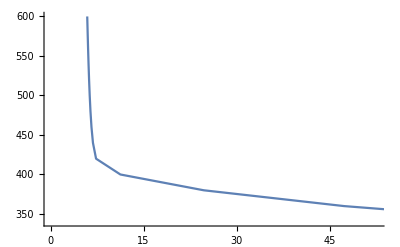

```mathematica
S3300={{11.25875199751686,400},{7.338532954954293,420},{6.83789289852607,440},{6.5981576527084576,460},{6.4364872296187405,480},{6.313070272120231,500},{6.21201892545417,520},{6.125771086695646,540},{6.049270392390012,560},{5.9797197211996815,580},{5.9149506039150355,600}};
```